## Intestine development expression data

```mathematica
SetDirectory["/Users/miriadler/Documents/development/cellSpecificExp"]
```

/Users/miriadler/Documents/development/cellSpecificExp

```mathematica
FileNames[]
```

{cell_specific_pcw_08.csv,cell_specific_pcw_10.csv,cell_specific_pcw_12.csv,cell_specific_pcw_15.csv,cell_specific_pcw_16.csv,cell_specific_pcw_17.csv,cell_specific_pcw_18.csv,cell_specific_pcw_20.csv,cell_specific_pcw_22.csv}

```mathematica
cellSpecific=Import[#]&/@FileNames[];
```

```mathematica
cellSpecificF=Table[Prepend[Prepend[cellSpecific[[i,;;,6;;]]ᵀ,cellSpecific[[i,;;,3]]],cellSpecific[[i,;;,2]]],{i,1,Length@cellSpecific}];
```

```mathematica
Dimensions/@cellSpecific
```

{{66,33543},{80,33543},{92,33543},{94,33543},{94,33543},{94,33543},{94,33543},{91,33543},{91,33543}}

```mathematica
cellSpecific[[1,2;;,6;;]]//MinMax
```

{0,1}

```mathematica
cellBroadF=Table[Prepend[Mean/@({Join@@GatherBy[cellSpecificF[[i]]ᵀ[[2;;]],First][[Position[GatherBy[cellSpecificF[[i]]ᵀ[[2;;]],First][[;;,1,1]],"pericytes"|"myofibroblasts_and_mesothelium"|"fibroblasts"][[;;,1]],;;,3;;]],
Join@@GatherBy[cellSpecificF[[i]]ᵀ[[2;;]],First][[Position[GatherBy[cellSpecificF[[i]]ᵀ[[2;;]],First][[;;,1,1]],"immune"][[;;,1]],;;,3;;]],Join@@GatherBy[cellSpecificF[[i]]ᵀ[[2;;]],First][[Position[GatherBy[cellSpecificF[[i]]ᵀ[[2;;]],First][[;;,1,1]],"endothelium"][[;;,1]],;;,3;;]],Join@@GatherBy[cellSpecificF[[i]]ᵀ[[2;;]],First][[Position[GatherBy[cellSpecificF[[i]]ᵀ[[2;;]],First][[;;,1,1]],"epithelium"][[;;,1]],;;,3;;]],Join@@GatherBy[cellSpecificF[[i]]ᵀ[[2;;]],First][[Position[GatherBy[cellSpecificF[[i]]ᵀ[[2;;]],First][[;;,1,1]],"neural"][[;;,1]],;;,3;;]],Join@@GatherBy[cellSpecificF[[i]]ᵀ[[2;;]],First][[Position[GatherBy[cellSpecificF[[i]]ᵀ[[2;;]],First][[;;,1,1]],"muscularis"][[;;,1]],;;,3;;]]}),cellSpecificF[[i,3;;,1]]]ᵀ,{i,1,Length@cellSpecificF}];
cellBroadFLog=Table[Join[{#[[1]]},Log10[10^6#[[2;;]]+1]]&/@cellBroadF[[i]],{i,1,9}];
```

```mathematica
geneNamesAll=cellSpecificF[[1,3;;,1]];
```

```mathematica
plotGeneExp[gene_,pcw_]:=BarChart[#[[;;,3]],ChartLegends->#[[;;,2]],PlotLabel->#[[1,1]],ChartStyle->24]&/@GatherBy[Select[{cellSpecificF[[pcw]][[1]],cellSpecificF[[pcw]][[2]],Select[cellSpecificF[[pcw]],#[[1]]==gene&][[1]]}ᵀ,#[[3]]>0&],#[[1]]&];
```

```mathematica
GeneExpSpecCT[gene_,pcw_]:=Select[{cellSpecificF[[pcw]][[1]],cellSpecificF[[pcw]][[2]],Select[cellSpecificF[[pcw]],#[[1]]==gene&][[1]]}ᵀ,#[[3]]>0&][[;;,;;2]];
```

```mathematica
plotGeneExpBroad[gene_,pcw_]:=BarChart[#[[2;;]],PlotLabel->#[[1]],ChartLegends->{"Stromal","Immune","Endothelium","Epithelium","Neural","Muscularis"},ChartStyle->"Pastel"]&@Select[cellBroadFLog[[pcw]],#[[1]]==gene&][[1]];
```

```mathematica
GeneExpBroadCT[gene_,pcw_]:=Select[({Select[cellBroadFLog[[pcw]],#[[1]]==gene&][[1,2;;]],BCTs}ᵀ),#[[1]]>0&][[;;,2]];
```

```mathematica
GeneExpValBroadCT[gene_,pcw_]:=Select[cellBroadFLog[[pcw]],#[[1]]==gene&][[1,2;;]];
```

```mathematica
CTs=Union@@(#ᵀ&/@cellSpecificF[[;;,1;;2,2;;]]);
```

```mathematica
PCWs={8,10,12,15,16,17,18,20,22};
```

```mathematica
plotGeneExpDynamics[gene_]:=(ListLinePlot[Tooltip[#[[1]],#[[2]]]&/@({#[[;;,1]],#[[;;,3]]}ᵀ),PlotLabel->#[[1,2]],PlotLegends->#[[;;,3]],PlotStyle->Thick,PlotRange->All]&@({{PCWs,#[[;;,3]]}ᵀ,#[[1,1]],#[[1,2]]}&/@#))&/@GatherBy[Select[Table[Table[(Select[{cellSpecificF[[i]][[1]],cellSpecificF[[i]][[2]],Select[cellSpecificF[[i]],#[[1]]==gene&][[1]]}ᵀ,{#[[1]],#[[2]]}==ct&]/.{}->{Append[ct,0]})[[1]],{i,1,9}],{ct,CTs}],Total[#[[;;,3]]]>0&],#[[1,1]]&];
```

```mathematica
plotGeneExpDynamicsBroad[gene_]:=ListLinePlot[{PCWs,#}ᵀ&/@#[[2]],PlotStyle->"Pastel",PlotLegends->{"Stromal","Immune","Endothelium","Epithelium","Neural","Muscularis"},PlotLabel->#[[1]]]&@({#[[1,1]],#[[;;,2;;]]ᵀ}&@Table[Select[cellBroadFLog[[i]],#[[1]]==gene&][[1]],{i,1,9}]);
```

```mathematica
meta=Import["/Users/miriadler/Documents/development/metadata_allcompartments.csv"];
```

```mathematica
meta2=meta/."Fibroblasts"->"Stromal"/."Mesothelium"->"Stromal"/."Myofibroblasts"->"Stromal"/."Pericytes"->"Stromal";
```

```mathematica
BCTs=Union[meta2[[2;;,-1]]];
```

```mathematica
metaEpi=Import["/Users/miriadler/Documents/development/metadata_alltime_epithelium.csv"];
metaFib=Import["/Users/miriadler/Documents/development/metadata_alltime_fibroblasts.csv"];
metaMyoF=Import["/Users/miriadler/Documents/development/metadata_alltime_myofibroblasts_and_mesothelium.csv"];
metaPeri=Import["/Users/miriadler/Documents/development/metadata_alltime_pericytes.csv"];
metaImm=Import["/Users/miriadler/Documents/development/metadata_alltime_immune.csv"];
```

```mathematica
humanTFs=Import["/Users/miriadler/Documents/development/TF_names _human.txt","Data"][[;;,1]];
```

```mathematica
posTFs=Position[cellBroadFLog[[1]][[;;,1]],Alternatives@@humanTFs][[;;,1]];
```

```mathematica
LigsTM={"Aldh1a1","Aldh1a2","Aldh1a3","Aldh1a7","Bmp1","Bmp10","Bmp2","Bmp2k","Bmp3","Bmp4","Bmp5","Bmp6","Bmp7","Bmp8a","Dhh","Fgf1","Fgf10","Fgf11","Fgf12","Fgf13","Fgf14","Fgf16","Fgf18","Fgf2","Fgf21","Fgf3","Fgf5","Fgf7","Fgf9","Ihh","Rdh10","Shh","Wnt10a","Wnt10b","Wnt11","Wnt16","Wnt2","Wnt2b","Wnt3","Wnt3a","Wnt4","Wnt5a","Wnt5b","Wnt6","Wnt7a","Wnt7b","Wnt8b","Wnt9a","Wnt9b"};
```

```mathematica
RecsTM={"Acvr2a","Acvr2b","Bmpr1a","Bmpr1b","Bmpr2","Eng","Fgfr1","Fgfr1op","Fgfr1op2","Fgfr2","Fgfr3","Fgfr4","Fgfrl1","Fzd1","Fzd10","Fzd2","Fzd3","Fzd4","Fzd5","Fzd6","Fzd7","Fzd8","Fzd9","Gpc1","Gpc2","Gpc3","Gpc4","Gpc5","Gpc6","Lgr4","Lgr5","Lgr6","Lrp5","Lrp6","Ncoa1","Ncoa2","Ncoa3","Ncoa4","Ncoa5","Ncoa6","Ncoa7","Ncor1","Ncor2","Ptch1","Ptch2","Ptchd1","Ptchd2","Rara","Rarb","Rarg","Rarres1","Rarres2","Rgma","Rgmb","Ror1","Ror2","Rora","Rorb","Rorc","Rspo1","Rspo3","Rspo4","Rxra","Rxrb","Rxrg","Ryk","Smo"};
```

```mathematica
morphAntByFam=Join@@{{"NOG","CHRD","CHRDL1","CHRDL2","FSTL1","FSTL5","FSTL4","FSTL3","TWSG1","NBL1","GREM2","GREM1","DAND5","CER1","SOST","SOSTDC1"},
{"SFRP2","SFRP4","SFRP1","SFRP5","FRZB","WIF1","DKK2","DKK4","DKK3","DKK1","DKKL1"},
{"SPRY1","SPRY2","SPRY3","SPRY4"},
{"HHIPL2","HHIP.AS1","HHIP","HHIPL1"}};
```

```mathematica
posLigs=Position[cellBroadFLog[[1]][[;;,1]],Alternatives@@(ToUpperCase/@LigsTM)][[;;,1]];
```

```mathematica
posRecs=Position[cellBroadFLog[[1]][[;;,1]],Alternatives@@(ToUpperCase/@RecsTM)][[;;,1]];
```

```mathematica
posAnts=Position[cellBroadFLog[[1]][[;;,1]],Alternatives@@(morphAntByFam)][[;;,1]];
```

```mathematica
LigsInt=cellBroadFLog[[1]][[;;,1]][[posLigs]];
```

```mathematica
RecsInt=cellBroadFLog[[1]][[;;,1]][[posRecs]];
```

```mathematica
AntsInt=cellBroadFLog[[1]][[;;,1]][[posAnts]];
```

```mathematica
BCTs={"Stromal","Immune","Endothelium","Epithelium","Neural","Muscularis"};
```

## Intestine development regulatory networks

### network analysis functions

```mathematica
<<IGraphM`
```

IGraph/M 0.6.2 (July 25, 2022)
Evaluate IGDocumentation[] to get started.

```mathematica
<<HypothesisTesting`
```

Finding Network Motifs:

```mathematica
NetMotFinderAll[g_,e_]:=Module[{AR,gRands,real2NMFL,rands2NMFL,netMot2N,real3N,rands3N,netMot3N,real4N,rands4N,netMot4N,allMotifs},
AR=Select[{{Graph[1->1],Length@Select[EdgeList[g],#[[1]]==#[[2]]&]}},#[[2]]>0&];
gRands=Table[IGRewire[g,1000000],100];
real2NMFL=Length@(Join@@(Select[Gather[Subgraph[g,#]&/@Union[Sort/@({1,2}/.IGLADFindSubisomorphisms[-Graphics-,g])],IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[SimpleGraph[#[[1]]],-Graphics-]&]))//Quiet;
rands2NMFL=Length/@Table[Join@@Select[Gather[Subgraph[gRands[[i]],#]&/@Union[Sort/@({1,2}/.IGLADFindSubisomorphisms[-Graphics-,gRands[[i]]])],IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[SimpleGraph[#[[1]]],-Graphics-]&],{i,1,Length@gRands}]//Quiet;
real3N=IGMotifs[g,3,1-e{1,1,1}];
rands3N=IGMotifs[#,3,1-e{1,1,1}]&/@gRands;
netMot2N=Select[{{-Graphics-,real2NMFL,N@((real2NMFL-Mean[rands2NMFL])/StandardDeviation[rands2NMFL])}},#[[3]]>(*3*)2&]//Quiet;netMot3N=SortBy[{#[[1]],#[[3]],N@((#[[3]]-Mean[#[[2]]])/StandardDeviation[#[[2]]])}&/@Select[Select[{IGData[{"AllDirectedGraphs",3}],rands3Nᵀ,real3N}ᵀ,WeaklyConnectedGraphQ[#[[1]]]&],N@((#[[3]]-Mean[#[[2]]])/StandardDeviation[#[[2]]])>(*3*)2&],-#[[3]]&]//Quiet;
real4N=IGMotifs[g,4,1-e{1,1,1,1}];
rands4N=IGMotifs[#,4,1-e{1,1,1,1}]&/@gRands;
netMot4N=SortBy[{#[[1]],#[[3]],N@((#[[3]]-Mean[#[[2]]])/StandardDeviation[#[[2]]])}&/@Select[Select[{IGData[{"AllDirectedGraphs",4}],rands4Nᵀ,real4N}ᵀ,WeaklyConnectedGraphQ[#[[1]]]&],N@((#[[3]]-Mean[#[[2]]])/StandardDeviation[#[[2]]])>(*3*)2&],-#[[3]]&]//Quiet;
allMotifs={AR,netMot2N,netMot3N,netMot4N};
allMotifs
]
```

Finding Network Motifs:

```mathematica
NetMotFinderAllUp3[g_,e_]:=Module[{AR,gRands,real2NMFL,rands2NMFL,netMot2N,real3N,rands3N,netMot3N,allMotifs,uniqMotifs,uniqMotifs3N},
AR=Select[{{Graph[1->1],Length@Select[EdgeList[g],#[[1]]==#[[2]]&]}},#[[2]]>0&];
gRands=Table[IGRewire[g,1000000],100];
real2NMFL=Length@(Join@@(Select[Gather[Subgraph[g,#]&/@Union[Sort/@({1,2}/.IGLADFindSubisomorphisms[-Graphics-,g])],IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[SimpleGraph[#[[1]]],-Graphics-]&]))//Quiet;
rands2NMFL=Length/@Table[Join@@Select[Gather[Subgraph[gRands[[i]],#]&/@Union[Sort/@({1,2}/.IGLADFindSubisomorphisms[-Graphics-,gRands[[i]]])],IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[SimpleGraph[#[[1]]],-Graphics-]&],{i,1,Length@gRands}]//Quiet;
real3N=IGMotifs[g,3,1-e{1,1,1}];
rands3N=IGMotifs[#,3,1-e{1,1,1}]&/@gRands;
netMot2N=Select[{{-Graphics-,real2NMFL,N@((real2NMFL-Mean[rands2NMFL])/StandardDeviation[rands2NMFL])}},#[[3]]>(*3*)2&]//Quiet;netMot3N=SortBy[{#[[1]],#[[3]],N@((#[[3]]-Mean[#[[2]]])/StandardDeviation[#[[2]]])}&/@Select[Select[{IGData[{"AllDirectedGraphs",3}],rands3Nᵀ,real3N}ᵀ,WeaklyConnectedGraphQ[#[[1]]]&],N@((#[[3]]-Mean[#[[2]]])/StandardDeviation[#[[2]]])>(*3*)2&],-#[[3]]&]//Quiet;
allMotifs={AR,netMot2N,netMot3N};
allMotifs
]
```

```mathematica
NetMotFinderAllUp3All[g_,e_]:=Module[{AR,gRands,real2NMFL,rands2NMFL,netMot2N,real3N,rands3N,netMot3N,allMotifs,uniqMotifs,uniqMotifs3N},
AR=Select[{{Graph[1->1],Length@Select[EdgeList[g],#[[1]]==#[[2]]&]}},#[[2]]>0&];
gRands=Table[IGRewire[g,1000000],100];
real2NMFL=Length@(Join@@(Select[Gather[Subgraph[g,#]&/@Union[Sort/@({1,2}/.IGLADFindSubisomorphisms[-Graphics-,g])],IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[SimpleGraph[#[[1]]],-Graphics-]&]))//Quiet;
rands2NMFL=Length/@Table[Join@@Select[Gather[Subgraph[gRands[[i]],#]&/@Union[Sort/@({1,2}/.IGLADFindSubisomorphisms[-Graphics-,gRands[[i]]])],IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[SimpleGraph[#[[1]]],-Graphics-]&],{i,1,Length@gRands}]//Quiet;
real3N=IGMotifs[g,3,1-e{1,1,1}];
rands3N=IGMotifs[#,3,1-e{1,1,1}]&/@gRands;
netMot2N={{-Graphics-,real2NMFL,N@((real2NMFL-Mean[rands2NMFL])/StandardDeviation[rands2NMFL])}}//Quiet;netMot3N=SortBy[{#[[1]],#[[3]],N@((#[[3]]-Mean[#[[2]]])/StandardDeviation[#[[2]]])}&/@Select[{IGData[{"AllDirectedGraphs",3}],rands3Nᵀ,real3N}ᵀ,WeaklyConnectedGraphQ[#[[1]]]&],-#[[3]]&]//Quiet;
allMotifs={AR,netMot2N,netMot3N};
allMotifs
]
```

Computing all possible circuit combinations:

```mathematica
circuitARComp[g_]:=Module[{gg,comps},
gg=DirectedEdge[{#[[1]],a},{#[[2]],a}]&/@(EdgeList@SimpleGraph[g]);
comps=Union[Graph/@((Join[EdgeList[gg],#]&/@Subsets[#->#&/@VertexList[gg],VertexCount[gg]])),SameTest->(IsomorphicGraphQ[#1,#2]&)];
(*{Length[comps],comps}*)comps]
```

```mathematica
circuitComp[g1_,g2_]:=Module[{gg1,gg2,rule,Jgraph,Jgraph2,comps,compsAll,nomOfC},
gg1=DirectedEdge[{#[[1]],a},{#[[2]],a}]&/@(EdgeList@g1);
gg2=DirectedEdge[{#[[1]],b},{#[[2]],b}]&/@(EdgeList@g2);
rule=Select[DeleteCases[Subsets[((Rule@@@Flatten[Table[{i,j},{i,VertexList[gg1]},{j,VertexList[gg2]}],1])),Min[VertexCount[g1],VertexCount[g2]]-1],{}],(Length[#]==Length[GatherBy[#,First]])&&(Length[#]==Length[GatherBy[#,Last]])&];
Jgraph={EdgeList[#[[1]]],#[[2]]}&/@(Gather[{Graph/@(Union[EdgeList@Graph[(Join@@(EdgeList/@{gg1,gg2}))/.#]]&/@rule),rule}ᵀ,IsomorphicGraphQ[#1[[1]],#2[[1]]]&][[;;,1]]);
Jgraph2=DeleteCases[Table[If[Select[Subgraph[Graph[Jgraph[[i,1]]],#]&/@(Range@VertexCount[g1]/.IGLADFindSubisomorphisms[g1,Graph[Jgraph[[i,1]]]]),IsomorphicGraphQ[#,g1]&]=={}||Select[Subgraph[Graph[Jgraph[[i,1]]],#]&/@(Range@VertexCount[g2]/.IGLADFindSubisomorphisms[g2,Graph[Jgraph[[i,1]]]]),IsomorphicGraphQ[#,g2]&]=={},{},Jgraph[[i]]],{i,1,Length@Jgraph}],{}];
(*comps=Graph[Join[#[[1]],#[[2]]],EdgeStyle->Join[Thread[#->Thick]&/@#[[1]],Thread[#->Dashed]&/@#[[2]]]]&/@({Jgraph2[[;;,1]],(DirectedEdge@@@Join[#,Reverse/@#]&@DeleteCases[Subsets[Complement[#[[1]],#[[2]]],{2}],{{_,x_},{_,x_}}]&/@({VertexList[Graph[#[[1]]]],#[[2,;;,2]]}&/@Jgraph2))}ᵀ);*)(*compsAll=Union[Join@@(Graph/@(Join@@@Thread[#,List,{2}])&/@({Jgraph2[[;;,1]],Subsets[DirectedEdge@@@Join[#,Reverse/@#],(VertexCount[g1]+VertexCount[g2]-2)2]&@DeleteCases[Subsets[Complement[#[[1]],#[[2]]],{2}],{{_,x_},{_,x_}}]&/@({VertexList[Graph[#[[1]]]],#[[2,;;,2]]}&/@Jgraph2)}ᵀ)),SameTest->(IsomorphicGraphQ[#1,#2]&)];*)
nomOfC=Total@(3^(2Length[DeleteCases[Subsets[Complement[#[[1]],#[[2]]],{2}],{{_,x_},{_,x_}}]])&/@({VertexList[Graph[#[[1]]]],#[[2,;;,2]]}&/@Jgraph2));
(*{nomOfC,Length[compsAll],Graph/@Jgraph2[[;;,1]],comps,compsAll}*)Graph/@Jgraph2[[;;,1]]]
```

```mathematica
ExtComb[g_,g1_,g2_]:=Module[{gg1,gg2,rule,Jgraph,Jgraph2,Jgraph3,compsAll},
gg1=DirectedEdge[{#[[1]],a},{#[[2]],a}]&/@(EdgeList@g1);
gg2=DirectedEdge[{#[[1]],b},{#[[2]],b}]&/@(EdgeList@g2);
rule=Select[DeleteCases[Subsets[((Rule@@@Flatten[Table[{i,j},{i,VertexList[gg1]},{j,VertexList[gg2]}],1])),Min[VertexCount[g1],VertexCount[g2]]-1],{}],(Length[#]==Length[GatherBy[#,First]])&&(Length[#]==Length[GatherBy[#,Last]])&];
Jgraph={EdgeList[#[[1]]],#[[2]]}&/@(Gather[{Graph/@(Union[EdgeList@Graph[(Join@@(EdgeList/@{gg1,gg2}))/.#]]&/@rule),rule}ᵀ,IsomorphicGraphQ[#1[[1]],#2[[1]]]&][[;;,1]]);
Jgraph2=DeleteCases[Table[If[Select[Subgraph[Graph[Jgraph[[i,1]]],#]&/@(Range@VertexCount[g1]/.IGLADFindSubisomorphisms[g1,Graph[Jgraph[[i,1]]]]),IsomorphicGraphQ[#,g1]&]=={}||Select[Subgraph[Graph[Jgraph[[i,1]]],#]&/@(Range@VertexCount[g2]/.IGLADFindSubisomorphisms[g2,Graph[Jgraph[[i,1]]]]),IsomorphicGraphQ[#,g2]&]=={},{},Jgraph[[i]]],{i,1,Length@Jgraph}],{}];
Jgraph3=Select[Jgraph2,IsomorphicGraphQ[g,AdjacencyGraph[AdjacencyMatrix[#[[1]]]]]&];compsAll=Union[Join@@(Graph/@(Join@@@Thread[#,List,{2}])&/@({Jgraph3[[;;,1]],Subsets[DirectedEdge@@@Join[#,Reverse/@#],(VertexCount[g1]+VertexCount[g2]-2)2]&@DeleteCases[Subsets[Complement[#[[1]],#[[2]]],{2}],{{_,x_},{_,x_}}]&/@({VertexList[Graph[#[[1]]]],#[[2,;;,2]]}&/@Jgraph3)}ᵀ)),SameTest->(IsomorphicGraphQ[#1,#2]&)];
compsAll]
```

Motif Dictionary:

```mathematica
md=Join[Graph/@{{1->1},{1->2,2->1}},Select[IGData[{"AllDirectedGraphs",3}],WeaklyConnectedGraphQ[#]&]];
```

Finding significantly enriched and under-represented motif combinations of one shared node:

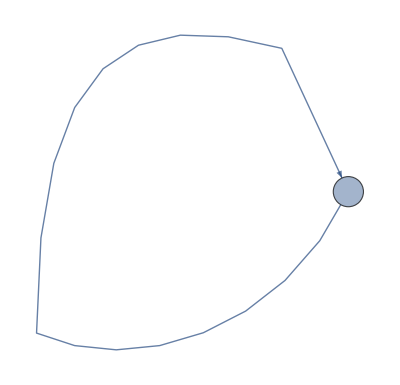
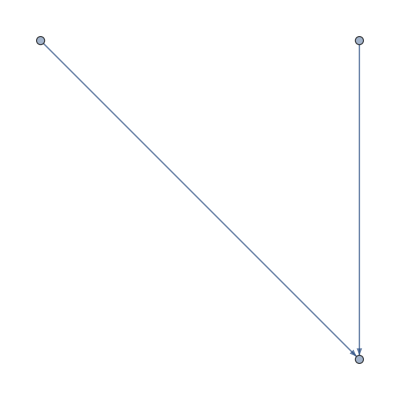
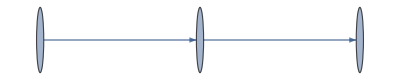
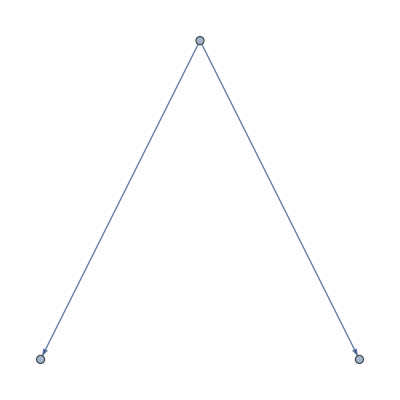
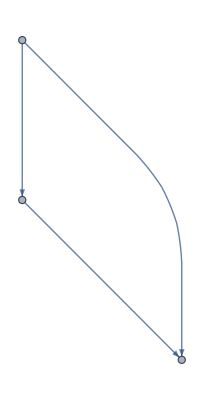

```mathematica
EnrichedCombsMFinderRandUpTo3[g_,gRands_,netMot_,pos_]:=Module[{allMotifsIns,allMotifsInsRand,ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,allregted3s,allregted3sRand,allChain3s,allChain3sRand,allIn1MFL3s,allIn1MFL3sRand,allFFL3s,allFFL3sRand,allreging3s,allreging3sRand,allRegtedMFL3s,allRegtedMFL3sRand,allOut1MFL3s,allOut1MFL3sRand,allLoopMFL3s,allLoopMFL3sRand,allRegingMFL3s,allRegingMFL3sRand,allDoubleMFL3s,allDoubleMFL3sRand,TwoMFL3SideNodes,TwoMFL3MidNodes,TwoMFL3SideNodesRand,TwoMFL3MidNodesRand,allTwoMFL3s,allTwoMFL3sRand,ThreeMFL3Nodes,ThreeMFL3NodesRand,motifsRoles,motifsRoles2,sameRoleCombs,sameRoleCombs2,nodesInMotifRoles,nodesInMotifRolesRand,motifCombs,motifCombsSame,cols,bg,t},
allMotifsIns=DeleteCases[Prepend[Table[Select[Subgraph[SimpleGraph[g],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[g]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],Select[Subgraph[g,#]&/@Union[Sort/@((Range@VertexCount[-Graphics-])/.IGLADFindSubisomorphisms[-Graphics-,g])],IsomorphicGraphQ[#,-Graphics-]&]],{}];
allMotifsInsRand=Table[Table[Select[Subgraph[SimpleGraph[gRands[[i]]],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[gRands[[i]]]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],{i,1,Length@gRands}];
ARNodes={#,1}&/@Select[EdgeList[g],#[[1]]==#[[2]]&][[;;,1]];
ARNodesRand=Table[{#,1}&/@(*RandomChoice*)RandomSample[VertexList[gRands[[i]]],Length@ARNodes],{i,1,Length@gRands}];
MFL2Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
MFL2NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
allregted3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allregted3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
regted3InNodes=Tally[Flatten[#[[;;,1]]&/@(EdgeList/@(Join@@allregted3s))]];
regted3OutNodes=Tally[#[[1,2]]&/@(EdgeList/@(Join@@allregted3s))];
regted3InNodesRand=Table[Tally[Flatten[#[[;;,1]]&/@EdgeList/@(Join@@allregted3sRand[[i]])]],{i,1,Length@gRands}];
regted3OutNodesRand=Table[Tally[#[[1,2]]&/@EdgeList/@(Join@@allregted3sRand[[i]])],{i,1,Length@gRands}];
allChain3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allChain3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
chain3InNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
chain3MedNodes=Tally[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3s)];
chain3OutNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
chain3InNodesRand=Table[Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
chain3MedNodesRand=Table[Tally[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
chain3OutNodesRand=Table[Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
allIn1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allIn1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
in1MFL3InNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out1Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out2Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3InNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
in1MFL3Out1NodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
in1MFL3Out2NodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
allreging3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allreging3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
reging3InNodes=Tally[#[[1,1]]&/@(EdgeList/@(Join@@allreging3s))];
reging3OutNodes=Tally[Flatten[#[[;;,2]]&/@(EdgeList/@(Join@@allreging3s))]];
reging3InNodesRand=Table[Tally[#[[1,1]]&/@EdgeList/@(Join@@allreging3sRand[[i]])],{i,1,Length@gRands}];
reging3OutNodesRand=Table[Tally[Flatten[#[[;;,2]]&/@EdgeList/@(Join@@allreging3sRand[[i]])]],{i,1,Length@gRands}];
allFFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allFFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
FFL3InNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3MedNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3OutNodes=Tally[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3InNodesRand=Table[Tally[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
FFL3MedNodesRand=Table[Tally[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
FFL3OutNodesRand=Table[Tally[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
allRegtedMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegtedMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegtedMFL3InNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3s)];
RegtedMFL3OutNodes=Tally[Flatten[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3s)]];
RegtedMFL3InNodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3sRand[[i]])],{i,1,Length@gRands}];
RegtedMFL3OutNodesRand=Table[Tally[Flatten[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3sRand[[i]])]],{i,1,Length@gRands}];
allOut1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allOut1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
out1MFL3In1Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3In2Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3OutNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3In1NodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
out1MFL3In2NodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
out1MFL3OutNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
allTwoMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allTwoMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
TwoMFL3SideNodes=Tally[Flatten[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3s)]];
TwoMFL3MidNodes=Tally[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3s)];
TwoMFL3SideNodesRand=Table[Tally[Flatten[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]])]],{i,1,Length@gRands}];
TwoMFL3MidNodesRand=Table[Tally[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]])],{i,1,Length@gRands}];
FBL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
FBL3NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
allLoopMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allLoopMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
LoopMFL3InNodes=Tally[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3MedNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3OutNodes=Tally[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3InNodesRand=Table[Tally[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
LoopMFL3MedNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
LoopMFL3OutNodesRand=Table[Tally[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
allRegingMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegingMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegingMFL3InNodes=Tally[Flatten[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3s)]];
RegingMFL3OutNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3s)];
RegingMFL3InNodesRand=Table[Tally[Flatten[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3sRand[[i]])]],{i,1,Length@gRands}];
RegingMFL3OutNodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3sRand[[i]])],{i,1,Length@gRands}];
allDoubleMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allDoubleMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
DoubleMFL3InNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3OutNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3ConnNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3InNodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
DoubleMFL3OutNodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
DoubleMFL3ConnNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
ThreeMFL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
ThreeMFL3NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
motifsRoles={{{{a1->a1},a1}},{{{b1->b2,b2->b1},b1}},{{{y1->y2,y3->y2},y1},{{z1->z2,z3->z2},z2}},{{{g1->g2,g2->g3},g1},{{h1->h2,h2->h3},h2},{{i1->i2,i2->i3},i3}},{{{j1->j3,j2->j3,j3->j2},j1},{{k1->k3,k2->k3,k3->k2},k3},{{l1->l3,l2->l3,l3->l2},l2}},{{{t1->t2,t1->t3},t1},{{x1->x2,x1->x3},x2}},{{{c1->c2,c1->c3,c2->c3},c1},{{d1->d2,d1->d3,d2->d3},d2},{{e1->e2,e1->e3,e2->e3},e3}},{{{m1->m3,m2->m1,m2->m3,m3->m1},m2},{{n1->n3,n2->n1,n2->n3,n3->n1},n1}},{{{o2->o3,o3->o1,o3->o2},o3},{{p2->p3,p3->p1,p3->p2},p2},{{q2->q3,q3->q1,q3->q2},q1}},{{{dd1->dd2,dd2->dd1,dd2->dd3,dd3->dd2},dd1},{{ee1->ee2,ee2->ee1,ee2->ee3,ee3->ee2},ee2}},{{{f1->f2,f2->f3,f3->f1},f1}},{{{r1->r3,r2->r1,r3->r1,r3->r2},r3},{{s1->s3,s2->s1,s3->s1,s3->s2},s2},{{w1->w3,w2->w1,w3->w1,w3->w2},w1}},{{{y2->y1,y2->y3,y3->y1,y3->y2},y2},{{z2->z1,z2->z3,z3->z1,z3->z2},z1}},{{{aa1->aa3,aa2->aa1,aa2->aa3,aa3->aa1,aa3->aa2},aa2},{{bb1->bb3,bb2->bb1,bb2->bb3,bb3->bb1,bb3->bb2},bb1},{{cc1->cc3,cc2->cc1,cc2->cc3,cc3->cc1,cc3->cc2},cc3}},{{{ff1->ff2,ff2->ff1,ff2->ff3,ff3->ff2,ff3->ff1,ff1->ff3},ff1}}};
motifsRoles2=Flatten[motifsRoles[[pos]],1](*Select[motifsRoles,Or@@Table[IsomorphicGraphQ[nm,AdjacencyGraph[AdjacencyMatrix[#[[1]]],DirectedEdges->True]],{nm,netMot}]&]*);
sameRoleCombs=Map[Graph[#,DirectedEdges->True]&,{{{1->1}},{{1->2,2->1,2->3,3->2}},{{1->2,3->2,3->4,5->4},{1->2,3->2,4->2,5->2}},{{1->2,2->3,1->4,4->5},{1->2,2->3,4->2,2->5},{1->2,2->3,4->5,5->3}},{{1->2,2->3,3->2,1->4,4->5,5->4},{1->2,2->3,3->2,4->2,2->5,5->2},{1->2,2->3,3->2,3->5,5->3,4->5}},{{1->2,1->3,1->4,1->5},{1->2,1->3,4->2,4->5}},{{1->2,1->3,2->3,1->4,1->5,4->5},{1->2,1->3,2->3,4->2,4->5,2->5},{1->2,1->3,2->3,4->5,4->3,5->3}},{{1->2,1->3,2->3,3->2,1->4,1->5,4->5,5->4},{1->2,1->3,2->3,3->2,5->3,5->4,3->4,4->3}},{{1->2,2->1,1->3,1->5,1->4,4->1},{1->2,2->1,2->5,1->3,3->1,3->4},{1->2,2->1,2->3,4->5,5->4,5->3}},{{1->2,2->1,2->3,3->2,1->4,4->1,4->5,5->4},{1->2,2->1,2->3,3->2,2->4,4->2,2->5,5->2}},{{1->2,2->3,3->1,1->4,4->5,5->1}},{{1->2,2->1,1->3,3->2,1->5,5->4,4->1,1->4},{1->3,3->2,2->3,2->1,1->5,5->4,4->5,4->1},{1->2,2->1,2->3,3->1,1->5,5->1,5->4,4->1}},{{1->2,2->1,1->4,2->4,2->3,3->2,2->5,3->5},{2->3,3->2,4->5,5->4,2->1,3->1,4->1,5->1}},{{1->2,2->1,2->3,3->2,1->3,1->4,4->5,5->4,1->5,5->1},{1->2,2->1,2->3,3->2,3->1,1->4,4->1,5->4,4->5,5->1},{1->2,2->1,1->5,5->1,1->3,3->1,1->4,4->1,4->5,3->2}},{{1->2,2->1,2->3,3->2,3->1,1->3,1->4,4->1,4->5,5->4,5->1,1->5}}},{2}];
sameRoleCombs2=Flatten[sameRoleCombs[[pos]],1](*Select[sameRoleCombs,Or@@Table[IGLADFindSubisomorphisms[nm,#]≠ {},{nm,netMot}]&]*);
nodesInMotifRoles=DeleteCases[{ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,TwoMFL3SideNodes,TwoMFL3MidNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ThreeMFL3Nodes},{}];
nodesInMotifRolesRand=Select[{ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,TwoMFL3SideNodesRand,TwoMFL3MidNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,ThreeMFL3NodesRand},Union[#]≠{{}}&]ᵀ;
motifCombs={(N@(Length[Intersection[#[[1]],#[[2]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[nodesInMotifRoles[[;;,;;,1]],{2}])/.Indeterminate->0,((N@(Length[Intersection[#[[1]],#[[2]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[#[[;;,;;,1]],{2}]&/@nodesInMotifRolesRand)ᵀ)/.Indeterminate->0,Table[Graph[(Join@@motifsRoles2[[i,1]])/.motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]],DirectedEdges->True],{i,Subsets[Range@Length[motifsRoles2],{2}]}]}ᵀ;
motifCombsSame={(N@(Count[#,_?(#[[2]]>1&)]/Length[#])&/@nodesInMotifRoles)/.Indeterminate->0,(Map[N@(Count[#,_?(#[[2]]>1&)]/Length[#])&,nodesInMotifRolesRand,{2}]ᵀ)/.Indeterminate->0,sameRoleCombs2}ᵀ;
cols=ColorData["TemperatureMap"][#]&/@Rescale[(((*#[[1]]*)(#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(Join@@{motifCombs,motifCombsSame}))/.Indeterminate->0/.ComplexInfinity->0//Quiet)];
bg=ConstantArray[White,{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
Table[bg[[i+1,i+2;;]]=cols[[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[bg[[i+1,i+1]]=cols[[i+Length[sameRoleCombs2] (Length[sameRoleCombs2]-1)-Total[Range@(Length[sameRoleCombs2]-1)]]],{i,1,Length[sameRoleCombs2]}];
t=ConstantArray["",{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
t[[1,2;;]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&/@motifsRoles2;
Table[t[[i,1]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&@motifsRoles2[[i-1]],{i,2,Length[sameRoleCombs2]+1}];
Table[t[[i+1,i+2;;]]=Table[Graph[(Join@@motifsRoles2[[i,1]])/.motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]],DirectedEdges->True],{i,Subsets[Range@(Length[sameRoleCombs2]),{2}]}][[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[t[[i+1,i+1]]=sameRoleCombs2[[i]],{i,1,Length[sameRoleCombs2]}];
{Join@@{motifCombs,motifCombsSame},(*Show[Histogram[#[[2]],PlotRange->{{0,Max[#[[1]],Max[#[[2]]]]+.1},All}],ListLinePlot[{{#[[1]],0},{#[[1]],50}},PlotStyle->Red],PlotLabel->Show[#[[3]],ImageSize->Tiny],Axes->False,Frame->True,FrameLabel->{"Jaccard Index"}]&/@Select[Join@@{motifCombs,motifCombsSame},(#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]>2&&#[[1]]>.15&]*){(Join@@{motifCombs,motifCombsSame})[[#[[1]],-1]],((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(Join@@{motifCombs,motifCombsSame})[[#[[1]]]]),#[[3]]}&/@Select[{#[[1,1]],#[[1,2]],(#[[2]])/Length[(Join@@{motifCombs,motifCombsSame})] 0.05,#[[1,3]]}&/@({SortBy[Table[{i,NormalPValue[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(Join@@{motifCombs,motifCombsSame})[[i]])][[2]],(Join@@{motifCombs,motifCombsSame})[[i,1]]},{i,1,Length[(Join@@{motifCombs,motifCombsSame})]}],#[[2]]&],Range@Length[(Join@@{motifCombs,motifCombsSame})]}ᵀ),#[[2]]≤#[[3]]&&#[[4]]≥0.15&]//Quiet,BarLegend[{"TemperatureMap",{Min[#],Max[#]}&@(((*#[[1]]*)(#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(Join@@{motifCombs,motifCombsSame}))/.Indeterminate->0/.ComplexInfinity->0//Quiet)}],Grid[t,Frame->All,Background->{None,None,Thread[Complement[Join@@Table[{i,j},{i,1,Length[sameRoleCombs2]+1},{j,1,Length[sameRoleCombs2]+1}],Position[bg,White]]->DeleteCases[Flatten[bg,1],White]]}]}(*Join@@{motifCombs,motifCombsSame}*)
]
```

Finding significantly enriched and under-represented motif combinations of one shared node (when the random networks are already provided with autoregulation):

```mathematica
EnrichedCombsMFinderRand2UpTo3[g_,gRands_,netMot_,pos_]:=Module[{allMotifsIns,allMotifsInsRand,ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,allregted3s,allregted3sRand,allChain3s,allChain3sRand,allIn1MFL3s,allIn1MFL3sRand,allFFL3s,allFFL3sRand,allreging3s,allreging3sRand,allRegtedMFL3s,allRegtedMFL3sRand,allOut1MFL3s,allOut1MFL3sRand,allLoopMFL3s,allLoopMFL3sRand,allRegingMFL3s,allRegingMFL3sRand,allDoubleMFL3s,allDoubleMFL3sRand,TwoMFL3SideNodes,TwoMFL3MidNodes,TwoMFL3SideNodesRand,TwoMFL3MidNodesRand,allTwoMFL3s,allTwoMFL3sRand,ThreeMFL3Nodes,ThreeMFL3NodesRand,motifsRoles,motifsRoles2,sameRoleCombs,sameRoleCombs2,nodesInMotifRoles,nodesInMotifRolesRand,motifCombs,motifCombsSame,cols,bg,t},
allMotifsIns=DeleteCases[Prepend[Table[Select[Subgraph[SimpleGraph[g],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[g]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],Select[Subgraph[g,#]&/@Union[Sort/@((Range@VertexCount[-Graphics-])/.IGLADFindSubisomorphisms[-Graphics-,g])],IsomorphicGraphQ[#,-Graphics-]&]],{}];
allMotifsInsRand=Table[Table[Select[Subgraph[SimpleGraph[gRands[[i]]],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[gRands[[i]]]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],{i,1,Length@gRands}];
ARNodes={#,1}&/@Select[EdgeList[g],#[[1]]==#[[2]]&][[;;,1]];
ARNodesRand=Table[{#,1}&/@Select[EdgeList[gRands[[i]]],#[[1]]==#[[2]]&][[;;,1]],{i,1,Length@gRands}];
MFL2Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
MFL2NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
allregted3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allregted3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
regted3InNodes=Tally[Flatten[#[[;;,1]]&/@(EdgeList/@(Join@@allregted3s))]];
regted3OutNodes=Tally[#[[1,2]]&/@(EdgeList/@(Join@@allregted3s))];
regted3InNodesRand=Table[Tally[Flatten[#[[;;,1]]&/@EdgeList/@(Join@@allregted3sRand[[i]])]],{i,1,Length@gRands}];
regted3OutNodesRand=Table[Tally[#[[1,2]]&/@EdgeList/@(Join@@allregted3sRand[[i]])],{i,1,Length@gRands}];
allChain3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allChain3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
chain3InNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
chain3MedNodes=Tally[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3s)];
chain3OutNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
chain3InNodesRand=Table[Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
chain3MedNodesRand=Table[Tally[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
chain3OutNodesRand=Table[Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
allIn1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allIn1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
in1MFL3InNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out1Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out2Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3InNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
in1MFL3Out1NodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
in1MFL3Out2NodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
allreging3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allreging3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
reging3InNodes=Tally[#[[1,1]]&/@(EdgeList/@(Join@@allreging3s))];
reging3OutNodes=Tally[Flatten[#[[;;,2]]&/@(EdgeList/@(Join@@allreging3s))]];
reging3InNodesRand=Table[Tally[#[[1,1]]&/@EdgeList/@(Join@@allreging3sRand[[i]])],{i,1,Length@gRands}];
reging3OutNodesRand=Table[Tally[Flatten[#[[;;,2]]&/@EdgeList/@(Join@@allreging3sRand[[i]])]],{i,1,Length@gRands}];
allFFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allFFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
FFL3InNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3MedNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3OutNodes=Tally[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3InNodesRand=Table[Tally[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
FFL3MedNodesRand=Table[Tally[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
FFL3OutNodesRand=Table[Tally[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
allRegtedMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegtedMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegtedMFL3InNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3s)];
RegtedMFL3OutNodes=Tally[Flatten[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3s)]];
RegtedMFL3InNodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3sRand[[i]])],{i,1,Length@gRands}];
RegtedMFL3OutNodesRand=Table[Tally[Flatten[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3sRand[[i]])]],{i,1,Length@gRands}];
allOut1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allOut1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
out1MFL3In1Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3In2Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3OutNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3In1NodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
out1MFL3In2NodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
out1MFL3OutNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
allTwoMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allTwoMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
TwoMFL3SideNodes=Tally[Flatten[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3s)]];
TwoMFL3MidNodes=Tally[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3s)];
TwoMFL3SideNodesRand=Table[Tally[Flatten[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]])]],{i,1,Length@gRands}];
TwoMFL3MidNodesRand=Table[Tally[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]])],{i,1,Length@gRands}];
FBL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
FBL3NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
allLoopMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allLoopMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
LoopMFL3InNodes=Tally[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3MedNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3OutNodes=Tally[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3InNodesRand=Table[Tally[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
LoopMFL3MedNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
LoopMFL3OutNodesRand=Table[Tally[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
allRegingMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegingMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegingMFL3InNodes=Tally[Flatten[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3s)]];
RegingMFL3OutNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3s)];
RegingMFL3InNodesRand=Table[Tally[Flatten[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3sRand[[i]])]],{i,1,Length@gRands}];
RegingMFL3OutNodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3sRand[[i]])],{i,1,Length@gRands}];
allDoubleMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allDoubleMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
DoubleMFL3InNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3OutNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3ConnNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3InNodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
DoubleMFL3OutNodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
DoubleMFL3ConnNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
ThreeMFL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
ThreeMFL3NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
motifsRoles={{{{a1->a1},a1}},{{{b1->b2,b2->b1},b1}},{{{y1->y2,y3->y2},y1},{{z1->z2,z3->z2},z2}},{{{g1->g2,g2->g3},g1},{{h1->h2,h2->h3},h2},{{i1->i2,i2->i3},i3}},{{{j1->j3,j2->j3,j3->j2},j1},{{k1->k3,k2->k3,k3->k2},k3},{{l1->l3,l2->l3,l3->l2},l2}},{{{t1->t2,t1->t3},t1},{{x1->x2,x1->x3},x2}},{{{c1->c2,c1->c3,c2->c3},c1},{{d1->d2,d1->d3,d2->d3},d2},{{e1->e2,e1->e3,e2->e3},e3}},{{{m1->m3,m2->m1,m2->m3,m3->m1},m2},{{n1->n3,n2->n1,n2->n3,n3->n1},n1}},{{{o2->o3,o3->o1,o3->o2},o3},{{p2->p3,p3->p1,p3->p2},p2},{{q2->q3,q3->q1,q3->q2},q1}},{{{dd1->dd2,dd2->dd1,dd2->dd3,dd3->dd2},dd1},{{ee1->ee2,ee2->ee1,ee2->ee3,ee3->ee2},ee2}},{{{f1->f2,f2->f3,f3->f1},f1}},{{{r1->r3,r2->r1,r3->r1,r3->r2},r3},{{s1->s3,s2->s1,s3->s1,s3->s2},s2},{{w1->w3,w2->w1,w3->w1,w3->w2},w1}},{{{y2->y1,y2->y3,y3->y1,y3->y2},y2},{{z2->z1,z2->z3,z3->z1,z3->z2},z1}},{{{aa1->aa3,aa2->aa1,aa2->aa3,aa3->aa1,aa3->aa2},aa2},{{bb1->bb3,bb2->bb1,bb2->bb3,bb3->bb1,bb3->bb2},bb1},{{cc1->cc3,cc2->cc1,cc2->cc3,cc3->cc1,cc3->cc2},cc3}},{{{ff1->ff2,ff2->ff1,ff2->ff3,ff3->ff2,ff3->ff1,ff1->ff3},ff1}}};
motifsRoles2=Flatten[motifsRoles[[pos]],1](*Select[motifsRoles,Or@@Table[IsomorphicGraphQ[nm,AdjacencyGraph[AdjacencyMatrix[#[[1]]],DirectedEdges->True]],{nm,netMot}]&]*);
sameRoleCombs=Map[Graph[#,DirectedEdges->True]&,{{{1->1}},{{1->2,2->1,2->3,3->2}},{{1->2,3->2,3->4,5->4},{1->2,3->2,4->2,5->2}},{{1->2,2->3,1->4,4->5},{1->2,2->3,4->2,2->5},{1->2,2->3,4->5,5->3}},{{1->2,2->3,3->2,1->4,4->5,5->4},{1->2,2->3,3->2,4->2,2->5,5->2},{1->2,2->3,3->2,3->5,5->3,4->5}},{{1->2,1->3,1->4,1->5},{1->2,1->3,4->2,4->5}},{{1->2,1->3,2->3,1->4,1->5,4->5},{1->2,1->3,2->3,4->2,4->5,2->5},{1->2,1->3,2->3,4->5,4->3,5->3}},{{1->2,1->3,2->3,3->2,1->4,1->5,4->5,5->4},{1->2,1->3,2->3,3->2,5->3,5->4,3->4,4->3}},{{1->2,2->1,1->3,1->5,1->4,4->1},{1->2,2->1,2->5,1->3,3->1,3->4},{1->2,2->1,2->3,4->5,5->4,5->3}},{{1->2,2->1,2->3,3->2,1->4,4->1,4->5,5->4},{1->2,2->1,2->3,3->2,2->4,4->2,2->5,5->2}},{{1->2,2->3,3->1,1->4,4->5,5->1}},{{1->2,2->1,1->3,3->2,1->5,5->4,4->1,1->4},{1->3,3->2,2->3,2->1,1->5,5->4,4->5,4->1},{1->2,2->1,2->3,3->1,1->5,5->1,5->4,4->1}},{{1->2,2->1,1->4,2->4,2->3,3->2,2->5,3->5},{2->3,3->2,4->5,5->4,2->1,3->1,4->1,5->1}},{{1->2,2->1,2->3,3->2,1->3,1->4,4->5,5->4,1->5,5->1},{1->2,2->1,2->3,3->2,3->1,1->4,4->1,5->4,4->5,5->1},{1->2,2->1,1->5,5->1,1->3,3->1,1->4,4->1,4->5,3->2}},{{1->2,2->1,2->3,3->2,3->1,1->3,1->4,4->1,4->5,5->4,5->1,1->5}}},{2}];
sameRoleCombs2=Flatten[sameRoleCombs[[pos]],1](*Select[sameRoleCombs,Or@@Table[IGLADFindSubisomorphisms[nm,#]≠ {},{nm,netMot}]&]*);
nodesInMotifRoles=DeleteCases[{ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,TwoMFL3SideNodes,TwoMFL3MidNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ThreeMFL3Nodes},{}];
nodesInMotifRolesRand=Select[{ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,TwoMFL3SideNodesRand,TwoMFL3MidNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,ThreeMFL3NodesRand},Union[#]≠{{}}&]ᵀ;
motifCombs={(N@(Length[Intersection[#[[1]],#[[2]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[nodesInMotifRoles[[;;,;;,1]],{2}])/.Indeterminate->0,((N@(Length[Intersection[#[[1]],#[[2]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[#[[;;,;;,1]],{2}]&/@nodesInMotifRolesRand)ᵀ)/.Indeterminate->0,Table[Graph[(Join@@motifsRoles2[[i,1]])/.motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]],DirectedEdges->True],{i,Subsets[Range@Length[motifsRoles2],{2}]}]}ᵀ;
motifCombsSame={(N@(Count[#,_?(#[[2]]>1&)]/Length[#])&/@nodesInMotifRoles)/.Indeterminate->0,(Map[N@(Count[#,_?(#[[2]]>1&)]/Length[#])&,nodesInMotifRolesRand,{2}]ᵀ)/.Indeterminate->0,sameRoleCombs2}ᵀ;
cols=ColorData["TemperatureMap"][#]&/@Rescale[(((*#[[1]]*)(#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(Join@@{motifCombs,motifCombsSame}))/.Indeterminate->0/.ComplexInfinity->0//Quiet)];
bg=ConstantArray[White,{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
Table[bg[[i+1,i+2;;]]=cols[[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[bg[[i+1,i+1]]=cols[[i+Length[sameRoleCombs2] (Length[sameRoleCombs2]-1)-Total[Range@(Length[sameRoleCombs2]-1)]]],{i,1,Length[sameRoleCombs2]}];
t=ConstantArray["",{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
t[[1,2;;]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&/@motifsRoles2;
Table[t[[i,1]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&@motifsRoles2[[i-1]],{i,2,Length[sameRoleCombs2]+1}];
Table[t[[i+1,i+2;;]]=Table[Graph[(Join@@motifsRoles2[[i,1]])/.motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]],DirectedEdges->True],{i,Subsets[Range@(Length[sameRoleCombs2]),{2}]}][[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[t[[i+1,i+1]]=sameRoleCombs2[[i]],{i,1,Length[sameRoleCombs2]}];
{Join@@{motifCombs,motifCombsSame},(*Show[Histogram[#[[2]],PlotRange->{{0,Max[#[[1]],Max[#[[2]]]]+.1},All}],ListLinePlot[{{#[[1]],0},{#[[1]],50}},PlotStyle->Red],PlotLabel->Show[#[[3]],ImageSize->Tiny],Axes->False,Frame->True,FrameLabel->{"Jaccard Index"}]&/@Select[Join@@{motifCombs,motifCombsSame},(#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]>2&&#[[1]]>.15&]*){(Join@@{motifCombs,motifCombsSame})[[#[[1]],-1]],((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(Join@@{motifCombs,motifCombsSame})[[#[[1]]]]),#[[3]]}&/@Select[{#[[1,1]],#[[1,2]],(#[[2]])/Length[(Join@@{motifCombs,motifCombsSame})] 0.05,#[[1,3]]}&/@({SortBy[Table[{i,NormalPValue[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(Join@@{motifCombs,motifCombsSame})[[i]])][[2]],(Join@@{motifCombs,motifCombsSame})[[i,1]]},{i,1,Length[(Join@@{motifCombs,motifCombsSame})]}],#[[2]]&],Range@Length[(Join@@{motifCombs,motifCombsSame})]}ᵀ),#[[2]]≤#[[3]]&&#[[4]]≥0.15&]//Quiet,BarLegend[{"TemperatureMap",{Min[#],Max[#]}&@(((*#[[1]]*)(#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(Join@@{motifCombs,motifCombsSame}))/.Indeterminate->0/.ComplexInfinity->0//Quiet)}],Grid[t,Frame->All,Background->{None,None,Thread[Complement[Join@@Table[{i,j},{i,1,Length[sameRoleCombs2]+1},{j,1,Length[sameRoleCombs2]+1}],Position[bg,White]]->DeleteCases[Flatten[bg,1],White]]}]}(*Join@@{motifCombs,motifCombsSame}*)
]
```

```mathematica
motifRoles[g_,netMot_,pos_]:=Module[{allMotifsIns,allMotifsInsRand,ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,allregted3s,allregted3sRand,allChain3s,allChain3sRand,allIn1MFL3s,allIn1MFL3sRand,allFFL3s,allFFL3sRand,allreging3s,allreging3sRand,allRegtedMFL3s,allRegtedMFL3sRand,allOut1MFL3s,allOut1MFL3sRand,allLoopMFL3s,allLoopMFL3sRand,allRegingMFL3s,allRegingMFL3sRand,allDoubleMFL3s,allDoubleMFL3sRand,TwoMFL3SideNodes,TwoMFL3MidNodes,TwoMFL3SideNodesRand,TwoMFL3MidNodesRand,allTwoMFL3s,allTwoMFL3sRand,ThreeMFL3Nodes,ThreeMFL3NodesRand,motifsRoles,motifsRoles2,sameRoleCombs,sameRoleCombs2,nodesInMotifRoles,nodesInMotifRolesRand,motifCombs,motifCombsSame,cols,bg,t},
allMotifsIns=DeleteCases[Prepend[Table[Select[Subgraph[SimpleGraph[g],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[g]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],Select[Subgraph[g,#]&/@Union[Sort/@((Range@VertexCount[-Graphics-])/.IGLADFindSubisomorphisms[-Graphics-,g])],IsomorphicGraphQ[#,-Graphics-]&]],{}];
ARNodes={#,1}&/@Select[EdgeList[g],#[[1]]==#[[2]]&][[;;,1]];
MFL2Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allregted3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
regted3InNodes=Tally[Flatten[#[[;;,1]]&/@(EdgeList/@(Join@@allregted3s))]];
regted3OutNodes=Tally[#[[1,2]]&/@(EdgeList/@(Join@@allregted3s))];
allChain3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
chain3InNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
chain3MedNodes=Tally[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3s)];
chain3OutNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
allIn1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
in1MFL3InNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out1Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out2Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
allreging3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
reging3InNodes=Tally[#[[1,1]]&/@(EdgeList/@(Join@@allreging3s))];
reging3OutNodes=Tally[Flatten[#[[;;,2]]&/@(EdgeList/@(Join@@allreging3s))]];
allFFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
FFL3InNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3MedNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3OutNodes=Tally[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
allRegtedMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
RegtedMFL3InNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3s)];
RegtedMFL3OutNodes=Tally[Flatten[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3s)]];
allOut1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
out1MFL3In1Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3In2Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3OutNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
allTwoMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
TwoMFL3SideNodes=Tally[Flatten[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3s)]];
TwoMFL3MidNodes=Tally[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3s)];
FBL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allLoopMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
LoopMFL3InNodes=Tally[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3MedNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3OutNodes=Tally[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
allRegingMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
RegingMFL3InNodes=Tally[Flatten[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3s)]];
RegingMFL3OutNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3s)];
allDoubleMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
DoubleMFL3InNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3OutNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3ConnNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3s)];
ThreeMFL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
nodesInMotifRoles=DeleteCases[{{"ARNodes","MFL2Nodes","regted3InNodes","regted3OutNodes","chain3InNodes","chain3MedNodes","chain3OutNodes","in1MFL3InNodes","in1MFL3Out1Nodes","in1MFL3Out2Nodes","reging3InNodes","reging3OutNodes","FFL3InNodes","FFL3MedNodes","FFL3OutNodes","RegtedMFL3InNodes","RegtedMFL3OutNodes","out1MFL3In1Nodes","out1MFL3In2Nodes","out1MFL3OutNodes","TwoMFL3SideNodes","TwoMFL3MidNodes","FBL3Nodes","LoopMFL3InNodes","LoopMFL3MedNodes","LoopMFL3OutNodes","RegingMFL3InNodes","RegingMFL3OutNodes","DoubleMFL3InNodes","DoubleMFL3OutNodes","DoubleMFL3ConnNodes","ThreeMFL3Nodes"},{ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,TwoMFL3SideNodes,TwoMFL3MidNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ThreeMFL3Nodes}}ᵀ,{_,{}}];
nodesInMotifRoles
]
```

```mathematica
IsSubG[g_,sg_]:=Module[{subs},
subs=Select[Gather[(Subgraph[g,#]&/@Union[(Sort/@(Range[VertexCount[sg]]/.IGLADFindSubisomorphisms[AdjacencyGraph[AdjacencyMatrix[sg],DirectedEdges->True],g]))]),IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[#[[1]],AdjacencyGraph[AdjacencyMatrix[sg],DirectedEdges->True]]&];
subs≠{}]
```

```mathematica
NumSubG[g_,sg_]:=Module[{subs},
subs=Length[Join@@Select[Gather[(Subgraph[g,#]&/@Union[(Sort/@(Range[VertexCount[sg]]/.IGLADFindSubisomorphisms[AdjacencyGraph[AdjacencyMatrix[sg],DirectedEdges->True],g]))]),IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[#[[1]],AdjacencyGraph[AdjacencyMatrix[sg],DirectedEdges->True]]&]];
subs]
```

```mathematica
SubG[g_,sg_]:=Module[{subs},
subs=Join@@Select[Gather[(Subgraph[g,#]&/@Union[(Sort/@(Range[VertexCount[sg]]/.IGLADFindSubisomorphisms[AdjacencyGraph[AdjacencyMatrix[SimpleGraph@sg],DirectedEdges->True],g]))]),IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[SimpleGraph@#[[1]],AdjacencyGraph[AdjacencyMatrix[SimpleGraph@sg],DirectedEdges->True]]&];
subs]
```

```mathematica
SubG2[g_,sg_]:=Module[{subs},
subs=Join@@Select[Gather[(Subgraph[g,#]&/@Union[(Sort/@(Range[VertexCount[sg]]/.IGLADFindSubisomorphisms[AdjacencyGraph[AdjacencyMatrix[sg],DirectedEdges->True],g]))]),IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[SimpleGraph@#[[1]],AdjacencyGraph[AdjacencyMatrix[SimpleGraph@sg],DirectedEdges->True]]&];
subs]
```

Finding significantly enriched motif combinations of two shared nodes:

```mathematica
EnrichedCombs2ShMFinderRandUpTo3[g_,gRands_,netMot_,pos_]:=Module[{allMotifsIns,allMotifsInsRand,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,regted3PairRolesRand,chain3PairRolesRand,in1MFL3PairRolesRand,reging3PairRolesRand,fflPairRolesRand,RegtedMFL3PairRolesRand,out1MFL3PairRolesRand,FBL3PairRolesRand,LoopMFL3PairRolesRand,RegingMFL3PairRolesRand,DoubleMFL3PairRolesRand,allregted3s,allregted3sRand,allChain3s,allChain3sRand,allIn1MFL3s,allIn1MFL3sRand,allFFL3s,allFFL3sRand,allreging3s,allreging3sRand,allRegtedMFL3s,allRegtedMFL3sRand,allOut1MFL3s,allOut1MFL3sRand,allLoopMFL3s,allLoopMFL3sRand,allRegingMFL3s,allRegingMFL3sRand,allDoubleMFL3s,allDoubleMFL3sRand,motifsRoles,regted3PairRoles,chain3PairRoles,in1MFL3PairRoles,reging3PairRoles,fflPairRoles,RegtedMFL3PairRoles,out1MFL3PairRoles,FBL3PairRoles,LoopMFL3PairRoles,RegingMFL3PairRoles,DoubleMFL3PairRoles,allTwoMFL3s,allTwoMFL3sRand,TwoMFL3SideNodes,TwoMFL3SideNodesRand,TwoMFL3MidNodes,TwoMFL3MidNodesRand,TwoMFL3PairRoles,TwoMFL3PairRolesRand,ThreeMFL3Nodes,ThreeMFL3NodesRand,ThreeMFL3PairRoles,ThreeMFL3PairRolesRand,motifCombs2,motifsRoles2,sameRoleCombs,sameRoleCombs2,motifCombs,motifCombsSame,nodesInMotifRoles,nodesInMotifRolesRand,cols,bg,t},
allMotifsIns=DeleteCases[Prepend[Table[Select[Subgraph[SimpleGraph[g],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[g]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],Select[Subgraph[g,#]&/@Union[Sort/@((Range@VertexCount[-Graphics-])/.IGLADFindSubisomorphisms[-Graphics-,g])],IsomorphicGraphQ[#,-Graphics-]&]],{}];
allMotifsInsRand=Table[Table[Select[Subgraph[SimpleGraph[gRands[[i]]],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[gRands[[i]]]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],{i,1,Length@gRands}];
allregted3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allregted3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
regted3InNodes=#[[;;,1]]&/@(EdgeList/@(Join@@allregted3s));
regted3OutNodes=#[[1,2]]&/@(EdgeList/@(Join@@allregted3s));
regted3InNodesRand=Table[#[[;;,1]]&/@EdgeList/@(Join@@allregted3sRand[[i]]),{i,1,Length@gRands}];
regted3OutNodesRand=Table[#[[1,2]]&/@EdgeList/@(Join@@allregted3sRand[[i]]),{i,1,Length@gRands}];
regted3PairRoles={Join@@({{#[[2]],#[[1,1]]},{#[[2]],#[[1,2]]}}&/@({regted3InNodes,regted3OutNodes}ᵀ)),regted3InNodes};
regted3PairRolesRand=Table[{Join@@({{#[[2]],#[[1,1]]},{#[[2]],#[[1,2]]}}&/@({regted3InNodesRand[[i]],regted3OutNodesRand[[i]]}ᵀ)),regted3InNodesRand[[i]]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
allChain3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allChain3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
chain3InNodes=Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3s);
chain3MedNodes=Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3s);
chain3OutNodes=Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3s);
chain3InNodesRand=Table[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]]),{i,1,Length@gRands}];
chain3MedNodesRand=Table[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3sRand[[i]]),{i,1,Length@gRands}];
chain3OutNodesRand=Table[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]]),{i,1,Length@gRands}];
chain3PairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({chain3InNodes,chain3MedNodes,chain3OutNodes}ᵀ))ᵀ;
chain3PairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({chain3InNodesRand[[i]],chain3MedNodesRand[[i]],chain3OutNodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
allIn1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allIn1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
in1MFL3InNodes=Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s);
in1MFL3Out1Nodes=Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3s);
in1MFL3Out2Nodes=Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s);
in1MFL3InNodesRand=Table[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]]),{i,1,Length@gRands}];
in1MFL3Out1NodesRand=Table[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]]),{i,1,Length@gRands}];
in1MFL3Out2NodesRand=Table[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]]),{i,1,Length@gRands}];
in1MFL3PairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes}ᵀ))ᵀ;
in1MFL3PairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({in1MFL3InNodesRand[[i]],in1MFL3Out1NodesRand[[i]],in1MFL3Out2NodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
allreging3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allreging3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
reging3InNodes=#[[1,1]]&/@(EdgeList/@(Join@@allreging3s));
reging3OutNodes=#[[;;,2]]&/@(EdgeList/@(Join@@allreging3s));
reging3InNodesRand=Table[#[[1,1]]&/@EdgeList/@(Join@@allreging3sRand[[i]]),{i,1,Length@gRands}];
reging3OutNodesRand=Table[#[[;;,2]]&/@EdgeList/@(Join@@allreging3sRand[[i]]),{i,1,Length@gRands}];
reging3PairRoles={Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({reging3InNodes,reging3OutNodes}ᵀ)),reging3OutNodes};
reging3PairRolesRand=Table[{Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({reging3InNodesRand[[i]],reging3OutNodesRand[[i]]}ᵀ)),reging3OutNodesRand[[i]]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
allFFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allFFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
FFL3InNodes=(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]];
FFL3MedNodes=(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]];
FFL3OutNodes=(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]];
FFL3InNodesRand=Table[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]],{i,1,Length@gRands}];
FFL3MedNodesRand=Table[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]],{i,1,Length@gRands}];
FFL3OutNodesRand=Table[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]],{i,1,Length@gRands}];
fflPairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({FFL3InNodes,FFL3MedNodes,FFL3OutNodes}ᵀ))ᵀ;
fflPairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({FFL3InNodesRand[[i]],FFL3MedNodesRand[[i]],FFL3OutNodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
allRegtedMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegtedMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegtedMFL3InNodes=Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3s);
RegtedMFL3OutNodes=Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3s);
RegtedMFL3InNodesRand=Table[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3sRand[[i]]),{i,1,Length@gRands}];
RegtedMFL3OutNodesRand=Table[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3sRand[[i]]),{i,1,Length@gRands}];
RegtedMFL3PairRoles={Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({RegtedMFL3InNodes,RegtedMFL3OutNodes}ᵀ)),RegtedMFL3OutNodes};
RegtedMFL3PairRolesRand=Table[{Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({RegtedMFL3InNodesRand[[i]],RegtedMFL3OutNodesRand[[i]]}ᵀ)),RegtedMFL3OutNodesRand[[i]]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
allOut1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allOut1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
out1MFL3In1Nodes=Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3s);
out1MFL3In2Nodes=Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s);
out1MFL3OutNodes=Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s);
out1MFL3In1NodesRand=Table[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]]),{i,1,Length@gRands}];
out1MFL3In2NodesRand=Table[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]]),{i,1,Length@gRands}];
out1MFL3OutNodesRand=Table[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]]),{i,1,Length@gRands}];
out1MFL3PairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes}ᵀ))ᵀ;
out1MFL3PairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({out1MFL3In1NodesRand[[i]],out1MFL3In2NodesRand[[i]],out1MFL3OutNodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
allTwoMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allTwoMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
TwoMFL3SideNodes=Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3s);
TwoMFL3MidNodes=Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3s);
TwoMFL3SideNodesRand=Table[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]]),{i,1,Length@gRands}];
TwoMFL3MidNodesRand=Table[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]]),{i,1,Length@gRands}];
TwoMFL3PairRoles={Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({TwoMFL3MidNodes,TwoMFL3SideNodes}ᵀ)),TwoMFL3SideNodes};
TwoMFL3PairRolesRand=Table[{Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({TwoMFL3MidNodesRand[[i]],TwoMFL3SideNodesRand[[i]]}ᵀ)),TwoMFL3SideNodesRand[[i]]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
FBL3Nodes=VertexList/@Flatten[#]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
FBL3NodesRand=Table[VertexList/@Flatten[#]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
FBL3PairRoles={Flatten[Subsets[#,{2}]&/@FBL3Nodes,1]};
FBL3PairRolesRand=Table[{Flatten[Subsets[#,{2}]&/@FBL3NodesRand[[i]],1]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
allLoopMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allLoopMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
LoopMFL3InNodes=Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s);
LoopMFL3MedNodes=Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s);
LoopMFL3OutNodes=Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s);
LoopMFL3InNodesRand=Table[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]]),{i,1,Length@gRands}];
LoopMFL3MedNodesRand=Table[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]]),{i,1,Length@gRands}];
LoopMFL3OutNodesRand=Table[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]]),{i,1,Length@gRands}];
LoopMFL3PairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes}ᵀ))ᵀ;
LoopMFL3PairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({LoopMFL3InNodesRand[[i]],LoopMFL3MedNodesRand[[i]],LoopMFL3OutNodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
allRegingMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegingMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegingMFL3InNodes=Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3s);
RegingMFL3OutNodes=Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3s);
RegingMFL3InNodesRand=Table[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3sRand[[i]]),{i,1,Length@gRands}];
RegingMFL3OutNodesRand=Table[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3sRand[[i]]),{i,1,Length@gRands}];
RegingMFL3PairRoles={Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({RegingMFL3OutNodes,RegingMFL3InNodes}ᵀ)),RegingMFL3InNodes};
RegingMFL3PairRolesRand=Table[{Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({RegingMFL3OutNodesRand[[i]],RegingMFL3InNodesRand[[i]]}ᵀ)),RegingMFL3InNodesRand[[i]]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
allDoubleMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allDoubleMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
DoubleMFL3InNodes=Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s);
DoubleMFL3OutNodes=Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s);
DoubleMFL3ConnNodes=Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3s);
DoubleMFL3InNodesRand=Table[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]]),{i,1,Length@gRands}];
DoubleMFL3OutNodesRand=Table[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]]),{i,1,Length@gRands}];
DoubleMFL3ConnNodesRand=Table[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]]),{i,1,Length@gRands}];
DoubleMFL3PairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes}ᵀ))ᵀ;
DoubleMFL3PairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({DoubleMFL3InNodesRand[[i]],DoubleMFL3OutNodesRand[[i]],DoubleMFL3ConnNodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
ThreeMFL3Nodes=VertexList/@Flatten[#]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
ThreeMFL3NodesRand=Table[VertexList/@Flatten[#]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
ThreeMFL3PairRoles={Flatten[Subsets[#,{2}]&/@ThreeMFL3Nodes,1]};
ThreeMFL3PairRolesRand=Table[{Flatten[Subsets[#,{2}]&/@ThreeMFL3NodesRand[[i]],1]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
motifsRoles={{},{},{{{y1->y2,y3->y2},{y1,y2}},{{z1->z2,z3->z2},{z1,z3}}},{{{g1->g2,g2->g3},{g1,g2}},{{h1->h2,h2->h3},{h1,h3}},{{i1->i2,i2->i3},{i2,i3}}},{{{j1->j3,j2->j3,j3->j2},{j1,j3}},{{k1->k3,k2->k3,k3->k2},{k1,k2}},{{l1->l3,l2->l3,l3->l2},{l3,l2}}},{{{t1->t2,t1->t3},{t1,t2}},{{x1->x2,x1->x3},{x2,x3}}},{{{c1->c2,c1->c3,c2->c3},{c1,c2}},{{d1->d2,d1->d3,d2->d3},{d1,d3}},{{e1->e2,e1->e3,e2->e3},{e2,e3}}},{{{m1->m3,m2->m1,m2->m3,m3->m1},{m2,m1}},{{n1->n3,n2->n1,n2->n3,n3->n1},{n1,n3}}},{{{o2->o3,o3->o1,o3->o2},{o3,o2}},{{p2->p3,p3->p1,p3->p2},{p3,p1}},{{q2->q3,q3->q1,q3->q2},{q2,q1}}},{{{dd1->dd2,dd2->dd1,dd2->dd3,dd3->dd2},{dd1,dd2}},{{ee1->ee2,ee2->ee1,ee2->ee3,ee3->ee2},{ee1,ee3}}},{{{f1->f2,f2->f3,f3->f1},{f1,f2}}},{{{r1->r3,r2->r1,r3->r1,r3->r2},{r3,r2}},{{s1->s3,s2->s1,s3->s1,s3->s2},{s3,s1}},{{w1->w3,w2->w1,w3->w1,w3->w2},{w2,w1}}},{{{y2->y1,y2->y3,y3->y1,y3->y2},{y2,y1}},{{z2->z1,z2->z3,z3->z1,z3->z2},{z2,z3}}},{{{aa1->aa3,aa2->aa1,aa2->aa3,aa3->aa1,aa3->aa2},{aa2,aa1}},{{bb1->bb3,bb2->bb1,bb2->bb3,bb3->bb1,bb3->bb2},{bb2,bb3}},{{cc1->cc3,cc2->cc1,cc2->cc3,cc3->cc1,cc3->cc2},{cc1,cc3}}},{{{ff1->ff2,ff2->ff1,ff2->ff3,ff3->ff2,ff3->ff1,ff1->ff3},{ff1,ff2}}}};
motifsRoles2=Flatten[motifsRoles[[pos]],1](*Select[motifsRoles,Or@@Table[IsomorphicGraphQ[nm,AdjacencyGraph[AdjacencyMatrix[#[[1]]],DirectedEdges->True]],{nm,netMot}]&]*);
sameRoleCombs=Map[Graph[#,DirectedEdges->True]&,{{{}},{{}},{{1->2,3->2,5->2},{1->2,1->3,4->2,4->3}},{{1->2,2->3,2->4},{1->2,2->3,1->4,4->3},{1->2,2->3,4->2}},{{1->2,2->3,3->2,2->4,4->2},{1->2,2->3,3->2,1->4,4->3,3->4},{1->2,2->3,3->2,4->2}},{{1->2,1->3,1->4},{1->2,1->3,4->2,4->3}},{{1->2,1->3,2->3,1->4,2->4},{1->2,2->3,1->3,1->4,4->3},{1->2,2->3,1->3,4->2,4->3}},{{1->2,1->3,2->3,3->2,1->4,2->4,4->2},{1->2,1->3,2->3,3->2,4->2,4->3}},{{1->2,2->1,1->3,1->4},{1->2,2->1,1->3,1->4,4->1},{1->2,2->1,1->3,2->4,4->2,4->3}},{{1->2,2->1,2->3,3->2,2->4,4->2},{1->2,2->1,2->3,3->2,1->4,4->1,3->4,4->3}},{{1->2,2->3,3->1,2->4,4->1}},{{1->2,2->1,1->3,3->2,3->4,4->1,1->4},{1->2,2->1,1->3,3->2,1->4,4->2},{1->2,2->1,1->3,3->2,2->4,4->2,4->3}},{{1->2,2->1,1->3,2->3,1->4,4->1,4->3},{1->2,2->1,1->3,2->3,1->4,2->4}},{{1->2,2->1,2->3,3->2,1->3,1->4,4->1,3->4,4->3},{1->2,2->1,2->3,3->2,1->3,1->4,4->2,2->4},{1->2,2->1,2->3,3->2,1->3,2->4,4->2,4->3}},{{1->2,2->1,2->3,3->2,3->1,1->3,2->4,4->2,3->4,4->3}}},{2}];
sameRoleCombs2=Flatten[sameRoleCombs[[pos]],1](*Select[sameRoleCombs,Or@@Table[IGLADFindSubisomorphisms[nm,#]≠ {},{nm,netMot}]&]*);
nodesInMotifRoles=Flatten[DeleteCases[{{},{},regted3PairRoles,chain3PairRoles,in1MFL3PairRoles,reging3PairRoles,fflPairRoles,RegtedMFL3PairRoles,out1MFL3PairRoles,TwoMFL3PairRoles,FBL3PairRoles,LoopMFL3PairRoles,RegingMFL3PairRoles,DoubleMFL3PairRoles,ThreeMFL3PairRoles}[[pos]],{}],1];
nodesInMotifRolesRand=Flatten[#,1]&/@(DeleteCases[{{},{},regted3PairRolesRand,chain3PairRolesRand,in1MFL3PairRolesRand,reging3PairRolesRand,fflPairRolesRand,RegtedMFL3PairRolesRand,out1MFL3PairRolesRand,TwoMFL3PairRolesRand,FBL3PairRolesRand,LoopMFL3PairRolesRand,RegingMFL3PairRolesRand,DoubleMFL3PairRolesRand,ThreeMFL3PairRolesRand}[[pos]],{}]ᵀ);
motifCombs={(N@(Length[Intersection[Union[#[[1]]],Union[#[[2]]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[Map[Sort[#]&,nodesInMotifRoles,{2}],{2}])/.Indeterminate->0,(((N@(Length[Intersection[#[[1]],#[[2]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[Map[Sort[#]&,#,{2}],{2}])&/@Select[nodesInMotifRolesRand,Dimensions[#][[1]]==Dimensions[nodesInMotifRoles][[1]]&])ᵀ)/.Indeterminate->0,Table[If[(NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[1]],1]]]]≥1&&NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[2]],1]]]]≥1&&!IsomorphicGraphQ[Graph[motifsRoles2[[i[[1]],1]]],Graph[motifsRoles2[[i[[2]],1]]]])||(NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[1]],1]]]]≥2&&IsomorphicGraphQ[Graph[motifsRoles2[[i[[1]],1]]],Graph[motifsRoles2[[i[[2]],1]]]]),Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],{}],{i,Subsets[Range@(Length[motifsRoles2]),{2}]}]}ᵀ;
motifCombsSame={(N@(Count[#,_?(#[[2]]>1&)]/Length[#])&/@(Tally/@Map[Sort[#]&,nodesInMotifRoles,{2}]))/.Indeterminate->0,((N@(Count[#,_?(#[[2]]>1&)]/Length[#])&/@(Tally/@Map[Sort[#]&,#,{2}]))&/@Select[nodesInMotifRolesRand,Dimensions[#][[1]]==Dimensions[nodesInMotifRoles][[1]]&])ᵀ/.Indeterminate->0,sameRoleCombs2}ᵀ;
cols=ColorData["TemperatureMap"][#]&/@Rescale[(((*#[[1]]*)(#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(Join@@{motifCombs,motifCombsSame}))/.Indeterminate->0/.ComplexInfinity->0//Quiet)];
bg=ConstantArray[White,{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
Table[bg[[i+1,i+2;;]]=cols[[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[bg[[i+1,i+1]]=cols[[i+Length[sameRoleCombs2] (Length[sameRoleCombs2]-1)-Total[Range@(Length[sameRoleCombs2]-1)]]],{i,1,Length[sameRoleCombs2]}];
t=ConstantArray["",{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
t[[1,2;;]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&/@motifsRoles2;
Table[t[[i,1]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&@motifsRoles2[[i-1]],{i,2,Length[sameRoleCombs2]+1}];
Table[t[[i+1,i+2;;]]=Table[If[(NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[1]],1]]]]≥1&&NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[2]],1]]]]≥1&&!IsomorphicGraphQ[Graph[motifsRoles2[[i[[1]],1]]],Graph[motifsRoles2[[i[[2]],1]]]])||(NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[1]],1]]]]≥2&&IsomorphicGraphQ[Graph[motifsRoles2[[i[[1]],1]]],Graph[motifsRoles2[[i[[2]],1]]]]),Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],{}],{i,Subsets[Range@(Length[motifsRoles2]),{2}]}][[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[t[[i+1,i+1]]=sameRoleCombs2[[i]],{i,1,Length[sameRoleCombs2]}];
motifCombs2=DeleteCases[Join@@{motifCombs,motifCombsSame},{_,_,{}}];
{motifCombs2,(*Show[Histogram[#[[2]],PlotRange->{{0,Max[#[[1]],Max[#[[2]]]]+.1},All}],ListLinePlot[{{#[[1]],0},{#[[1]],50}},PlotStyle->Red],PlotLabel->Show[#[[3]],ImageSize->Tiny],Axes->False,Frame->True,FrameLabel->{"Jaccard Index"}]&/@Select[Join@@{motifCombs,motifCombsSame},(#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]>2&&#[[1]]>.15&]*){(motifCombs2)[[#[[1]],-1]],((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(motifCombs2)[[#[[1]]]]),#[[3]]}&/@Select[{#[[1,1]],#[[1,2]],(#[[2]])/Length[(motifCombs2)] 0.05,#[[1,3]]}&/@({SortBy[Table[{i,NormalPValue[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(motifCombs2)[[i]])][[2]],(motifCombs2)[[i,1]]},{i,1,Length[(motifCombs2)]}],#[[2]]&],Range@Length[(motifCombs2)]}ᵀ),#[[2]]≤#[[3]](*&&#[[4]]≥0.15*)&]//Quiet,BarLegend[{"TemperatureMap",{Min[#],Max[#]}&@(((*#[[1]]*)(#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(motifCombs2))/.Indeterminate->0/.ComplexInfinity->0//Quiet)}],Grid[t,Frame->All,Background->{None,None,Thread[Complement[Join@@Table[{i,j},{i,1,Length[sameRoleCombs2]+1},{j,1,Length[sameRoleCombs2]+1}],Position[bg,White]]->DeleteCases[Flatten[bg,1],White]]}]}
(*nodesInMotifRoles*)
(*Join@@{motifCombs,motifCombsSame}*)
]
```

### network motif analysis

```mathematica
SetDirectory["/Users/miriadler/Documents/development/regfolder"]
```

/Users/miriadler/Documents/development/regfolder

```mathematica
FileNames[]
```

{regulonPCWLowThreshold08.csv,regulonPCWLowThreshold09.csv,regulonPCWLowThreshold10.csv,regulonPCWLowThreshold12.csv,regulonPCWLowThreshold15.csv,regulonPCWLowThreshold16.csv,regulonPCWLowThreshold17.csv,regulonPCWLowThreshold18.csv,regulonPCWLowThreshold19.csv,regulonPCWLowThreshold20.csv,regulonPCWLowThreshold22.csv}

```mathematica
regulonPCW=Import[#]&/@FileNames[];
```

```mathematica
ind={1,3,4,5,6,7,8,10,11};
```

```mathematica
regulonPCW=regulonPCW[[ind]];
```

```mathematica
regulonPCW[[1]][[;;5,;;5]]//TableForm
```

| TF | Target | Weight | Mode
1 | HDAC2 | CLASRP | 0.00114958 | 1
2 | JUN | ZNF503 | 0.51385 | 1
3 | MYC | PHB2 | 2.8001 | 1
4 | ATF3 | WARS | 0.486715 | 1

```mathematica
MODGene= Flatten[#[[2;;]]&/@Import["/Users/miriadler/Documents/development/mod_gene.csv"][[2;;]]];
AODGene= Flatten[#[[2;;]]&/@Import["/Users/miriadler/Documents/development/aod_gene.csv"][[2;;]]];
RDGene= Flatten[#[[2;;]]&/@Import["/Users/miriadler/Documents/development/rd_gene.csv"][[2;;]]];
ManualGene= Flatten[#[[2;;]]&/@Import["/Users/miriadler/Documents/development/manual_gene.csv"][[2;;]]];
```

```mathematica
antagonists={BMPAnt,WNTAnt,HHAnt,FGFAnt}
```

{BMPAnt,WNTAnt,HHAnt,FGFAnt}

```mathematica
ManualGene//Length
```

471

```mathematica
Union@@{MODGene,ManualGene}//Length
```

5143

```mathematica
networkMotifAnalysis[ind_]:=Module[{regulonRaw, regulonMOD, thresPos, thresNeg, posEdge, negEdge, graph},
regulonRaw = regulonPCW[[ind,2;;]][[;;,2;;]];
regulonMOD=Select[regulonRaw,MemberQ[ManualGene,#[[2]]]&];
regulonMOD  = Select[regulonMOD,MemberQ[MODGene,#[[1]]]&];
thresPos= Median[#[[3]]&/@SortBy[#[[1;;3]]&/@Select[regulonMOD, #[[4]] == 1&], Last]];
thresNeg = Median[#[[3]]&/@SortBy[#[[1;;3]]&/@Select[regulonMOD, #[[4]] == -1&], Last]];
posEdge=DirectedEdge[#[[1]],#[[2]]]&/@Select[regulonMOD,#[[4]]==1 && (#[[3]] ≥ thresPos || #[[3]]== 1 )&];
negEdge=DirectedEdge[#[[1]],#[[2]]]&/@Select[regulonMOD,#[[4]]==-1 && (#[[3]] ≥ thresNeg || #[[3]]== 1 )&];
graph =  Graph[Join[posEdge,Complement[negEdge,Intersection[posEdge,negEdge]]],EdgeStyle->Join[Thread[posEdge->Blue],Thread[Complement[negEdge,Intersection[posEdge,negEdge]]->Red]]];
{regulonMOD, posEdge, negEdge, graph,NetMotFinderAll[graph,1]}]
```

## Figure 2:

```mathematica
netAll=networkMotifAnalysis[#]&/@Range[Length[regulonPCW]];
```

```mathematica
Union@@Select[Gather[Sort[{#[[1]],#[[2]]}]&/@EdgeList@netAll[[1,4]]],Length[#]>1&][[;;,1]]
```

{ELK3,ETS1,ETS2,FOXA1,FOXF1,FOXF2,FOXO1,FOXP1,FOXP2,GATA5,GATA6,HNF4A,HOXA10,HOXA5,HOXA6,HOXA7,HOXB5,HOXB6,HOXC6,HOXC8,RARB,SOX11,SOX2,SOX4,SOX5}

```mathematica
Table[Subgraph[netAll[[i,4]],Union@@Select[Gather[Sort[{#[[1]],#[[2]]}]&/@EdgeList@netAll[[i,4]]],Length[#]>1&][[;;,1]],VertexLabels->"Name"],{i,1,9}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Subgraph[netAll[[1,4]],{"HOXC8","HOXA10","HOXC6"},VertexLabels->"Name"],Subgraph[netAll[[2,4]],{"HOXC8","HOXA10","HOXC6"},VertexLabels->"Name"]}
```

{-Graphics-,-Graphics-}

```mathematica
gStromals=Table[Subgraph[netAll[[i,4]],WeaklyConnectedComponents[Subgraph[netAll[[i,4]],Select[Select[cellBroadFLog[[i]],MemberQ[VertexList@netAll[[i,4]],#[[1]]]&],#[[2]]>0&][[;;,1]]]][[1]]],{i,1,9}];
```

```mathematica
gEpithelials=Table[Subgraph[netAll[[i,4]],WeaklyConnectedComponents[Subgraph[netAll[[i,4]],Select[Select[cellBroadFLog[[i]],MemberQ[VertexList@netAll[[i,4]],#[[1]]]&],#[[5]]>0&][[;;,1]]]][[1]]],{i,1,9}];
```

```mathematica
gMuscle=Table[Subgraph[netAll[[i,4]],WeaklyConnectedComponents[Subgraph[netAll[[i,4]],Select[Select[cellBroadFLog[[i]],MemberQ[VertexList@netAll[[i,4]],#[[1]]]&],#[[7]]>0&][[;;,1]]]][[1]]],{i,1,9}];
```

```mathematica
gNeuronal=Table[Subgraph[netAll[[i,4]],WeaklyConnectedComponents[Subgraph[netAll[[i,4]],Select[Select[cellBroadFLog[[i]],MemberQ[VertexList@netAll[[i,4]],#[[1]]]&],#[[6]]>0&][[;;,1]]]][[1]]],{i,1,9}];
```

```mathematica
gEndothelials=Table[Subgraph[netAll[[i,4]],WeaklyConnectedComponents[Subgraph[netAll[[i,4]],Select[Select[cellBroadFLog[[i]],MemberQ[VertexList@netAll[[i,4]],#[[1]]]&],#[[4]]>0&][[;;,1]]]][[1]]],{i,1,9}];
```

```mathematica
gImmune=Table[Subgraph[netAll[[i,4]],WeaklyConnectedComponents[Subgraph[netAll[[i,4]],Select[Select[cellBroadFLog[[i]],MemberQ[VertexList@netAll[[i,4]],#[[1]]]&],#[[3]]>0&][[;;,1]]]][[1]]],{i,1,9}];
```

```mathematica
edges=EdgeList/@netAll[[;;,4]];
```

```mathematica
Map[{#[[1]],#[[2]]}&,edges,{2}]
```

```mathematica
Position[Map[{#[[1]],#[[2]]}&,edges,{2}],"CDX2"][[;;,1]]//Union
```

{1,2,3,4,5,6,7,8,9}

```mathematica
VertexList@NeighborhoodGraph[netAll[[1,4]],"CDX2"]
```

{CDX2,HNF4G,FOXF1,HOXB5,SOX6,ID4,ALDH1A1,FOXF2,FOXP1,HOXB4,SOX4,SOX9,HNF1B,FZD5,HOXB7,FOXA1,NCOA7,CRABP2,FGF9,TBX2,NR2F2,HOXB3,ELF1,KIF1B,AKT3,HOXB2,RUNX1T1,TCF12,HNF1A}

Analysis of motifs from mFinder:

```mathematica
NetSimple083N=Import["/Users/miriadler/Documents/development/networks/NetSimple083N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple083N[[#]]]],DirectedEdges->True]&/@{36;;38,42;;44,48;;50,54;;56}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NetSimple084N=Import["/Users/miriadler/Documents/development/networks/NetSimple084N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple084N[[#]]]],DirectedEdges->True]&/@{36;;39,43;;46,50;;53,57;;60}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NetSimple103N=Import["/Users/miriadler/Documents/development/networks/NetSimple103N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple103N[[#]]]],DirectedEdges->True]&/@{36;;38,42;;44,48;;50,54;;56}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NetSimple104N=Import["/Users/miriadler/Documents/development/networks/NetSimple104N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple104N[[#]]]],DirectedEdges->True]&/@{36;;39,43;;46,50;;53,57;;60}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NetSimple123N=Import["/Users/miriadler/Documents/development/networks/NetSimple123N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple123N[[#]]]],DirectedEdges->True]&/@{36;;38,42;;44,48;;50,54;;56,60;;62}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NetSimple124N=Import["/Users/miriadler/Documents/development/networks/NetSimple124N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple124N[[#]]]],DirectedEdges->True]&/@{36;;39,43;;46,50;;53,57;;60,64;;67,71;;74}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NetSimple153N=Import["/Users/miriadler/Documents/development/networks/NetSimple153N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple153N[[#]]]],DirectedEdges->True]&/@{36;;38,42;;44,48;;50}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
NetSimple154N=Import["/Users/miriadler/Documents/development/networks/NetSimple154N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple154N[[#]]]],DirectedEdges->True]&/@{36;;39,43;;46,50;;53}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
NetSimple163N=Import["/Users/miriadler/Documents/development/networks/NetSimple163N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple163N[[#]]]],DirectedEdges->True]&/@{36;;38,42;;44,48;;50,54;;56}
```

```mathematica
NetSimple164N=Import["/Users/miriadler/Documents/development/networks/NetSimple164N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple164N[[#]]]],DirectedEdges->True]&/@{36;;39,43;;46,50;;53,57;;60}
```

```mathematica
NetSimple173N=Import["/Users/miriadler/Documents/development/networks/NetSimple173N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple173N[[#]]]],DirectedEdges->True]&/@{36;;38,42;;44,48;;50,54;;56}
```

```mathematica
NetSimple174N=Import["/Users/miriadler/Documents/development/networks/NetSimple174N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple174N[[#]]]],DirectedEdges->True]&/@{36;;39,43;;46,50;;53,57;;60,64;;67,71;;74,78;;81,85;;88}
```

```mathematica
NetSimple183N=Import["/Users/miriadler/Documents/development/networks/NetSimple183N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple183N[[#]]]],DirectedEdges->True]&/@{36;;38,42;;44,48;;50}
```

```mathematica
NetSimple184N=Import["/Users/miriadler/Documents/development/networks/NetSimple184N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple184N[[#]]]],DirectedEdges->True]&/@{36;;39,43;;46,50;;53}
```

```mathematica
NetSimple203N=Import["/Users/miriadler/Documents/development/networks/NetSimple203N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple203N[[#]]]],DirectedEdges->True]&/@{36;;38,42;;44,48;;50,54;;56}
```

```mathematica
NetSimple204N=Import["/Users/miriadler/Documents/development/networks/NetSimple204N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple204N[[#]]]],DirectedEdges->True]&/@{36;;39,43;;46,50;;53}
```

```mathematica
NetSimple223N=Import["/Users/miriadler/Documents/development/networks/NetSimple223N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple223N[[#]]]],DirectedEdges->True]&/@{36;;38,42;;44,48;;50,54;;56}
```

```mathematica
NetSimple224N=Import["/Users/miriadler/Documents/development/networks/NetSimple224N_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression[StringSplit[NetSimple224N[[#]]]],DirectedEdges->True]&/@{36;;39,43;;46,50;;53,57;;60,64;;67}
```

```mathematica
netAll[[;;,4]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
motifStats=NetMotFinderAllUp3All[SimpleGraph[#],1]&/@netAll[[;;,4]];
```

```mathematica
motifStats[[1]]
```

{{},{{-Graphics-,29,11.8732}},{{-Graphics-,6,59.9},{-Graphics-,84,19.0198},{-Graphics-,37,18.2948},{-Graphics-,13,17.017},{-Graphics-,42,12.4871},{-Graphics-,412,5.51352},{-Graphics-,160,5.22018},{-Graphics-,328,2.11556},{-Graphics-,1,-0.860607},{-Graphics-,0,-2.0036},{-Graphics-,1098,-10.1149},{-Graphics-,5687,-10.4247},{-Graphics-,1540,-11.8746}}}

```mathematica
motifStats2={#[[1]],Select[#[[2]],IsomorphicGraphQ[#[[1]],Graph[{1->2,2->3,1->3}]]||IsomorphicGraphQ[#[[1]],Graph[{1->2,2->1,1->3,2->3}]]||IsomorphicGraphQ[#[[1]],Graph[{1->2,2->1,3->1,3->2}]]&]}&@DeleteCases[#,{}]&/@motifStats;
```

```mathematica
motifStatsByBCT=Table[NetMotFinderAllUp3All[SimpleGraph[#],1]&/@g,{g,{gStromals,gImmune,gEndothelials,gEpithelials,gNeuronal,gMuscle}}];
```

```mathematica
motifStatsByBCT2=Table[{#[[1]],Select[#[[2]],IsomorphicGraphQ[#[[1]],Graph[{1->2,2->3,1->3}]]||IsomorphicGraphQ[#[[1]],Graph[{1->2,2->1,1->3,2->3}]]||IsomorphicGraphQ[#[[1]],Graph[{1->2,2->1,3->1,3->2}]]&]}&@DeleteCases[#,{}]&/@motifStatsByBCT[[i]],{i,1,6}];
```

Autoregulation:

```mathematica
BarChart[N@(NumSubG[#,Graph[{1->1}]]/VertexCount[#])&/@netAll[[;;,4]],ChartStyle->Black,ChartLabels->{8,10,12,15,16,17,18,20,22}]
```

-Graphics-

mutual feedback:

```mathematica
BarChart[motifStats2[[;;,1,1,3]],ChartStyle->Black,ChartLabels->{8,10,12,15,16,17,18,20,22}]
```

-Graphics-

```mathematica
BarChart[motifStats2[[;;,1,1,3]],ChartStyle->Black,ChartLabels->{8,10,12,15,16,17,18,20,22}]
```

-Graphics-

Z-scores of regulating feedback based on mFinder:

```mathematica
BarChart[{13.55,19.52,12.32,9.47,12.19,9.4,8.26,11.56,8.43},ChartStyle->Black,ChartLabels->{8,10,12,15,16,17,18,20,22}]
```

-Graphics-

```mathematica
BarChart[motifStats2[[;;,2,1,3]],ChartStyle->Black,ChartLabels->{8,10,12,15,16,17,18,20,22}]
```

-Graphics-

Z-scores of regulated feedback based on mFinder:

```mathematica
BarChart[{6.82,3.38,7.38,3.55,6.91,3.75,3.78,8.4,4.75},ChartStyle->Black,ChartLabels->{8,10,12,15,16,17,18,20,22}]
```

-Graphics-

```mathematica
BarChart[motifStats2[[;;,2,2,3]],ChartStyle->Black,ChartLabels->{8,10,12,15,16,17,18,20,22}]
```

-Graphics-

Z-scores of ffls based on mFinder:

```mathematica
BarChart[{9.8,7.2,6.8,8.1,7.5,6.4,7.4,9.3,6.2},ChartStyle->Black,ChartLabels->{8,10,12,15,16,17,18,20,22}]
```

-Graphics-

```mathematica
BarChart[motifStats2[[;;,2,3,3]],ChartStyle->Black,ChartLabels->{8,10,12,15,16,17,18,20,22}]
```

-Graphics-

```mathematica
Subgraph[netAll[[1,4]],#,VertexLabels->"Name"]&/@{{"ETS1","ELK3"},{"HNF4A","FOXA1"},{"SOX2","FOXF1"},{"FOXF1","FOXA1","SHH"},{"HMGA2","FOXF2","FGF7"}}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotGeneExpDynamicsBroad[#]&/@{"ETS1","ELK3","HNF4A","FOXA1","SOX2","FOXF1","FOXF1","FOXA1","SHH","HMGA2","FOXF2","FGF7"}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Figure 3:

Motif roles:

```mathematica
humanTFs=Import["/Users/miriadler/Documents/development/TF_names _human.txt","Data"][[;;,1]];
```

```mathematica
humanTFs//Length
```

1639

```mathematica
motifRolesAllTPs=Table[motifRoles[netAll[[i,4]],{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1,2,7,8,13}],{i,1,Length@netAll}];
```

```mathematica
BarChart[Table[Length[#]/(1EdgeCount[netAll[[i,4]]])&/@motifRolesAllTPs[[i,{1,2,3,4,6,5,9},2;;]][[;;,1]],{i,1,9}],ChartLayout->"Percentile",ChartStyle->24]
```

-Graphics-

```mathematica
motifRolesAllTPsBCTs=Table[Table[motifRoles[g[[i]],{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1,2,7,8,13}],{i,1,9}],{g,{gStromals,gImmune,gEndothelials,gEpithelials,gNeuronal,gMuscle}}];
```

```mathematica
motifRolesAllTPsOnlyTFs=Table[{#[[1]],Select[#[[2]],MemberQ[humanTFs,#[[1]]]&]}&/@motifRolesAllTPs[[i]],{i,1,Length@motifRolesAllTPs}];
```

```mathematica
genesInAllNets=Intersection@@(VertexList/@netAll[[;;,4]]);
```

```mathematica
motifRolesAllTPsOnlyTFs2=Table[{#[[1]],Select[#[[2]],MemberQ[genesInAllNets,#[[1]]]&]}&/@motifRolesAllTPsOnlyTFs[[i]],{i,1,Length@motifRolesAllTPsOnlyTFs}];
```

```mathematica
motifRolesAllTPsOnlyTFsBCTs=Table[Table[{#[[1]],Select[#[[2]],MemberQ[humanTFs,#[[1]]]&]}&/@motifRolesAllTPsBCTs[[j]][[i]],{i,1,Length@motifRolesAllTPsBCTs[[j]]}],{j,1,6}];
```

```mathematica
genesInAllNetsBCTs=Table[Intersection@@(VertexList/@g),{g,{gStromals,gImmune,gEndothelials,gEpithelials,gNeuronal,gMuscle}}];
```

```mathematica
motifRolesAllTPsOnlyTFsBCTs2=Table[Table[{#[[1]],Select[#[[2]],MemberQ[genesInAllNetsBCTs[[j]],#[[1]]]&]}&/@motifRolesAllTPsOnlyTFsBCTs[[j]][[i]],{i,1,Length@motifRolesAllTPsOnlyTFsBCTs[[j]]}],{j,1,6}];
```

```mathematica
tps={8,10,12,15,16,17,18,20,22};
```

```mathematica
Table[Show[ListLinePlot[{ToExpression/@tps[[2;;]],N@(Length[Intersection[#[[2]],#[[1]]]]/Length[Union[#[[2]],#[[1]]]])&/@Partition[motifRolesAllTPsOnlyTFs[[;;,i,2,;;,1]],2,1]}ᵀ, PlotRange->{All,{0,0.7}},PlotStyle->{Black,Thick,PointSize[.03]},Mesh->All,PlotLabel-> motifRolesAllTPsOnlyTFs[[1,i,1]],Frame->True],Graphics[{Red,Dashed,Thick,Line[{{10,Median[N@(Length[Intersection[#[[2]],#[[1]]]]/Length[Union[#[[2]],#[[1]]]])&/@Partition[motifRolesAllTPsOnlyTFs[[;;,i,2,;;,1]],2,1]]},{22,Median[N@(Length[Intersection[#[[2]],#[[1]]]]/Length[Union[#[[2]],#[[1]]]])&/@Partition[motifRolesAllTPsOnlyTFs[[;;,i,2,;;,1]],2,1]]}}]}]],{i,1,9}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
hoxInMotifs=Intersection[Union@@(VertexList/@netAll[[;;,4]]),Select[Union@@Table[Union@@motifRolesAllTPsOnlyTFs[[i,;;,2,;;,1]],{i,1,9}],StringStartsQ[#,"HOX"]&]];
```

```mathematica
hoxInMotifs2=SortBy[Table[{g,Count[Position[motifRolesAllTPsOnlyTFs[[1,{1,2,3,4,6,5,9},2,;;,1]],g][[;;,1]],#]&/@Range[7]},{g,hoxInMotifs}],#[[2]]&][[;;,1]];
```

```mathematica
ticklabels={hoxInMotifs2,hoxInMotifs2};
ticklabels2=MapAt[Rotate[#,Pi/2]&,ticklabels,{2,All}];
ticks=(MapIndexed[{First@#2,#1}&,#]&/@ticklabels2);
ticks2={{ticks[[1]],None},{None,None}};
Table[ArrayPlot[Table[Range@7(Count[Position[motifRolesAllTPsOnlyTFs[[j,{1,2,3,4,6,5,9},2,;;,1]],g][[;;,1]],#]&/@Range[7]),{g,hoxInMotifs2}],Mesh->True,Frame->True,FrameTicks->ticks2,ColorRules->Thread[Range@9->Table[ColorData[24][i],{i,1,9}]],ImageSize->Small],{j,1,9}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NeighborhoodGraph[netAll[[1,4]],"HOXB3",VertexLabels->"Name"]
```

-Graphics-

```mathematica
{Subgraph[netAll[[1,4]],{"HOXB3","HOXB5","SOX11","PBX3"},VertexLabels->"Name"],Subgraph[netAll[[1,4]],{"HOXB3","HOXB5","HOXA5","HMGA2"},VertexLabels->"Name"]}
```

{-Graphics-,-Graphics-}

```mathematica
NeighborhoodGraph[netAll[[2,4]],"HOXB3",VertexLabels->"Name"]
```

-Graphics-

```mathematica
{Subgraph[netAll[[2,4]],{"HOXB3","HOXB4","HOXB6","PBX3"},VertexLabels->"Name"],Subgraph[netAll[[1,4]],{"HOXB3","HOXB5","HOXA5","HMGA2"},VertexLabels->"Name"]}
```

{-Graphics-,-Graphics-}

```mathematica
vs=Subsets[Range@7];
```

```mathematica
vs//Length
```

128

```mathematica
2^7
```

128

```mathematica
TFsInMotifs=Intersection[Union@@(VertexList/@netAll[[;;,4]]),Union@@Table[Union@@motifRolesAllTPsOnlyTFs2[[i,;;,2,;;,1]],{i,1,9}]];
```

```mathematica
TFsInMotifs2=SortBy[Table[{g,Count[Position[motifRolesAllTPsOnlyTFs2[[1,{1,2,3,4,6,5,9},2,;;,1]],g][[;;,1]],#]&/@Range[7]},{g,TFsInMotifs}],#[[2]]&][[;;,1]];
```

```mathematica
egsF=Select[Tally[DirectedEdge@@@(Join@@(Partition[#,2,1]&/@(Table[Table[Position[motifRolesAllTPsOnlyTFs2[[i,{1,2,3,4,6,5,9},2,;;,1]],g][[;;,1]],{g,TFsInMotifs2}],{i,1,9}]ᵀ)))],#[[2]]>2&][[;;,1]];
```

```mathematica
wsF=Select[Tally[DirectedEdge@@@(Join@@(Partition[#,2,1]&/@(Table[Table[Position[motifRolesAllTPsOnlyTFs2[[i,{1,2,3,4,6,5,9},2,;;,1]],g][[;;,1]],{g,TFsInMotifs2}],{i,1,9}]ᵀ)))],#[[2]]>2&][[;;,2]];
```

```mathematica
gF=Graph[(*vs,*)egsF,EdgeWeight->Thread[egsF->wsF],(*VertexSize->0.3,*)VertexLabels->"Name"];
```

```mathematica
IGEdgeMap[AbsoluteThickness[.2 #]&,EdgeStyle->IGEdgeProp[EdgeWeight],gF]
```

-Graphics-

## Figure 4:

```mathematica
epiCTs=Union[metaEpi[[2;;,-1]]];
```

```mathematica
BarChart[Table[Count[#[[;;,-1]],x],{x,epiCTs}]&/@GatherBy[SortBy[metaEpi[[2;;]],#[[6]]&],#[[6]]&][[{1,3,4,6,7,8,9,11,12}]],ChartLayout->"Percentile",ChartStyle->Table[ColorData["CMYKColors"][i],{i,0,1,1/(16)}][[2;;-1]],ChartLegends->epiCTs]
```

-Graphics-

```mathematica
FibCTs=Union[metaFib[[2;;,-1]]];
```

```mathematica
BarChart[Table[Count[#[[;;,-1]],x],{x,FibCTs}]&/@GatherBy[SortBy[metaFib[[2;;]],#[[6]]&],#[[6]]&][[{1,3,4,6,7,8,9,10,11}]],ChartLayout->"Percentile",ChartStyle->Table[ColorData["CMYKColors"][i],{i,0,1,1/(18)}][[2;;-1]],ChartLegends->FibCTs]
```

-Graphics-

```mathematica
cellSpecificEpi=Table[Prepend[Select[cellSpecificF[[i]]ᵀ,#[[1]]=="epithelium"&],cellSpecificF[[i,;;,1]]]ᵀ[[3;;]],{i,1,9}];
```

```mathematica
gSpecEpi=Table[Table[Subgraph[netAll[[i,4]],WeaklyConnectedComponents[Subgraph[netAll[[i,4]],Select[Select[cellSpecificEpi[[i]],MemberQ[VertexList@netAll[[i,4]],#[[1]]]&],#[[j]]>0&][[;;,1]]]][[1]]],{j,2,Length[cellSpecificEpi[[i]]ᵀ]}],{i,1,9}];
```

```mathematica
allCellsPairs=Subsets[Join@@Table[StringJoin[#,ToString[i]]&/@(Select[cellSpecificF[[i]]ᵀ,#[[1]]=="epithelium"&]ᵀ[[2]]),{i,1,9}],{2}];
```

```mathematica
posSucsAll=Position[allCellsPairs,Alternatives@@Select[allCellsPairs,Abs[Subtract@@ToExpression/@(StringTake[#,-1]&/@#)]==1&]][[;;,1]];
```

```mathematica
posBest4Otop2=Position[allCellsPairs,Alternatives@@Select[allCellsPairs,(StringTake[#,;;-2]&@#[[1]])=="BEST4 OTOP2 Cells"||(StringTake[#,;;-2]&@#[[2]])=="BEST4 OTOP2 Cells"&]][[;;,1]];
```

```mathematica
cellDistEpiAllCells=EuclideanDistance@@#&/@Subsets[Join@@Table[Select[cellSpecificF[[i]]ᵀ,#[[1]]=="epithelium"&][[;;,3;;]],{i,1,9}],{2}];
```

```mathematica
motifSimilARAllCells=(N@Length[Intersection@@#])/Length[Union@@#]&/@Subsets[Join@@Table[Table[Select[EdgeList@gSpecEpi[[j,i]],#[[1]]==#[[2]]&][[;;,1]],{i,1,Length[gSpecEpi[[j]]]}],{j,1,9}],{2}];
```

```mathematica
PearsonCorrelationTest[Delete[cellDistEpiAllCells,{#}&/@posBest4Otop2],Delete[motifSimilARAllCells,{#}&/@posBest4Otop2],"TestDataTable"]//Quiet
```

| Statistic | P-Value
Pearson Correlation | -0.641538 | 0.

```mathematica
SpearmanRho[Delete[cellDistEpiAllCells,{#}&/@posBest4Otop2],Delete[motifSimilARAllCells,{#}&/@posBest4Otop2]]
```

-0.532466

```mathematica
ListPlot[Style[Tooltip[#[[1]],#[[2]]],{#[[3]],PointSize[.01]}]&/@({{cellDistEpiAllCells[[Complement[posSucsAll,posBest4Otop2]]],motifSimilARAllCells[[Complement[posSucsAll,posBest4Otop2]]]}ᵀ,allCellsPairs[[Complement[posSucsAll,posBest4Otop2]]],
(ToExpression[StringTake[#,-1]]&/@allCellsPairs[[Complement[posSucsAll,posBest4Otop2]]][[;;,1]])/.Thread[Range@8->Table[ColorData["DarkRainbow"][i],{i,0,1,1/7}]]}ᵀ),PlotRange->All,AxesLabel->{"cell distance","Motif similarity - Autoregulation"},ImageSize->Medium]
```

-Graphics-

```mathematica
motifSimilAREffAllCells=(N@Length[Intersection@@#])/Length[Union@@#]&/@Subsets[Join@@Table[Table[Union@Select[EdgeList[gSpecEpi[[j,i]]],MemberQ[Select[EdgeList@gSpecEpi[[j,i]],#[[1]]==#[[2]]&][[;;,1]],#[[1]]]&&#[[1]]!=#[[2]]&][[;;,2]],{i,1,Length[gSpecEpi[[j]]]}],{j,1,9}],{2}];
```

```mathematica
PearsonCorrelationTest[Delete[cellDistEpiAllCells,{#}&/@posBest4Otop2],Delete[motifSimilAREffAllCells,{#}&/@posBest4Otop2],"TestDataTable"]//Quiet
```

| Statistic | P-Value
Pearson Correlation | -0.634291 | 0.

```mathematica
SpearmanRho[Delete[cellDistEpiAllCells,{#}&/@posBest4Otop2],Delete[motifSimilAREffAllCells,{#}&/@posBest4Otop2]]
```

-0.587079

```mathematica
ListPlot[Style[Tooltip[#[[1]],#[[2]]],{#[[3]],PointSize[.01]}]&/@({{cellDistEpiAllCells[[Complement[posSucsAll,posBest4Otop2]]],motifSimilAREffAllCells[[Complement[posSucsAll,posBest4Otop2]]]}ᵀ,allCellsPairs[[Complement[posSucsAll,posBest4Otop2]]],
(ToExpression[StringTake[#,-1]]&/@allCellsPairs[[Complement[posSucsAll,posBest4Otop2]]][[;;,1]])/.Thread[Range@8->Table[ColorData["DarkRainbow"][i],{i,0,1,1/7}]]}ᵀ),PlotRange->All,ImageSize->Medium]
```

-Graphics-

```mathematica
motifSimilMFLAllCells=(N@Length[Intersection@@#])/Length[Union@@#]&/@Subsets[Join@@Table[Table[Select[Sort@VertexList[#]&/@SubG[gSpecEpi[[j,i]],-Graphics-],MemberQ[{#[[1]],#[[2]]}&/@netAll[[j,2]],#]&],{i,1,Length[gSpecEpi[[j]]]}],{j,1,9}],{2}]/.Indeterminate->0//Quiet;
```

```mathematica
PearsonCorrelationTest[Delete[cellDistEpiAllCells,{#}&/@posBest4Otop2],Delete[motifSimilMFLAllCells,{#}&/@posBest4Otop2],"TestDataTable"]//Quiet
```

| Statistic | P-Value
Pearson Correlation | -0.297198 | 3.64303×10^-143

```mathematica
SpearmanRho[Delete[cellDistEpiAllCells,{#}&/@posBest4Otop2],Delete[motifSimilMFLAllCells,{#}&/@posBest4Otop2]]
```

-0.345098

```mathematica
ListPlot[Style[Tooltip[#[[1]],#[[2]]],{#[[3]],PointSize[.01]}]&/@({{cellDistEpiAllCells[[Complement[posSucsAll,posBest4Otop2]]],motifSimilMFLAllCells[[Complement[posSucsAll,posBest4Otop2]]]}ᵀ,allCellsPairs[[Complement[posSucsAll,posBest4Otop2]]],
(ToExpression[StringTake[#,-1]]&/@allCellsPairs[[Complement[posSucsAll,posBest4Otop2]]][[;;,1]])/.Thread[Range@8->Table[ColorData["DarkRainbow"][i],{i,0,1,1/7}]]}ᵀ),PlotRange->All,ImageSize->Medium]
```

-Graphics-

```mathematica
motifSimilMFLEffAllCells=(N@Length[Intersection@@#])/Length[Union@@#]&/@Subsets[Join@@Table[Table[Select[Gather[Sort@{#[[1]],#[[2]]}&/@Select[EdgeList[gSpecEpi[[j,i]]],MemberQ[Union[Flatten[Select[Sort@VertexList[#]&/@SubG[gSpecEpi[[j,i]],-Graphics-],MemberQ[{#[[1]],#[[2]]}&/@netAll[[j,2]],#]&]]],#[[1]]]&&#[[1]]!=#[[2]]&]],Length[#]==1&][[;;,1,2]],{i,1,Length[gSpecEpi[[j]]]}],{j,1,9}],{2}]/.Indeterminate->0//Quiet;
```

```mathematica
PearsonCorrelationTest[Delete[cellDistEpiAllCells,{#}&/@posBest4Otop2],Delete[motifSimilMFLEffAllCells,{#}&/@posBest4Otop2],"TestDataTable"]//Quiet
```

| Statistic | P-Value
Pearson Correlation | -0.446721 | 0.

```mathematica
SpearmanRho[Delete[cellDistEpiAllCells,{#}&/@posBest4Otop2],Delete[motifSimilMFLEffAllCells,{#}&/@posBest4Otop2]]
```

-0.406035

```mathematica
ListPlot[Style[Tooltip[#[[1]],#[[2]]],{#[[3]],PointSize[.01]}]&/@({{cellDistEpiAllCells[[Complement[posSucsAll,posBest4Otop2]]],motifSimilMFLEffAllCells[[Complement[posSucsAll,posBest4Otop2]]]}ᵀ,allCellsPairs[[Complement[posSucsAll,posBest4Otop2]]],
(ToExpression[StringTake[#,-1]]&/@allCellsPairs[[Complement[posSucsAll,posBest4Otop2]]][[;;,1]])/.Thread[Range@8->Table[ColorData["DarkRainbow"][i],{i,0,1,1/7}]]}ᵀ),PlotRange->All,ImageSize->Medium]
```

-Graphics-

```mathematica
motifSimilFFLAllCells=(N@Length[Intersection@@#])/Length[Union@@#]&/@Subsets[Join@@Table[Table[Sort@VertexList[#]&/@SubG[gSpecEpi[[j,i]],-Graphics-],{i,1,Length[gSpecEpi[[j]]]}],{j,1,9}],{2}]/.Indeterminate->0//Quiet;
```

```mathematica
PearsonCorrelationTest[Delete[cellDistEpiAllCells,{#}&/@posBest4Otop2],Delete[motifSimilFFLAllCells,{#}&/@posBest4Otop2],"TestDataTable"]//Quiet
```

| Statistic | P-Value
Pearson Correlation | -0.259709 | 1.34797×10^-108

```mathematica
SpearmanRho[Delete[cellDistEpiAllCells,{#}&/@posBest4Otop2],Delete[motifSimilFFLAllCells,{#}&/@posBest4Otop2]]
```

-0.399489

```mathematica
ListPlot[Style[Tooltip[#[[1]],#[[2]]],{#[[3]],PointSize[.01]}]&/@({{cellDistEpiAllCells[[Complement[posSucsAll,posBest4Otop2]]],motifSimilFFLAllCells[[Complement[posSucsAll,posBest4Otop2]]]}ᵀ,allCellsPairs[[Complement[posSucsAll,posBest4Otop2]]],
(ToExpression[StringTake[#,-1]]&/@allCellsPairs[[Complement[posSucsAll,posBest4Otop2]]][[;;,1]])/.Thread[Range@8->Table[ColorData["DarkRainbow"][i],{i,0,1,1/7}]]}ᵀ),PlotRange->All,ImageSize->Medium]
```

-Graphics-

```mathematica
motifSimilFFLEffAllCells=(N@Length[Intersection@@#])/Length[Union@@#]&/@Subsets[Join@@Table[Table[Union[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&@EdgeList[SimpleGraph[#]]&/@SubG[gSpecEpi[[j,i]],-Graphics-])[[;;,1]]],{i,1,Length[gSpecEpi[[j]]]}],{j,1,9}],{2}]/.Indeterminate->0//Quiet;
```

```mathematica
PearsonCorrelationTest[Delete[cellDistEpiAllCells,{#}&/@posBest4Otop2],Delete[motifSimilFFLEffAllCells,{#}&/@posBest4Otop2],"TestDataTable"]//Quiet
```

| Statistic | P-Value
Pearson Correlation | -0.55143 | 0.

```mathematica
SpearmanRho[Delete[cellDistEpiAllCells,{#}&/@posBest4Otop2],Delete[motifSimilFFLEffAllCells,{#}&/@posBest4Otop2]]
```

-0.531223

```mathematica
ListPlot[Style[Tooltip[#[[1]],#[[2]]],{#[[3]],PointSize[.01]}]&/@({{cellDistEpiAllCells[[Complement[posSucsAll,posBest4Otop2]]],motifSimilFFLEffAllCells[[Complement[posSucsAll,posBest4Otop2]]]}ᵀ,allCellsPairs[[Complement[posSucsAll,posBest4Otop2]]],
(ToExpression[StringTake[#,-1]]&/@allCellsPairs[[Complement[posSucsAll,posBest4Otop2]]][[;;,1]])/.Thread[Range@8->Table[ColorData["DarkRainbow"][i],{i,0,1,1/7}]]}ᵀ),PlotRange->All,ImageSize->Medium]
```

-Graphics-

```mathematica
cellSpecificFib=Table[Prepend[Select[cellSpecificF[[i]]ᵀ,#[[1]]=="fibroblasts"&],cellSpecificF[[i,;;,1]]]ᵀ[[3;;]],{i,1,9}];
```

```mathematica
gSpecFib=Table[Table[Subgraph[netAll[[i,4]],WeaklyConnectedComponents[Subgraph[netAll[[i,4]],Select[Select[cellSpecificFib[[i]],MemberQ[VertexList@netAll[[i,4]],#[[1]]]&],#[[j]]>0&][[;;,1]]]][[1]]],{j,2,Length[cellSpecificFib[[i]]ᵀ]}],{i,1,9}];
```

```mathematica
allCellsPairsFib=Subsets[Join@@Table[StringJoin[#,ToString[i]]&/@(Select[cellSpecificF[[i]]ᵀ,#[[1]]=="fibroblasts"&]ᵀ[[2]]),{i,1,9}],{2}];
```

```mathematica
posSucsAllFib=Position[allCellsPairsFib,Alternatives@@Select[allCellsPairsFib,Abs[Subtract@@ToExpression/@(StringTake[#,-1]&/@#)]==1&]][[;;,1]];
```

```mathematica
cellDistFibAllCells=EuclideanDistance@@#&/@Subsets[Join@@Table[Select[cellSpecificF[[i]]ᵀ,#[[1]]=="fibroblasts"&][[;;,3;;]],{i,1,9}],{2}];
```

```mathematica
motifSimilARAllCellsFib=(N@Length[Intersection@@#])/Length[Union@@#]&/@Subsets[Join@@Table[Table[Select[EdgeList@gSpecFib[[j,i]],#[[1]]==#[[2]]&][[;;,1]],{i,1,Length[gSpecFib[[j]]]}],{j,1,9}],{2}];
```

```mathematica
PearsonCorrelationTest[cellDistFibAllCells,motifSimilARAllCellsFib,"TestDataTable"]//Quiet
```

| Statistic | P-Value
Pearson Correlation | -0.791592 | 0.

```mathematica
SpearmanRho[cellDistFibAllCells,motifSimilARAllCellsFib]
```

-0.677882

```mathematica
ListPlot[Style[Tooltip[#[[1]],#[[2]]],{#[[3]],PointSize[.01]}]&/@({{cellDistFibAllCells[[posSucsAllFib]],motifSimilARAllCellsFib[[posSucsAllFib]]}ᵀ,allCellsPairsFib[[posSucsAllFib]],
(ToExpression[StringTake[#,-1]]&/@allCellsPairsFib[[posSucsAllFib]][[;;,1]])/.Thread[Range@8->Table[ColorData["DarkRainbow"][i],{i,0,1,1/7}]]}ᵀ),PlotRange->All,AxesLabel->{"cell distance","Motif similarity - Autoregulation"},ImageSize->Medium]
```

-Graphics-

```mathematica
motifSimilAREffAllCellsFib=((N@Length[Intersection@@#])/Length[Union@@#]&/@Subsets[Join@@Table[Table[Union@Select[EdgeList[gSpecFib[[j,i]]],MemberQ[Select[EdgeList@gSpecFib[[j,i]],#[[1]]==#[[2]]&][[;;,1]],#[[1]]]&&#[[1]]!=#[[2]]&][[;;,2]],{i,1,Length[gSpecFib[[j]]]}],{j,1,9}],{2}])/.ComplexInfinity->0/.Indeterminate->0//Quiet;
```

```mathematica
PearsonCorrelationTest[cellDistFibAllCells,motifSimilAREffAllCellsFib,"TestDataTable"]//Quiet
```

| Statistic | P-Value
Pearson Correlation | -0.801807 | 0.

```mathematica
SpearmanRho[cellDistFibAllCells,motifSimilAREffAllCellsFib]
```

-0.730069

```mathematica
ListPlot[Style[Tooltip[#[[1]],#[[2]]],{#[[3]],PointSize[.01]}]&/@({{cellDistFibAllCells[[posSucsAllFib]],motifSimilAREffAllCellsFib[[posSucsAllFib]]}ᵀ,allCellsPairsFib[[posSucsAllFib]],
(ToExpression[StringTake[#,-1]]&/@allCellsPairsFib[[posSucsAllFib]][[;;,1]])/.Thread[Range@8->Table[ColorData["DarkRainbow"][i],{i,0,1,1/7}]]}ᵀ),PlotRange->All,AxesLabel->{"cell distance","Motif similarity - Autoregulation"},ImageSize->Medium]
```

-Graphics-

```mathematica
motifSimilMFLAllCellsFib=(N@Length[Intersection@@#])/Length[Union@@#]&/@Subsets[Join@@Table[Table[Sort@VertexList[#]&/@SubG[gSpecFib[[j,i]],-Graphics-],{i,1,Length[gSpecFib[[j]]]}],{j,1,9}],{2}]/.Indeterminate->0//Quiet;
```

```mathematica
PearsonCorrelationTest[cellDistFibAllCells,motifSimilMFLAllCellsFib,"TestDataTable"]//Quiet
```

| Statistic | P-Value
Pearson Correlation | -0.475354 | 0.

```mathematica
SpearmanRho[cellDistFibAllCells,motifSimilMFLAllCellsFib]
```

-0.575357

```mathematica
ListPlot[Style[Tooltip[#[[1]],#[[2]]],{#[[3]],PointSize[.01]}]&/@({{cellDistFibAllCells[[posSucsAllFib]],motifSimilMFLAllCellsFib[[posSucsAllFib]]}ᵀ,allCellsPairsFib[[posSucsAllFib]],
(ToExpression[StringTake[#,-1]]&/@allCellsPairsFib[[posSucsAllFib]][[;;,1]])/.Thread[Range@8->Table[ColorData["DarkRainbow"][i],{i,0,1,1/7}]]}ᵀ),PlotRange->All,AxesLabel->{"cell distance","Motif similarity - Autoregulation"},ImageSize->Medium]
```

-Graphics-

```mathematica
motifSimilMFLEffAllCellsFib=(N@Length[Intersection@@#])/Length[Union@@#]&/@Subsets[Join@@Table[Table[Select[Gather[Sort@{#[[1]],#[[2]]}&/@Select[EdgeList[gSpecFib[[j,i]]],MemberQ[Union[Flatten[Sort@VertexList[#]&/@SubG[gSpecFib[[j,i]],-Graphics-]]],#[[1]]]&&#[[1]]!=#[[2]]&]],Length[#]==1&][[;;,1,2]],{i,1,Length[gSpecFib[[j]]]}],{j,1,9}],{2}]/.Indeterminate->0//Quiet;
```

```mathematica
PearsonCorrelationTest[cellDistFibAllCells,motifSimilMFLEffAllCellsFib,"TestDataTable"]//Quiet
```

| Statistic | P-Value
Pearson Correlation | -0.756068 | 0.

```mathematica
SpearmanRho[cellDistFibAllCells,motifSimilMFLEffAllCellsFib]
```

-0.682344

```mathematica
ListPlot[Style[Tooltip[#[[1]],#[[2]]],{#[[3]],PointSize[.01]}]&/@({{cellDistFibAllCells[[posSucsAllFib]],motifSimilMFLEffAllCellsFib[[posSucsAllFib]]}ᵀ,allCellsPairsFib[[posSucsAllFib]],
(ToExpression[StringTake[#,-1]]&/@allCellsPairsFib[[posSucsAllFib]][[;;,1]])/.Thread[Range@8->Table[ColorData["DarkRainbow"][i],{i,0,1,1/7}]]}ᵀ),PlotRange->All,AxesLabel->{"cell distance","Motif similarity - Autoregulation"},ImageSize->Medium]
```

-Graphics-

```mathematica
motifSimilFFLAllCellsFib=(N@Length[Intersection@@#])/Length[Union@@#]&/@Subsets[Join@@Table[Table[Sort@VertexList[#]&/@SubG[gSpecFib[[j,i]],-Graphics-],{i,1,Length[gSpecFib[[j]]]}],{j,1,9}],{2}]/.Indeterminate->0//Quiet;
```

```mathematica
PearsonCorrelationTest[cellDistFibAllCells,motifSimilFFLAllCellsFib,"TestDataTable"]//Quiet
```

| Statistic | P-Value
Pearson Correlation | -0.319964 | 2.0993×10^-240

```mathematica
SpearmanRho[cellDistFibAllCells,motifSimilFFLAllCellsFib]
```

-0.557349

```mathematica
ListPlot[Style[Tooltip[#[[1]],#[[2]]],{#[[3]],PointSize[.01]}]&/@({{cellDistFibAllCells[[posSucsAllFib]],motifSimilFFLAllCellsFib[[posSucsAllFib]]}ᵀ,allCellsPairsFib[[posSucsAllFib]],
(ToExpression[StringTake[#,-1]]&/@allCellsPairsFib[[posSucsAllFib]][[;;,1]])/.Thread[Range@8->Table[ColorData["DarkRainbow"][i],{i,0,1,1/7}]]}ᵀ),PlotRange->All,AxesLabel->{"cell distance","Motif similarity - Autoregulation"},ImageSize->Medium]
```

-Graphics-

```mathematica
motifSimilFFLEffAllCellsFib=(N@Length[Intersection@@#])/Length[Union@@#]&/@Subsets[Join@@Table[Table[Union[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&@EdgeList[SimpleGraph[#]]&/@SubG[gSpecFib[[j,i]],-Graphics-])[[;;,1]]],{i,1,Length[gSpecFib[[j]]]}],{j,1,9}],{2}]/.Indeterminate->0//Quiet;
```

```mathematica
PearsonCorrelationTest[cellDistFibAllCells,motifSimilFFLEffAllCellsFib,"TestDataTable"]//Quiet
```

| Statistic | P-Value
Pearson Correlation | -0.681578 | 0.

```mathematica
SpearmanRho[cellDistFibAllCells,motifSimilFFLEffAllCellsFib]
```

-0.650824

```mathematica
ListPlot[Style[Tooltip[#[[1]],#[[2]]],{#[[3]],PointSize[.01]}]&/@({{cellDistFibAllCells[[posSucsAllFib]],motifSimilFFLEffAllCellsFib[[posSucsAllFib]]}ᵀ,allCellsPairsFib[[posSucsAllFib]],
(ToExpression[StringTake[#,-1]]&/@allCellsPairsFib[[posSucsAllFib]][[;;,1]])/.Thread[Range@8->Table[ColorData["DarkRainbow"][i],{i,0,1,1/7}]]}ᵀ),PlotRange->All,AxesLabel->{"cell distance","Motif similarity - Autoregulation"},ImageSize->Medium]
```

-Graphics-

## Figure 5:

```mathematica
SetDirectory["/networks/NetAR08_randomnetworks"]
```

/Volumes/ahg_regevdata/users/madler/Postdoc/intestine development/networks/NetAR08_randomnetworks

```mathematica
gRandsAR08=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsAR082=Table[Graph[DirectedEdge@@@Union[Join[Complement[gRandsAR08[[i,;;,;;2]],Select[gRandsAR08[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[1,4]]]]]]&]],{#,#}&/@Union[Select[gRandsAR08[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[1,4]]]]]]&][[;;,1]]]]]],{i,1,Length@gRandsAR08}];
```

```mathematica
gRandsAR083=Table[Graph[DirectedEdge@@@Join[EdgeList[gRandsAR082[[i]]],{#,#}&/@RandomSample[Union[Complement[VertexList[gRandsAR082[[i]]],Select[EdgeList[gRandsAR082[[i]]],#[[1]]==#[[2]]&][[;;,1]]]],Length[EdgeList[AdjacencyGraph[AdjacencyMatrix[netAll[[1,4]]]]]]-Length[EdgeList[gRandsAR082[[i]]]]]]],{i,1,Length@gRandsAR082}];
```

```mathematica
motCombsAR08=EnrichedCombsMFinderRand2UpTo3[netAll[[1,4]],gRandsAR083,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1,2,7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsAR08[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
{Select[motCombsAR08[[2]],#[[2]]>0&][[;;,1]],Select[motCombsAR08[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{}}

```mathematica
motCombs2ShAR08=EnrichedCombs2ShMFinderRandUpTo3[SimpleGraph@netAll[[1,4]],SimpleGraph/@gRandsAR083,{-Graphics-,-Graphics-,-Graphics-},{7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShAR08[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
{Select[motCombs2ShAR08[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShAR08[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-},{}}

```mathematica
SetDirectory["/Users/miriadler/Documents/development/networks/NetAR10_randomnetworks"]
```

/Users/miriadler/Documents/development/networks/NetAR10_randomnetworks

```mathematica
gRandsAR10=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsAR102=Table[Graph[DirectedEdge@@@Union[Join[Complement[gRandsAR10[[i,;;,;;2]],Select[gRandsAR10[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[2,4]]]]]]&]],{#,#}&/@Union[Select[gRandsAR10[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[2,4]]]]]]&][[;;,1]]]]]],{i,1,Length@gRandsAR10}];
```

```mathematica
gRandsAR103=Table[Graph[DirectedEdge@@@Join[EdgeList[gRandsAR102[[i]]],{#,#}&/@RandomSample[Union[Complement[VertexList[gRandsAR102[[i]]],Select[EdgeList[gRandsAR102[[i]]],#[[1]]==#[[2]]&][[;;,1]]]],Length[EdgeList[AdjacencyGraph[AdjacencyMatrix[netAll[[2,4]]]]]]-Length[EdgeList[gRandsAR102[[i]]]]]]],{i,1,Length@gRandsAR102}];
```

```mathematica
motCombsAR10=EnrichedCombsMFinderRand2UpTo3[netAll[[2,4]],gRandsAR103,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1,2,7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsAR10[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
{Select[motCombsAR10[[2]],#[[2]]>0&],Select[motCombsAR10[[2]],#[[2]]<0&]}
```

{{{-Graphics-,16.6616,0.00111111},{-Graphics-,13.3733,0.00222222},{-Graphics-,11.9702,0.00333333},{-Graphics-,10.7828,0.00444444},{-Graphics-,6.83045,0.00555556},{-Graphics-,3.81626,0.00666667},{-Graphics-,3.24196,0.00777778},{-Graphics-,2.33007,0.0155556},{-Graphics-,2.10245,0.0177778},{-Graphics-,2.0715,0.02}},{{-Graphics-,-3.11372,0.01},{-Graphics-,-2.82271,0.0111111},{-Graphics-,-2.0927,0.0188889}}}

```mathematica
BarChart[Join[Select[motCombsAR10[[2]],#[[2]]>0&][[;;,2]],Select[motCombsAR10[[2]],#[[2]]<0&][[;;,2]]]]
```

-Graphics-

```mathematica
motCombs2ShAR10=EnrichedCombs2ShMFinderRandUpTo3[SimpleGraph@netAll[[2,4]],SimpleGraph/@gRandsAR103,{-Graphics-,-Graphics-,-Graphics-},{7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShAR10[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombs2ShAR10[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShAR10[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
SetDirectory["/Users/miriadler/Documents/development/networks/NetAR12_randomnetworks"]
```

/Users/miriadler/Documents/development/networks/NetAR12_randomnetworks

```mathematica
gRandsAR12=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsAR122=Table[Graph[DirectedEdge@@@Union[Join[Complement[gRandsAR12[[i,;;,;;2]],Select[gRandsAR12[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[3,4]]]]]]&]],{#,#}&/@Union[Select[gRandsAR12[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[3,4]]]]]]&][[;;,1]]]]]],{i,1,Length@gRandsAR12}];
```

```mathematica
gRandsAR123=Table[Graph[DirectedEdge@@@Join[EdgeList[gRandsAR122[[i]]],{#,#}&/@RandomSample[Union[Complement[VertexList[gRandsAR122[[i]]],Select[EdgeList[gRandsAR122[[i]]],#[[1]]==#[[2]]&][[;;,1]]]],Length[EdgeList[AdjacencyGraph[AdjacencyMatrix[netAll[[3,4]]]]]]-Length[EdgeList[gRandsAR122[[i]]]]]]],{i,1,Length@gRandsAR122}];
```

```mathematica
motCombsAR12=EnrichedCombsMFinderRand2UpTo3[netAll[[3,4]],gRandsAR123,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1,2,7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsAR12[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombsAR12[[2]],#[[2]]>0&][[;;,1]],Select[motCombsAR12[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
motCombs2ShAR12=EnrichedCombs2ShMFinderRandUpTo3[SimpleGraph@netAll[[3,4]],SimpleGraph/@gRandsAR123,{-Graphics-,-Graphics-,-Graphics-},{7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShAR12[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombs2ShAR12[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShAR12[[2]],#[[2]]<0&][[;;,1]]}
```

{{},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
SetDirectory["/networks/NetAR15_randomnetworks"]
```

/Volumes/ahg_regevdata/users/madler/Postdoc/intestine development/networks/NetAR15_randomnetworks

```mathematica
gRandsAR15=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsAR152=Table[Graph[DirectedEdge@@@Union[Join[Complement[gRandsAR15[[i,;;,;;2]],Select[gRandsAR15[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[4,4]]]]]]&]],{#,#}&/@Union[Select[gRandsAR15[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[4,4]]]]]]&][[;;,1]]]]]],{i,1,Length@gRandsAR15}];
```

```mathematica
gRandsAR153=Table[Graph[DirectedEdge@@@Join[EdgeList[gRandsAR152[[i]]],{#,#}&/@RandomSample[Union[Complement[VertexList[gRandsAR152[[i]]],Select[EdgeList[gRandsAR152[[i]]],#[[1]]==#[[2]]&][[;;,1]]]],Length[EdgeList[AdjacencyGraph[AdjacencyMatrix[netAll[[4,4]]]]]]-Length[EdgeList[gRandsAR152[[i]]]]]]],{i,1,Length@gRandsAR152}];
```

```mathematica
motCombsAR15=EnrichedCombsMFinderRand2UpTo3[netAll[[4,4]],gRandsAR153,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1,2,7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsAR15[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombsAR15[[2]],#[[2]]>0&][[;;,1]],Select[motCombsAR15[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}}

```mathematica
motCombs2ShAR15=EnrichedCombs2ShMFinderRandUpTo3[SimpleGraph@netAll[[4,4]],SimpleGraph/@gRandsAR153,{-Graphics-,-Graphics-,-Graphics-},{7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShAR15[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombs2ShAR15[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShAR15[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-},{-Graphics-}}

```mathematica
SetDirectory["/networks/NetAR16_randomnetworks"]
```

/Volumes/ahg_regevdata/users/madler/Postdoc/intestine development/networks/NetAR16_randomnetworks

```mathematica
gRandsAR16=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsAR162=Table[Graph[DirectedEdge@@@Union[Join[Complement[gRandsAR16[[i,;;,;;2]],Select[gRandsAR16[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[5,4]]]]]]&]],{#,#}&/@Union[Select[gRandsAR16[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[5,4]]]]]]&][[;;,1]]]]]],{i,1,Length@gRandsAR16}];
```

```mathematica
gRandsAR163=Table[Graph[DirectedEdge@@@Join[EdgeList[gRandsAR162[[i]]],{#,#}&/@RandomSample[Union[Complement[VertexList[gRandsAR162[[i]]],Select[EdgeList[gRandsAR162[[i]]],#[[1]]==#[[2]]&][[;;,1]]]],Length[EdgeList[AdjacencyGraph[AdjacencyMatrix[netAll[[5,4]]]]]]-Length[EdgeList[gRandsAR162[[i]]]]]]],{i,1,Length@gRandsAR162}];
```

```mathematica
motCombsAR16=EnrichedCombsMFinderRand2UpTo3[netAll[[5,4]],gRandsAR163,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1,2,7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsAR16[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombsAR16[[2]],#[[2]]>0&][[;;,1]],Select[motCombsAR16[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{}}

```mathematica
motCombs2ShAR16=EnrichedCombs2ShMFinderRandUpTo3[SimpleGraph@netAll[[5,4]],SimpleGraph/@gRandsAR163,{-Graphics-,-Graphics-,-Graphics-},{7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShAR16[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombs2ShAR16[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShAR16[[2]],#[[2]]<0&][[;;,1]]}
```

{{},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
SetDirectory["/networks/NetAR17_randomnetworks"]
```

/Users/miriadler/Documents/development/networks/NetAR17_randomnetworks

```mathematica
gRandsAR17=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsAR172=Table[Graph[DirectedEdge@@@Union[Join[Complement[gRandsAR17[[i,;;,;;2]],Select[gRandsAR17[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[6,4]]]]]]&]],{#,#}&/@Union[Select[gRandsAR17[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[6,4]]]]]]&][[;;,1]]]]]],{i,1,Length@gRandsAR17}];
```

```mathematica
gRandsAR173=Table[Graph[DirectedEdge@@@Join[EdgeList[gRandsAR172[[i]]],{#,#}&/@RandomSample[Union[Complement[VertexList[gRandsAR172[[i]]],Select[EdgeList[gRandsAR172[[i]]],#[[1]]==#[[2]]&][[;;,1]]]],Length[EdgeList[AdjacencyGraph[AdjacencyMatrix[netAll[[6,4]]]]]]-Length[EdgeList[gRandsAR172[[i]]]]]]],{i,1,Length@gRandsAR172}];
```

```mathematica
motCombsAR17=EnrichedCombsMFinderRand2UpTo3[netAll[[6,4]],gRandsAR173,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1,2,7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsAR17[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombsAR17[[2]],#[[2]]>0&][[;;,1]],Select[motCombsAR17[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
motCombs2ShAR17=EnrichedCombs2ShMFinderRandUpTo3[SimpleGraph@netAll[[6,4]],SimpleGraph/@gRandsAR173,{-Graphics-,-Graphics-,-Graphics-},{7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShAR17[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombs2ShAR17[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShAR17[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
SetDirectory["/networks/NetSimple18_randomnetworks"]
```

/Volumes/ahg_regevdata/users/madler/Postdoc/intestine development/networks/NetSimple18_randomnetworks

```mathematica
gRands18=Import[#,"Data"]&/@FileNames[];
```

```mathematica
motCombs18=EnrichedCombsMFinderRandUpTo3[netAll[[7,4]],Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRands18,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1,2,7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs18[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombs18[[2]],#[[2]]>0&][[;;,1]],Select[motCombs18[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
motCombs2Sh18=EnrichedCombs2ShMFinderRandUpTo3[SimpleGraph@netAll[[7,4]],SimpleGraph[DirectedEdge@@@#[[;;,;;2]]]&/@gRands18,{-Graphics-,-Graphics-,-Graphics-},{7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2Sh18[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombs2Sh18[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2Sh18[[2]],#[[2]]<0&][[;;,1]]}
```

{{},{-Graphics-,-Graphics-}}

```mathematica
SetDirectory["/networks/NetAR18_randomnetworks"]
```

/Volumes/ahg_regevdata/users/madler/Postdoc/intestine development/networks/NetAR18_randomnetworks

```mathematica
gRandsAR18=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsAR182=Table[Graph[DirectedEdge@@@Union[Join[Complement[gRandsAR18[[i,;;,;;2]],Select[gRandsAR18[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[7,4]]]]]]&]],{#,#}&/@Union[Select[gRandsAR18[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[7,4]]]]]]&][[;;,1]]]]]],{i,1,Length@gRandsAR18}];
```

```mathematica
gRandsAR183=Table[Graph[DirectedEdge@@@Join[EdgeList[gRandsAR182[[i]]],{#,#}&/@RandomSample[Union[Complement[VertexList[gRandsAR182[[i]]],Select[EdgeList[gRandsAR182[[i]]],#[[1]]==#[[2]]&][[;;,1]]]],Length[EdgeList[AdjacencyGraph[AdjacencyMatrix[netAll[[7,4]]]]]]-Length[EdgeList[gRandsAR182[[i]]]]]]],{i,1,Length@gRandsAR182}];
```

```mathematica
motCombsAR18=EnrichedCombsMFinderRand2UpTo3[netAll[[7,4]],gRandsAR183,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1,2,7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsAR18[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombsAR18[[2]],#[[2]]>0&][[;;,1]],Select[motCombsAR18[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
motCombs2ShAR18=EnrichedCombs2ShMFinderRandUpTo3[SimpleGraph@netAll[[7,4]],SimpleGraph/@gRandsAR183,{-Graphics-,-Graphics-,-Graphics-},{7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShAR18[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombs2ShAR18[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShAR18[[2]],#[[2]]<0&][[;;,1]]}
```

{{},{-Graphics-,-Graphics-}}

```mathematica
SetDirectory["/networks/NetAR20_randomnetworks"]
```

/Users/miriadler/Documents/development/networks/NetAR20_randomnetworks

```mathematica
gRandsAR20=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsAR202=Table[Graph[DirectedEdge@@@Union[Join[Complement[gRandsAR20[[i,;;,;;2]],Select[gRandsAR20[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[8,4]]]]]]&]],{#,#}&/@Union[Select[gRandsAR20[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[8,4]]]]]]&][[;;,1]]]]]],{i,1,Length@gRandsAR20}];
```

```mathematica
gRandsAR203=Table[Graph[DirectedEdge@@@Join[EdgeList[gRandsAR202[[i]]],{#,#}&/@RandomSample[Union[Complement[VertexList[gRandsAR202[[i]]],Select[EdgeList[gRandsAR202[[i]]],#[[1]]==#[[2]]&][[;;,1]]]],Length[EdgeList[AdjacencyGraph[AdjacencyMatrix[netAll[[8,4]]]]]]-Length[EdgeList[gRandsAR202[[i]]]]]]],{i,1,Length@gRandsAR202}];
```

```mathematica
motCombsAR20=EnrichedCombsMFinderRand2UpTo3[netAll[[8,4]],gRandsAR203,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1,2,7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsAR20[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombsAR20[[2]],#[[2]]>0&][[;;,1]],Select[motCombsAR20[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{}}

```mathematica
motCombs2ShAR20=EnrichedCombs2ShMFinderRandUpTo3[SimpleGraph@netAll[[8,4]],SimpleGraph/@gRandsAR203,{-Graphics-,-Graphics-,-Graphics-},{7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShAR20[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombs2ShAR20[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShAR20[[2]],#[[2]]<0&][[;;,1]]}
```

{{},{-Graphics-,-Graphics-}}

```mathematica
SetDirectory["/networks/NetAR22_randomnetworks"]
```

/Users/miriadler/Documents/development/networks/NetAR22_randomnetworks

```mathematica
gRandsAR22=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsAR222=Table[Graph[DirectedEdge@@@Union[Join[Complement[gRandsAR22[[i,;;,;;2]],Select[gRandsAR22[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[9,4]]]]]]&]],{#,#}&/@Union[Select[gRandsAR22[[i,;;,;;2]],#[[2]]>Max[VertexList[AdjacencyGraph[AdjacencyMatrix[netAll[[9,4]]]]]]&][[;;,1]]]]]],{i,1,Length@gRandsAR22}];
```

```mathematica
gRandsAR223=Table[Graph[DirectedEdge@@@Join[EdgeList[gRandsAR222[[i]]],{#,#}&/@RandomSample[Union[Complement[VertexList[gRandsAR222[[i]]],Select[EdgeList[gRandsAR222[[i]]],#[[1]]==#[[2]]&][[;;,1]]]],Length[EdgeList[AdjacencyGraph[AdjacencyMatrix[netAll[[9,4]]]]]]-Length[EdgeList[gRandsAR222[[i]]]]]]],{i,1,Length@gRandsAR222}];
```

```mathematica
motCombsAR22=EnrichedCombsMFinderRand2UpTo3[netAll[[9,4]],gRandsAR223,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1,2,7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsAR22[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombsAR22[[2]],#[[2]]>0&][[;;,1]],Select[motCombsAR22[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}}

```mathematica
motCombs2ShAR22=EnrichedCombs2ShMFinderRandUpTo3[SimpleGraph@netAll[[9,4]],SimpleGraph/@gRandsAR223,{-Graphics-,-Graphics-,-Graphics-},{7,8,13}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShAR22[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombs2ShAR22[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShAR22[[2]],#[[2]]<0&][[;;,1]]}
```

{{},{-Graphics-,-Graphics-}}

```mathematica
f[x_,n_,k_,p_]=x^n/(k^n+x^n)(p(p+1))/2+k^n/(k^n+x^n)((p-1)p)/2+(p+1)(1-p);
```

```mathematica
sol=ParametricNDSolveValue[{x'[t]==1-x[t],
y'[t]==f[y[t],nyy,kyy,1]f[x[t],nxy,kxy,1]f[w[t],nwy,kwy,1]-y[t],
z'[t]==f[y[t],nyz,kyz,1]f[x[t],nxz,kxz,1]f[w[t],nwz,kwz,1]-z[t],
w'[t]==f[w[t],nww,kww,1]f[x[t],nxw,kxw,1]f[y[t],nyw,kyw,1]-w[t],x[0]==x0,y[0]==y0,z[0]==z0,w[0]==w0},{x[t],y[t],z[t],w[t]},{t,0,100},{kyy,kww,kxy,kxz,kyz,kwz,kxw,kyw,kwy,nyy,nww,nxy,nxz,nyz,nwz,nxw,nyw,nwy,x0,y0,z0,w0}];
```

```mathematica
DynamicModule[{kww=0.3,kwy=0.3,kwz=0.01,kxw=0.01,kxy=0.01,kxz=0.01,kyw=0.3,kyy=0.3,kyz=0.01,nww=3,nwy=3,nwz=1,nxw=1,nxy=1,nxz=1,nyw=3,nyy=3,nyz=1,tmax=10,(*x0=0,*)y0=0.25,w0=0.35,z0=0.01},Show[Table[Plot[Evaluate[sol[kyy,kww,kxy,kxz,kyz,kwz,kxw,kyw,kwy,nyy,nww,nxy,nxz,nyz,nwz,nxw,nyw,nwy,x[[2]],y0,z0,w0]⟦3⟧],{t,0.01,tmax},PlotRange->All(*,PlotLegends->{x,y,z,w}*),PlotStyle->x[[1]]],{x,{Table[ColorData["DarkRainbow"][i],{i,0,1,1/5}],{0,0.1,0.2,0.4,0.6,0.8}}ᵀ}]]]
```

```mathematica
DynamicModule[{kww=0.3,kwy=0.3,kwz=0.01,kxw=0.01,kxy=0.01,kxz=0.01,kyw=0.3,kyy=0.3,kyz=0.01,nww=3,nwy=3,nwz=1,nxw=1,nxy=1,nxz=1,nyw=3,nyy=3,nyz=1,tmax=10,x0=0,w0=0.3,z0=0.01},Show[Table[Plot[Evaluate[sol[kyy,kww,kxy,kxz,kyz,kwz,kxw,kyw,kwy,nyy,nww,nxy,nxz,nyz,nwz,nxw,nyw,nwy,x0,y[[2]],z0,w0]⟦3⟧],{t,0.01,tmax},PlotRange->All(*,PlotLegends->{x,y,z,w}*),PlotStyle->y[[1]]],{y,{Table[ColorData["DarkRainbow"][i],{i,0,1,1/5}],{0,0.1,0.2,0.4,0.6,0.8}}ᵀ}]]]
```

```mathematica
MFFL2QST2[tu11_,tu12_,tu21_,tu22_,u1_,u2_]:=Module[{u},
u=u1(UnitStep[t]+UnitStep[-tu11+t]+2UnitStep[-tu12+t])+RandomReal[{-0.5,0.5}];
ParametricNDSolveValue[{x'[t]==u/(u2(UnitStep[t]+UnitStep[-tu21+t]+2UnitStep[-tu22+t]))-x[t],
y'[t]==u (u2(UnitStep[t]+UnitStep[-tu21+t]+2UnitStep[-tu22+t]))/x[t]-y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,100},{x0,y0}]];
```

```mathematica
DynamicModule[{tmax=30,tu11=12.86,tu12=18.78,tu21=1,tu22=7,u1=2,u2=2},{Show[Plot[u1(UnitStep[t]+UnitStep[-tu11+t]+2UnitStep[-tu12+t]),{t,0.01,tmax},PlotRange->All,PlotLegends->x,PlotStyle->Blue],Plot[u2(UnitStep[t]+UnitStep[-tu21+t]+2UnitStep[-tu22+t]),{t,0.01,tmax},PlotRange->All,PlotLegends->x,PlotStyle->Gray]],Plot[Evaluate[MFFL2QST2[tu11,tu12,tu21,tu22,u1,u2][u1/u2,u2^2]⟦1⟧],{t,0.01,tmax},PlotRange->All,PlotLegends->x,PlotStyle->Black],Plot[Evaluate[MFFL2QST2[tu11,tu12,tu21,tu22,u1,u2][u1/u2,u2^2]⟦2⟧],{t,0.01,tmax},PlotRange->All,PlotLegends->y,PlotStyle->Red]}]
```

```mathematica
MFFL2QST1[tu11_,tu12_,tu21_,tu22_,u1_,u2_]:=Module[{u},
u=u2(UnitStep[t]+UnitStep[-tu21+t]+2UnitStep[-tu22+t])+RandomReal[{-0.5,0.5}];
ParametricNDSolveValue[{x'[t]==(u1(UnitStep[t]+UnitStep[-tu11+t]+2UnitStep[-tu12+t]))/u-x[t],
y'[t]==(u1(UnitStep[t]+UnitStep[-tu11+t]+2UnitStep[-tu12+t])) u/x[t]-y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,100},{x0,y0}]];
```

```mathematica
DynamicModule[{tmax=30,tu11=1,tu12=7,tu21=1,tu22=7,u1=2,u2=2,x0=0.01,y0=0.01},{Show[Table[Plot[u1(UnitStep[t]+UnitStep[-tu11+t]+2UnitStep[-tu12+t]),{t,0.01,tmax},PlotRange->All,PlotStyle->Blue],10],Show[Table[Plot[u2(UnitStep[t]+UnitStep[-tu21+t]+2UnitStep[-tu22+t])+RandomReal[{-0.5,0.5}],{t,0.01,tmax},PlotRange->All,PlotStyle->Gray],10]]],Show[Table[Plot[Evaluate[MFFL2QST1[tu11,tu12,tu21,tu22,u1,u2][x0,y0]⟦1⟧],{t,0.01,tmax},PlotRange->All,PlotStyle->Black],10]],Show[Table[Plot[Evaluate[MFFL2QST1[tu11,tu12,tu21,tu22,u1,u2][x0,y0]⟦2⟧],{t,0.01,tmax},PlotRange->All,PlotStyle->Red],10]]}]
```

```mathematica
DynamicModule[{tmax=30,tu11=1,tu12=7,tu21=1,tu22=7,u1=2,u2=2,x0=0.01,y0=0.01},{Show[Table[Plot[u1(UnitStep[t]+UnitStep[-tu11+t]+2UnitStep[-tu12+t])+RandomReal[{-0.5,0.5}],{t,0.01,tmax},PlotRange->All,PlotStyle->Blue],10],Show[Table[Plot[u2(UnitStep[t]+UnitStep[-tu21+t]+2UnitStep[-tu22+t]),{t,0.01,tmax},PlotRange->All,PlotStyle->Gray],10]]],Show[Table[Plot[Evaluate[MFFL2QST2[tu11,tu12,tu21,tu22,u1,u2][x0,y0]⟦1⟧],{t,0.01,tmax},PlotRange->All,PlotStyle->Black],10]],Show[Table[Plot[Evaluate[MFFL2QST2[tu11,tu12,tu21,tu22,u1,u2][x0,y0]⟦2⟧],{t,0.01,tmax},PlotRange->All,PlotStyle->Red],10]]}]
```

## Figure 2 in Part 2:

```mathematica
Needs["IGraphM`"]
```

IGraph/M 0.6.2 (July 25, 2022)
Evaluate IGDocumentation[] to get started.

```mathematica
morphLigandsByFam={{"BMP1","BMP10","BMP15","BMP2","BMP2K","BMP3","BMP4","BMP5","BMP6","BMP7","BMP8A","BMP8B","CER1","LEFTY1","LEFTY2","RGMA","RGMB","SOST","SOSTDC1"},{"DKK1","DKK2","DKK3","DKK4","RSPO1","RSPO2","RSPO3","RSPO4","SFRP1","SFRP2","WIF1","WNT1","WNT10A","WNT10B","WNT11","WNT16","WNT2","WNT2B","WNT3","WNT3A","WNT4","WNT5A","WNT5B","WNT6","WNT7A","WNT7B","WNT8A","WNT8B","WNT9A","WNT9B"},{"FGF1","FGF10","FGF11","FGF12","FGF13","FGF14","FGF16","FGF17","FGF18","FGF19","FGF2","FGF20","FGF21","FGF22","FGF23","FGF3","FGF4","FGF5","FGF6","FGF7","FGF8","FGF9"},{"DHH","IHH","SHH"},{"ALDH1A1","ALDH1A2","ALDH1A3","ALDH1A7","RARRES2","RDH10"}};
```

```mathematica
morphAntByFam={{"NOG","CHRD","CHRDL1","CHRDL2","FSTL1","FSTL5","FSTL4","FSTL3","TWSG1","NBL1","GREM2","GREM1","DAND5","CER1","SOST","SOSTDC1"},{"SFRP2","SFRP4","SFRP1","SFRP5","FRZB","WIF1","DKK2","DKK4","DKK3","DKK1","DKKL1"},{"SPRY1","SPRY2","SPRY3","SPRY4"},
{"HHIPL2","HHIP.AS1","HHIP","HHIPL1"}};
```

```mathematica
SetDirectory["/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T8"]
```

/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T8

```mathematica
FileNames[]
```

{active_ligands.csv,active_ligands_expression.csv,.DS_Store,goi.csv,recpetors_regulatory_potential.csv,report_fib_epith_T8.html,targets_expression.csv}

```mathematica
res8=Import[#]&/@FileNames[];//Quiet
```

```mathematica
allLigands8=GatherBy[res8[[1,2;;]],#[[7;;8]]&][[;;,;;,2]];
```

```mathematica
topLigands8=Table[Select[GatherBy[res8[[1,2;;]],#[[7;;8]]&][[i]],#[[6]]≥Quantile[GatherBy[res8[[1,2;;]],#[[7;;8]]&][[i,;;,6]],.9]&][[;;,2]],{i,1,Length[GatherBy[res8[[1,2;;]],#[[7;;8]]&]]}];
```

```mathematica
res8[[1,;;5]]//TableForm
```

| test_ligand | auroc | aupr | aupr_corrected | pearson | sender | receiver | rank | Fibroblast Progenitor | Fibroblasts G2M-phase | Fibroblasts S-phase | Goblets | Proximal Early Enterocytes | Proximal Progenitor | Proximal S2 (2) | Proximal TA | S3 HAND1+ | Secretory Progenitors
1 | APOE | 0.551727 | 0.172058 | 0.039999 | 0.0818936 | Proximal Progenitor | Proximal Progenitor | 1 | 0.106741 | 0.130508 | 0.142114 | 0.435484 | 1.28178 | 1.14141 | 0.0340969 | 1.09603 | 0.66986 | 0.604527
2 | APOA1 | 0.555822 | 0.162224 | 0.0301646 | 0.0698318 | Proximal Progenitor | Proximal Progenitor | 2 | 0.0533526 | 0.0265611 | 0.00743266 | 1.01701 | 1.92767 | 1.70986 | 0 | 1.64981 | 0.0239194 | 1.21199
3 | DSC2 | 0.55629 | 0.157965 | 0.0259054 | 0.0589065 | Proximal Progenitor | Proximal Progenitor | 3 | 0.0220794 | 0 | 0 | 0.265838 | 0.202098 | 0.232794 | 0.0340969 | 0.195143 | 0.0491845 | 0.19342
4 | SCT | 0.547901 | 0.156573 | 0.024514 | 0.0535505 | Proximal Progenitor | Proximal Progenitor | 4 | 0 | 0.00820076 | 0 | 0.408913 | 0.446522 | 0.224171 | 0 | 0.177422 | 0 | 0.63589

```mathematica
Thread[Union[Join@@Select[res8[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]->{"F","F","F","E","E","E","E","E","F","E"}]
```

{Fibroblast Progenitor→F,Fibroblasts G2M-phase→F,Fibroblasts S-phase→F,Goblets→E,Proximal Early Enterocytes→E,Proximal Progenitor→E,Proximal S2 (2)→E,Proximal TA→E,S3 HAND1+→F,Secretory Progenitors→E}

```mathematica
Union[Join@@Select[res8[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]
```

{Fibroblast Progenitor,Fibroblasts G2M-phase,Fibroblasts S-phase,Goblets,Proximal Early Enterocytes,Proximal Progenitor,Proximal S2 (2),Proximal TA,S3 HAND1+,Secretory Progenitors}

```mathematica
GatherBy[Select[res8[[1,2;;]],MemberQ[Join[Join@@morphLigandsByFam,Join@@morphAntByFam],#[[2]]]&][[;;,{2,6,7,8}]]/.Thread[Union[Join@@Select[res8[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]->{"F","F","F","E","E","E","E","E","F","E"}],First]
```

{{{BMP7,0.0324991,E,E},{BMP7,0.0324991,F,E},{BMP7,0.0324991,E,E},{BMP7,0.0366994,E,E},{BMP7,0.0366994,F,E},{BMP7,0.0366994,E,E},{BMP7,0.0290862,E,E},{BMP7,0.0290862,F,E},{BMP7,0.0290862,E,E},{BMP7,0.0517811,E,E},{BMP7,0.0517811,F,E},{BMP7,0.0517811,E,E},{BMP7,0.0324179,E,E},{BMP7,0.0324179,F,E},{BMP7,0.0324179,E,E},{BMP7,0.0836096,E,F},{BMP7,0.0836096,F,F},{BMP7,0.0836096,E,F},{BMP7,0.156566,E,F},{BMP7,0.156566,F,F},{BMP7,0.156566,E,F},{BMP7,0.0819448,E,F},{BMP7,0.0819448,F,F},{BMP7,0.0819448,E,F},{BMP7,0.17339,E,F},{BMP7,0.17339,F,F},{BMP7,0.17339,E,F},{BMP7,0.154959,E,E},{BMP7,0.154959,F,E},{BMP7,0.154959,E,E}},{{FGF9,0.0243102,E,E},{FGF9,0.0243102,E,E},{FGF9,0.0243102,E,E},{FGF9,0.0483699,E,E},{FGF9,0.0483699,E,E},{FGF9,0.0483699,E,E},{FGF9,0.0227115,E,E},{FGF9,0.0227115,E,E},{FGF9,0.0227115,E,E},{FGF9,0.0332664,E,E},{FGF9,0.0332664,E,E},{FGF9,0.0332664,E,E},{FGF9,0.0363926,E,E},{FGF9,0.0363926,E,E},{FGF9,0.0363926,E,E},{FGF9,0.0700688,E,F},{FGF9,0.0700688,E,F},{FGF9,0.0700688,E,F},{FGF9,0.129792,E,F},{FGF9,0.129792,E,F},{FGF9,0.129792,E,F},{FGF9,0.0684162,E,F},{FGF9,0.0684162,E,F},{FGF9,0.0684162,E,F},{FGF9,0.143419,E,F},{FGF9,0.143419,E,F},{FGF9,0.143419,E,F},{FGF9,0.132689,E,E},{FGF9,0.132689,E,E},{FGF9,0.132689,E,E}},{{WNT5A,0.0411285,F,E},{WNT5A,0.0411285,F,E},{WNT5A,0.0411285,F,E},{WNT5A,0.0411285,F,E},{WNT5A,0.0414097,F,E},{WNT5A,0.0414097,F,E},{WNT5A,0.0414097,F,E},{WNT5A,0.0414097,F,E},{WNT5A,0.0207298,F,E},{WNT5A,0.0207298,F,E},{WNT5A,0.0207298,F,E},{WNT5A,0.0207298,F,E},{WNT5A,0.0233556,F,E},{WNT5A,0.0233556,F,E},{WNT5A,0.0233556,F,E},{WNT5A,0.0233556,F,E},{WNT5A,0.0417162,F,E},{WNT5A,0.0417162,F,E},{WNT5A,0.0417162,F,E},{WNT5A,0.0417162,F,E},{WNT5A,0.056349,F,F},{WNT5A,0.056349,F,F},{WNT5A,0.056349,F,F},{WNT5A,0.056349,F,F},{WNT5A,0.125473,F,F},{WNT5A,0.125473,F,F},{WNT5A,0.125473,F,F},{WNT5A,0.125473,F,F},{WNT5A,0.0544993,F,F},{WNT5A,0.0544993,F,F},{WNT5A,0.0544993,F,F},{WNT5A,0.0544993,F,F},{WNT5A,0.134617,F,F},{WNT5A,0.134617,F,F},{WNT5A,0.134617,F,F},{WNT5A,0.134617,F,F},{WNT5A,0.125752,F,E},{WNT5A,0.125752,F,E},{WNT5A,0.125752,F,E},{WNT5A,0.125752,F,E}},{{BMP4,0.0251242,F,E},{BMP4,0.0251242,F,E},{BMP4,0.0251242,F,E},{BMP4,0.0251242,F,E},{BMP4,0.0251242,E,E},{BMP4,0.043753,F,E},{BMP4,0.043753,F,E},{BMP4,0.043753,F,E},{BMP4,0.043753,F,E},{BMP4,0.043753,E,E},{BMP4,0.0241657,F,E},{BMP4,0.0241657,F,E},{BMP4,0.0241657,F,E},{BMP4,0.0241657,F,E},{BMP4,0.0241657,E,E},{BMP4,0.0450715,F,E},{BMP4,0.0450715,F,E},{BMP4,0.0450715,F,E},{BMP4,0.0450715,F,E},{BMP4,0.0450715,E,E},{BMP4,0.0373075,F,E},{BMP4,0.0373075,F,E},{BMP4,0.0373075,F,E},{BMP4,0.0373075,F,E},{BMP4,0.0373075,E,E},{BMP4,0.0803983,F,F},{BMP4,0.0803983,F,F},{BMP4,0.0803983,F,F},{BMP4,0.0803983,F,F},{BMP4,0.0803983,E,F},{BMP4,0.140704,F,F},{BMP4,0.140704,F,F},{BMP4,0.140704,F,F},{BMP4,0.140704,F,F},{BMP4,0.140704,E,F},{BMP4,0.0745598,F,F},{BMP4,0.0745598,F,F},{BMP4,0.0745598,F,F},{BMP4,0.0745598,F,F},{BMP4,0.0745598,E,F},{BMP4,0.159737,F,F},{BMP4,0.159737,F,F},{BMP4,0.159737,F,F},{BMP4,0.159737,F,F},{BMP4,0.159737,E,F},{BMP4,0.157579,F,E},{BMP4,0.157579,F,E},{BMP4,0.157579,F,E},{BMP4,0.157579,F,E},{BMP4,0.157579,E,E}},{{FGF7,0.020119,F,E},{FGF7,0.020119,F,E},{FGF7,0.020119,F,E},{FGF7,0.0640281,F,E},{FGF7,0.0640281,F,E},{FGF7,0.0640281,F,E},{FGF7,0.0191953,F,E},{FGF7,0.0191953,F,E},{FGF7,0.0191953,F,E},{FGF7,0.0163527,F,E},{FGF7,0.0163527,F,E},{FGF7,0.0163527,F,E},{FGF7,0.0353577,F,E},{FGF7,0.0353577,F,E},{FGF7,0.0353577,F,E},{FGF7,0.0767357,F,F},{FGF7,0.0767357,F,F},{FGF7,0.0767357,F,F},{FGF7,0.135357,F,F},{FGF7,0.135357,F,F},{FGF7,0.135357,F,F},{FGF7,0.0672265,F,F},{FGF7,0.0672265,F,F},{FGF7,0.0672265,F,F},{FGF7,0.136124,F,F},{FGF7,0.136124,F,F},{FGF7,0.136124,F,F},{FGF7,0.12733,F,E},{FGF7,0.12733,F,E},{FGF7,0.12733,F,E}},{{FGF2,0.0240378,F,E},{FGF2,0.0478736,F,E},{FGF2,0.0117352,F,E},{FGF2,0.0289364,F,E},{FGF2,0.0405033,F,E},{FGF2,0.0849132,F,F},{FGF2,0.139784,F,F},{FGF2,0.0510615,F,F},{FGF2,0.14351,F,F},{FGF2,0.140684,F,E}},{{SFRP2,0.0217448,F,E},{SFRP2,0.0183855,F,E},{SFRP2,0.0212788,F,E},{SFRP2,0.054937,F,E},{SFRP2,0.0222829,F,E}},{{WNT4,0.0545492,E,E},{WNT4,0.0545492,F,E},{WNT4,0.0151412,E,E},{WNT4,0.0151412,F,E},{WNT4,0.0322345,E,E},{WNT4,0.0322345,F,E},{WNT4,0.0545316,E,E},{WNT4,0.0545316,F,E},{WNT4,0.0503371,E,F},{WNT4,0.0503371,F,F},{WNT4,0.101521,E,F},{WNT4,0.101521,F,F},{WNT4,0.0360706,E,F},{WNT4,0.0360706,F,F},{WNT4,0.118524,E,F},{WNT4,0.118524,F,F},{WNT4,0.103134,E,E},{WNT4,0.103134,F,E}},{{RSPO3,0.0170095,F,E},{RSPO3,-0.00307034,F,E},{RSPO3,-0.0107413,F,E}},{{SHH,0.0364175,E,E},{SHH,0.0364175,E,E},{SHH,0.0364175,E,E},{SHH,0.0364175,E,E},{SHH,0.0364175,E,E},{SHH,0.0583755,E,E},{SHH,0.0583755,E,E},{SHH,0.0583755,E,E},{SHH,0.0583755,E,E},{SHH,0.0583755,E,E},{SHH,0.0784719,E,F},{SHH,0.0784719,E,F},{SHH,0.0784719,E,F},{SHH,0.0784719,E,F},{SHH,0.0784719,E,F},{SHH,0.122966,E,F},{SHH,0.122966,E,F},{SHH,0.122966,E,F},{SHH,0.122966,E,F},{SHH,0.122966,E,F},{SHH,0.0788036,E,F},{SHH,0.0788036,E,F},{SHH,0.0788036,E,F},{SHH,0.0788036,E,F},{SHH,0.0788036,E,F},{SHH,0.137442,E,F},{SHH,0.137442,E,F},{SHH,0.137442,E,F},{SHH,0.137442,E,F},{SHH,0.137442,E,F},{SHH,0.159697,E,E},{SHH,0.159697,E,E},{SHH,0.159697,E,E},{SHH,0.159697,E,E},{SHH,0.159697,E,E}},{{IHH,0.0316074,E,E},{IHH,0.0316074,E,E},{IHH,0.0316074,E,E},{IHH,0.0316074,E,E},{IHH,0.0316074,E,E},{IHH,0.0598108,E,E},{IHH,0.0598108,E,E},{IHH,0.0598108,E,E},{IHH,0.0598108,E,E},{IHH,0.0598108,E,E},{IHH,0.0775533,E,F},{IHH,0.0775533,E,F},{IHH,0.0775533,E,F},{IHH,0.0775533,E,F},{IHH,0.0775533,E,F},{IHH,0.16256,E,F},{IHH,0.16256,E,F},{IHH,0.16256,E,F},{IHH,0.16256,E,F},{IHH,0.16256,E,F},{IHH,0.0719206,E,F},{IHH,0.0719206,E,F},{IHH,0.0719206,E,F},{IHH,0.0719206,E,F},{IHH,0.0719206,E,F},{IHH,0.16062,E,F},{IHH,0.16062,E,F},{IHH,0.16062,E,F},{IHH,0.16062,E,F},{IHH,0.16062,E,F},{IHH,0.162329,E,E},{IHH,0.162329,E,E},{IHH,0.162329,E,E},{IHH,0.162329,E,E},{IHH,0.162329,E,E}},{{BMP5,0.0752948,E,E},{BMP5,0.0724776,E,E},{BMP5,0.0900947,E,F},{BMP5,0.214625,E,F},{BMP5,0.10542,E,F},{BMP5,0.19412,E,F},{BMP5,0.181429,E,E}},{{BMP3,0.0317702,E,E},{BMP3,0.0135594,E,E},{BMP3,0.0623822,E,F},{BMP3,0.154869,E,F},{BMP3,0.0770472,E,F},{BMP3,0.143923,E,F},{BMP3,0.138033,E,E}}}

```mathematica
res8M=SortBy[{#[[1]],{#[[1,1]],Max[#[[;;,2]]]}&/@GatherBy[Join[{{{"F","F"},0},{{"F","E"},0},{{"E","F"},0},{{"E","E"},0}},#[[2]]],First]}&/@({#[[1,1]],{#[[1,2]],Total[#[[;;,1]]]/Length[Union[Join@@Select[res8[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]]}&/@GatherBy[{#[[;;,2]],#[[;;,{3,4}]]}ᵀ,Last]}&/@GatherBy[Select[res8[[1,2;;]],MemberQ[Join[Join@@morphLigandsByFam,Join@@morphAntByFam],#[[2]]]&][[;;,{2,6,7,8}]]/.Thread[Union[Join@@Select[res8[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]->{"F","F","F","E","E","E","E","E","F","E"}],First]),Position[#,0]&];
```

```mathematica
res8M[[;;,1]]
```

{BMP4,BMP7,WNT4,BMP3,BMP5,FGF9,IHH,SHH,FGF2,FGF7,WNT5A,RSPO3,SFRP2}

```mathematica
MatrixPlot[res8M[[;;,2,;;,2]],PlotLegends->Automatic,Mesh->True,Ticks->False]
```

-Graphics-

```mathematica
<<IGraphM`
```

IGraph/M 0.6.2 (July 25, 2022)
Evaluate IGDocumentation[] to get started.

```mathematica
Total/@GatherBy[Join@@res8M[[;;,2]],First][[;;,;;,2]]
```

{5.77291,4.38815,8.48213,5.21445}

```mathematica
g8=Graph[{"E","F"},DirectedEdge@@@GatherBy[Join@@res8M[[;;,2]],First][[;;,1,1]],EdgeWeight->Thread[DirectedEdge@@@GatherBy[Join@@res8M[[;;,2]],First][[;;,1,1]]->Total/@GatherBy[Join@@res8M[[;;,2]],First][[;;,;;,2]]],VertexStyle->{"E"->Red,"F"->Blue},VertexSize->0.1(*,VertexLabels->"Name"*)];
```

```mathematica
IGEdgeMap[AbsoluteThickness[.5 #]&,EdgeStyle->IGEdgeProp[EdgeWeight],g8]
```

-Graphics-

```mathematica
SetDirectory["/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T10"]
```

/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T10

```mathematica
FileNames[]
```

{active_ligands.csv,active_ligands_expression.csv,goi.csv,recpetors_regulatory_potential.csv,targets_expression.csv}

```mathematica
res10=Import[#]&/@FileNames[];
```

```mathematica
allLigands10=GatherBy[res10[[1,2;;]],#[[7;;8]]&][[;;,;;,2]];
```

```mathematica
topLigands10=Table[Select[GatherBy[res10[[1,2;;]],#[[7;;8]]&][[i]],#[[6]]≥Quantile[GatherBy[res10[[1,2;;]],#[[7;;8]]&][[i,;;,6]],.9]&][[;;,2]],{i,1,Length[GatherBy[res10[[1,2;;]],#[[7;;8]]&]]}];
```

```mathematica
Union[Join@@Select[res10[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]
```

{epi_BEST4/OTOP2 Cells,epi_Distal Absorptive,epi_Distal Enterocytes,epi_Distal Mature Enterocytes,epi_Distal Stem Cells,epi_Distal TA,epi_Proximal Early Enterocytes,epi_Proximal Enterocytes,epi_Proximal Mature Enterocytes,epi_Proximal Progenitor,epi_Proximal Stem Cells,epi_Proximal TA,epi_Secretory Progenitors,fib_Distal S2,fib_Fibroblast Progenitor,fib_Fibroblasts G2M-phase,fib_Fibroblasts S-phase,fib_Proximal S2 (1),fib_Proximal S2 (2),fib_S1,fib_S1 COL6A5+,fib_S3 HAND1+,fib_S3 Progenitor,fib_S3 Transitional}

```mathematica
res10M=SortBy[{#[[1]],{#[[1,1]],Max[#[[;;,2]]]}&/@GatherBy[Join[{{{"F","F"},0},{{"F","E"},0},{{"E","F"},0},{{"E","E"},0}},#[[2]]],First]}&/@({#[[1,1]],{#[[1,2]],Total[#[[;;,1]]]/Length[Union[Join@@Select[res10[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]]}&/@GatherBy[{#[[;;,2]],#[[;;,{3,4}]]}ᵀ,Last]}&/@GatherBy[Select[res10[[1,2;;]],MemberQ[Join[Join@@morphLigandsByFam,Join@@morphAntByFam],#[[2]]]&][[;;,{2,6,7,8}]]/.Thread[Union[Join@@Select[res10[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]->((StringSplit[#,"_"][[1]]&/@Union[Join@@Select[res10[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]])/."epi"->"E"/."fib"->"F")],First]),Position[#,0]&];
```

```mathematica
res10M[[;;,1]]
```

{BMP4,BMP7,BMP2,FGF13,FGF23,FGF9,SHH,BMP3,BMP5,FGF2,FGF7,RSPO2,SFRP2,WNT4,WNT5A,LEFTY1,IHH,RSPO3}

```mathematica
MatrixPlot[res10M[[;;,2,;;,2]],PlotLegends->Automatic,Mesh->True,Ticks->False]
```

-Graphics-

```mathematica
SetDirectory["/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T12"]
```

/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T12

```mathematica
FileNames[]
```

{active_ligands.csv,active_ligands_expression.csv,goi.csv,recpetors_regulatory_potential.csv,targets_expression.csv}

```mathematica
res12=Import[#]&/@FileNames[];
```

```mathematica
allLigands12=GatherBy[res12[[1,2;;]],#[[7;;8]]&][[;;,;;,2]];
```

```mathematica
topLigands12=Table[Select[GatherBy[res12[[1,2;;]],#[[7;;8]]&][[i]],#[[6]]≥Quantile[GatherBy[res12[[1,2;;]],#[[7;;8]]&][[i,;;,6]],.9]&][[;;,2]],{i,1,Length[GatherBy[res12[[1,2;;]],#[[7;;8]]&]]}];
```

```mathematica
res12M=SortBy[{#[[1]],{#[[1,1]],Max[#[[;;,2]]]}&/@GatherBy[Join[{{{"F","F"},0},{{"F","E"},0},{{"E","F"},0},{{"E","E"},0}},#[[2]]],First]}&/@({#[[1,1]],{#[[1,2]],Total[#[[;;,1]]]/Length[Union[Join@@Select[res12[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]]}&/@GatherBy[{#[[;;,2]],#[[;;,{3,4}]]}ᵀ,Last]}&/@GatherBy[Select[res12[[1,2;;]],MemberQ[Join[Join@@morphLigandsByFam,Join@@morphAntByFam],#[[2]]]&][[;;,{2,6,7,8}]]/.Thread[Union[Join@@Select[res12[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]->((StringSplit[#,"_"][[1]]&/@Union[Join@@Select[res12[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]])/."epi"->"E"/."fib"->"F")],First]),Position[#,0]&];
```

```mathematica
res12M[[;;,1]]
```

{BMP2,BMP3,BMP4,FGF9,BMP5,BMP7,FGF13,FGF2,FGF7,SFRP2,WNT11,WNT3,WNT4,WNT5A,IHH,RSPO3}

```mathematica
MatrixPlot[res12M[[;;,2,;;,2]],PlotLegends->Automatic,Mesh->True,Ticks->False]
```

-Graphics-

```mathematica
SetDirectory["/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T15"]
```

/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T15

```mathematica
FileNames[]
```

{active_ligands.csv,active_ligands_expression.csv,goi.csv,recpetors_regulatory_potential.csv,targets_expression.csv}

```mathematica
res15=Import[#]&/@FileNames[];
```

```mathematica
allLigands15=GatherBy[res15[[1,2;;]],#[[7;;8]]&][[;;,;;,2]];
```

```mathematica
topLigands15=Table[Select[GatherBy[res15[[1,2;;]],#[[7;;8]]&][[i]],#[[6]]≥Quantile[GatherBy[res15[[1,2;;]],#[[7;;8]]&][[i,;;,6]],.9]&][[;;,2]],{i,1,Length[GatherBy[res15[[1,2;;]],#[[7;;8]]&]]}];
```

```mathematica
res15M=SortBy[{#[[1]],{#[[1,1]],Max[#[[;;,2]]]}&/@GatherBy[Join[{{{"F","F"},0},{{"F","E"},0},{{"E","F"},0},{{"E","E"},0}},#[[2]]],First]}&/@({#[[1,1]],{#[[1,2]],Total[#[[;;,1]]]/Length[Union[Join@@Select[res15[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]]}&/@GatherBy[{#[[;;,2]],#[[;;,{3,4}]]}ᵀ,Last]}&/@GatherBy[Select[res15[[1,2;;]],MemberQ[Join[Join@@morphLigandsByFam,Join@@morphAntByFam],#[[2]]]&][[;;,{2,6,7,8}]]/.Thread[Union[Join@@Select[res15[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]->((StringSplit[#,"_"][[1]]&/@Union[Join@@Select[res15[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]])/."epi"->"E"/."fib"->"F")],First]),Position[#,0]&];
```

```mathematica
res15M[[;;,1]]
```

{BMP2,BMP4,BMP7,FGF14,FGF9,BMP5,FGF7,SFRP2,LEFTY1,BMP3,IHH,RSPO3}

```mathematica
MatrixPlot[res15M[[;;,2,;;,2]],PlotLegends->Automatic,Mesh->True,Ticks->False]
```

-Graphics-

```mathematica
SetDirectory["/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T16"]
```

/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T16

```mathematica
FileNames[]
```

{active_ligands.csv,active_ligands_expression.csv,goi.csv,recpetors_regulatory_potential.csv,targets_expression.csv}

```mathematica
res16=Import[#]&/@FileNames[];
```

```mathematica
allLigands16=GatherBy[res16[[1,2;;]],#[[7;;8]]&][[;;,;;,2]];
```

```mathematica
topLigands16=Table[Select[GatherBy[res16[[1,2;;]],#[[7;;8]]&][[i]],#[[6]]≥Quantile[GatherBy[res16[[1,2;;]],#[[7;;8]]&][[i,;;,6]],.9]&][[;;,2]],{i,1,Length[GatherBy[res16[[1,2;;]],#[[7;;8]]&]]}];
```

```mathematica
res16M=SortBy[{#[[1]],{#[[1,1]],Max[#[[;;,2]]]}&/@GatherBy[Join[{{{"F","F"},0},{{"F","E"},0},{{"E","F"},0},{{"E","E"},0}},#[[2]]],First]}&/@({#[[1,1]],{#[[1,2]],Total[#[[;;,1]]]/Length[Union[Join@@Select[res16[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]]}&/@GatherBy[{#[[;;,2]],#[[;;,{3,4}]]}ᵀ,Last]}&/@GatherBy[Select[res16[[1,2;;]],MemberQ[Join[Join@@morphLigandsByFam,Join@@morphAntByFam],#[[2]]]&][[;;,{2,6,7,8}]]/.Thread[Union[Join@@Select[res16[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]->((StringSplit[#,"_"][[1]]&/@Union[Join@@Select[res16[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]])/."epi"->"E"/."fib"->"F")],First]),Position[#,0]&];
```

```mathematica
res16M[[;;,1]]
```

{BMP2,BMP4,BMP3,BMP7,FGF14,FGF9,IHH,WNT4,BMP5,FGF7,SFRP2,WNT5A,LEFTY1,RSPO3}

```mathematica
MatrixPlot[res16M[[;;,2,;;,2]],PlotLegends->Automatic,Mesh->True,Ticks->False]
```

-Graphics-

```mathematica
SetDirectory["/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T17"]
```

/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T17

```mathematica
FileNames[]
```

{active_ligands.csv,active_ligands_expression.csv,goi.csv,recpetors_regulatory_potential.csv,targets_expression.csv}

```mathematica
res17=Import[#]&/@FileNames[];
```

```mathematica
allLigands17=GatherBy[res17[[1,2;;]],#[[7;;8]]&][[;;,;;,2]];
```

```mathematica
topLigands17=Table[Select[GatherBy[res17[[1,2;;]],#[[7;;8]]&][[i]],#[[6]]≥Quantile[GatherBy[res17[[1,2;;]],#[[7;;8]]&][[i,;;,6]],.9]&][[;;,2]],{i,1,Length[GatherBy[res17[[1,2;;]],#[[7;;8]]&]]}];
```

```mathematica
res17M=SortBy[{#[[1]],{#[[1,1]],Max[#[[;;,2]]]}&/@GatherBy[Join[{{{"F","F"},0},{{"F","E"},0},{{"E","F"},0},{{"E","E"},0}},#[[2]]],First]}&/@({#[[1,1]],{#[[1,2]],Total[#[[;;,1]]]/Length[Union[Join@@Select[res17[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]]}&/@GatherBy[{#[[;;,2]],#[[;;,{3,4}]]}ᵀ,Last]}&/@GatherBy[Select[res17[[1,2;;]],MemberQ[Join[Join@@morphLigandsByFam,Join@@morphAntByFam],#[[2]]]&][[;;,{2,6,7,8}]]/.Thread[Union[Join@@Select[res17[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]->((StringSplit[#,"_"][[1]]&/@Union[Join@@Select[res17[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]])/."epi"->"E"/."fib"->"F")],First]),Position[#,0]&];
```

```mathematica
res17M[[;;,1]]
```

{BMP2,BMP4,BMP7,FGF11,FGF18,FGF23,FGF9,SHH,BMP5,FGF13,FGF2,FGF7,LEFTY1,BMP3,IHH,SFRP2,RSPO3}

```mathematica
MatrixPlot[res17M[[;;,2,;;,2]],PlotLegends->Automatic,Mesh->True,Ticks->False]
```

-Graphics-

```mathematica
SetDirectory["/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T18"]
```

/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T18

```mathematica
FileNames[]
```

{active_ligands.csv,active_ligands_expression.csv,goi.csv,recpetors_regulatory_potential.csv,targets_expression.csv}

```mathematica
res18=Import[#]&/@FileNames[];
```

```mathematica
allLigands18=GatherBy[res18[[1,2;;]],#[[7;;8]]&][[;;,;;,2]];
```

```mathematica
topLigands18=Table[Select[GatherBy[res18[[1,2;;]],#[[7;;8]]&][[i]],#[[6]]≥Quantile[GatherBy[res18[[1,2;;]],#[[7;;8]]&][[i,;;,6]],.9]&][[;;,2]],{i,1,Length[GatherBy[res18[[1,2;;]],#[[7;;8]]&]]}];
```

```mathematica
res18M=SortBy[{#[[1]],{#[[1,1]],Max[#[[;;,2]]]}&/@GatherBy[Join[{{{"F","F"},0},{{"F","E"},0},{{"E","F"},0},{{"E","E"},0}},#[[2]]],First]}&/@({#[[1,1]],{#[[1,2]],Total[#[[;;,1]]]/Length[Union[Join@@Select[res18[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]]}&/@GatherBy[{#[[;;,2]],#[[;;,{3,4}]]}ᵀ,Last]}&/@GatherBy[Select[res18[[1,2;;]],MemberQ[Join[Join@@morphLigandsByFam,Join@@morphAntByFam],#[[2]]]&][[;;,{2,6,7,8}]]/.Thread[Union[Join@@Select[res18[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]->((StringSplit[#,"_"][[1]]&/@Union[Join@@Select[res18[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]])/."epi"->"E"/."fib"->"F")],First]),Position[#,0]&];
```

```mathematica
res18M[[;;,1]]
```

{BMP2,BMP3,BMP4,BMP7,FGF9,IHH,LEFTY1,SHH,BMP5,FGF7,WNT4,WNT5A,SFRP2,RSPO3}

```mathematica
MatrixPlot[res18M[[;;,2,;;,2]],PlotLegends->Automatic,Mesh->True,Ticks->False]
```

-Graphics-

```mathematica
SetDirectory["/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T20"]
```

/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T20

```mathematica
FileNames[]
```

{active_ligands.csv,active_ligands_expression.csv,goi.csv,recpetors_regulatory_potential.csv,targets_expression.csv}

```mathematica
res20=Import[#]&/@FileNames[];
```

```mathematica
allLigands20=GatherBy[res20[[1,2;;]],#[[7;;8]]&][[;;,;;,2]];
```

```mathematica
topLigands20=Table[Select[GatherBy[res20[[1,2;;]],#[[7;;8]]&][[i]],#[[6]]≥Quantile[GatherBy[res20[[1,2;;]],#[[7;;8]]&][[i,;;,6]],.9]&][[;;,2]],{i,1,Length[GatherBy[res20[[1,2;;]],#[[7;;8]]&]]}];
```

```mathematica
res20M=SortBy[{#[[1]],{#[[1,1]],Max[#[[;;,2]]]}&/@GatherBy[Join[{{{"F","F"},0},{{"F","E"},0},{{"E","F"},0},{{"E","E"},0}},#[[2]]],First]}&/@({#[[1,1]],{#[[1,2]],Total[#[[;;,1]]]/Length[Union[Join@@Select[res20[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]]}&/@GatherBy[{#[[;;,2]],#[[;;,{3,4}]]}ᵀ,Last]}&/@GatherBy[Select[res20[[1,2;;]],MemberQ[Join[Join@@morphLigandsByFam,Join@@morphAntByFam],#[[2]]]&][[;;,{2,6,7,8}]]/.Thread[Union[Join@@Select[res20[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]->((StringSplit[#,"_"][[1]]&/@Union[Join@@Select[res20[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]])/."epi"->"E"/."fib"->"F")],First]),Position[#,0]&];
```

```mathematica
res20M[[;;,1]]
```

{FGF23,IHH,SHH,BMP2,BMP3,BMP4,FGF13,SFRP2,FGF9,BMP5,BMP7,FGF7,WNT5A,RSPO3}

```mathematica
MatrixPlot[res20M[[;;,2,;;,2]],PlotLegends->Automatic,Mesh->True,Ticks->False]
```

-Graphics-

```mathematica
SetDirectory["/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T22"]
```

/Users/miriadler/Documents/development/report_epi_fib_timeline/Fibroblasts_vs_epithelial_cluseres/Nichenet_res/T22

```mathematica
FileNames[]
```

{active_ligands.csv,active_ligands_expression.csv,goi.csv,recpetors_regulatory_potential.csv,targets_expression.csv}

```mathematica
res22=Import[#]&/@FileNames[];
```

```mathematica
allLigands22=GatherBy[res22[[1,2;;]],#[[7;;8]]&][[;;,;;,2]];
```

```mathematica
topLigands22=Table[Select[GatherBy[res22[[1,2;;]],#[[7;;8]]&][[i]],#[[6]]≥Quantile[GatherBy[res22[[1,2;;]],#[[7;;8]]&][[i,;;,6]],.9]&][[;;,2]],{i,1,Length[GatherBy[res22[[1,2;;]],#[[7;;8]]&]]}];
```

```mathematica
res22M=SortBy[{#[[1]],{#[[1,1]],Max[#[[;;,2]]]}&/@GatherBy[Join[{{{"F","F"},0},{{"F","E"},0},{{"E","F"},0},{{"E","E"},0}},#[[2]]],First]}&/@({#[[1,1]],{#[[1,2]],Total[#[[;;,1]]]/Length[Union[Join@@Select[res22[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]]}&/@GatherBy[{#[[;;,2]],#[[;;,{3,4}]]}ᵀ,Last]}&/@GatherBy[Select[res22[[1,2;;]],MemberQ[Join[Join@@morphLigandsByFam,Join@@morphAntByFam],#[[2]]]&][[;;,{2,6,7,8}]]/.Thread[Union[Join@@Select[res22[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]]->((StringSplit[#,"_"][[1]]&/@Union[Join@@Select[res22[[1]][[2;;]],MemberQ[Join@@morphLigandsByFam,#[[2]]]&][[;;,7;;8]]])/."epi"->"E"/."fib"->"F")],First]),Position[#,0]&];
```

```mathematica
res22M[[;;,1]]
```

{BMP2,BMP4,BMP7,FGF9,IHH,SHH,BMP3,FGF7,SFRP2,LEFTY1,BMP5,RSPO3}

```mathematica
MatrixPlot[res22M[[;;,2,;;,2]],PlotLegends->Automatic,Mesh->True,Ticks->False]
```

-Graphics-

```mathematica
allTLigands=Select[#,Total[#[[2,;;,2]]]>0&]&/@{res8M,res10M,res12M,res15M,res16M,res17M,res18M,res20M,res22M};
```

```mathematica
Union@@allTLigands[[;;,;;,1]]//Length
```

23

```mathematica
LigandsNames={"BMP2","BMP3","BMP4","BMP5","BMP7","LEFTY1","WNT3","WNT4","WNT5A","WNT11","RSPO2","RSPO3","SFRP2","FGF2","FGF7","FGF9","FGF11","FGF13","FGF14","FGF18","FGF23","IHH","SHH"}
```

{BMP2,BMP3,BMP4,BMP5,BMP7,LEFTY1,WNT3,WNT4,WNT5A,WNT11,RSPO2,RSPO3,SFRP2,FGF2,FGF7,FGF9,FGF11,FGF13,FGF14,FGF18,FGF23,IHH,SHH}

```mathematica
allTLigands2=Table[If[#=={},{{LigandsNames[[j]],{{{"F","F"},0},{{"F","E"},0},{{"E","F"},0},{{"E","E"},0}}}},#]&/@Table[Select[allTLigands[[i]],#[[1]]==LigandsNames[[j]]&],{i,1,9}],{j,1,Length@LigandsNames}];
```

```mathematica
Flatten[allTLigands2[[;;,1,;;,2,;;,2]],1]//Dimensions
```

{23,4}

```mathematica
Table[MatrixPlot[Flatten[allTLigands2[[;;,i,;;,2,;;,2]],1],PlotLegends->Automatic,Mesh->True,Ticks->False],{i,1,9}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot[Join@@#&/@(Table[Flatten[allTLigands2[[;;,i,;;,2,;;,2]],1],{i,1,9}]ᵀ),PlotLegends->Automatic,Mesh->True,Ticks->False]
```

-Graphics-

```mathematica
Select[{#[[1]],If[#>=5,1,0]&/@#[[2]]}&/@Table[{LigandsNames[[i]],Count[#,1]&/@((Table[Sign@Flatten[allTLigands2[[;;,i,;;,2,;;,2]],1],{i,1,9}]ᵀ)[[i]]ᵀ)},{i,1,Length@LigandsNames}],Total[#[[2]]]>0&]
```

{{BMP2,{1,1,1,1}},{BMP3,{1,0,1,0}},{BMP4,{1,1,1,1}},{BMP5,{1,1,0,0}},{BMP7,{1,1,1,1}},{LEFTY1,{0,0,0,1}},{WNT5A,{1,1,0,0}},{SFRP2,{1,1,0,0}},{FGF7,{1,1,0,0}},{FGF9,{0,0,1,1}},{IHH,{0,0,1,1}},{SHH,{0,0,1,1}}}

```mathematica
Select[Table[{LigandsNames[[i]],And@@((#==1)&/@#)&/@((Table[Sign@Flatten[allTLigands2[[;;,i,;;,2,;;,2]],1],{i,1,9}]ᵀ)[[i]]ᵀ)},{i,1,Length@LigandsNames}],Or@@#[[2]]&]
```

{{BMP3,{False,False,True,False}},{BMP4,{True,False,True,False}},{SFRP2,{False,True,False,False}},{FGF7,{True,False,False,False}},{FGF9,{False,False,True,False}},{IHH,{False,False,True,False}}}

```mathematica
With[{a={res10,topLigands10}},Select[Subgraph[Graph[Labeled[#[[1]],#[[2]]]&/@({#[[1,1]],Join@@#[[;;,2]]}&/@GatherBy[(DeleteCases[{DirectedEdge@@@GatherBy[a[[1]][[1,2;;]],#[[7;;8]]&][[;;,1,7;;8]],Table[Select[a[[2]][[i]],MemberQ[Join@@morphLigandsByFam,#]&],{i,1,Length[a[[2]]]}]}ᵀ,{_,{}}]),First]),VertexLabels->"Name",ImageSize->Large],#]&/@Select[Sort/@Subsets[VertexList[#],{2}]&@Graph[Labeled[#[[1]],#[[2]]]&/@({#[[1,1]],Join@@#[[;;,2]]}&/@GatherBy[(DeleteCases[{DirectedEdge@@@GatherBy[a[[1]][[1,2;;]],#[[7;;8]]&][[;;,1,7;;8]],Table[Select[a[[2]][[i]],MemberQ[Join@@morphLigandsByFam,#]&],{i,1,Length[a[[2]]]}]}ᵀ,{_,{}}]),First]),VertexLabels->"Name",ImageSize->Medium],StringStartsQ[#[[1]],"epi"]&&StringStartsQ[#[[2]],"fib"]&],IsomorphicGraphQ[SimpleGraph@#,Graph[{1->2,2->1}]]&]]//TableForm
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

## Figure 4 in Part 2:

```mathematica
circuit2=
ParametricNDSolveValue[{x'[t]==f[v[t],nvx,kvx,1]f[x[t],nxx,kxx,1]-x[t],
y'[t]==f[y[t],nyy,kyy,1]f[x[t],nxy,kxy,-1]-y[t],
z'[t]==f[y[t],nyz,kyz,1]-z[t],
u'[t]==f[y[t],nyu,kyu,1]f[z[t],nzu,kzu,1]-u[t],
v'[t]==f[u[t],nuv,kuv,1]-v[t],
x[0]==x0,y[0]==y0,z[0]==z0,u[0]==u0,v[0]==v0},{x[t],y[t],z[t],u[t],v[t]},{t,0,100},{kvx,kxx,kyy,kxy,kyz,kyu,kzu,kuv,nvx,nxx,nyy,nxy,nyz,nyu,nzu,nuv,x0,y0,z0,u0,v0}];
```

```mathematica
DynamicModule[{kuv=0.01,kvx=0.01,kxx=0.01,kxy=0.01,kyu=0.01,kyy=0.01,kyz=0.01,kzu=0.01,nuv=1,nvx=1,nxx=1,nxy=1,nyu=1,nyy=3,nyz=1,nzu=1,tmax=39.900000000000006,u0=0.01,v0=0.01,x0=0.01,(*y0=0.989*)y0=1,z0=0.01},{Plot[Evaluate[circuit2[kvx,kxx,kyy,kxy,kyz,kyu,kzu,kuv,nvx,nxx,nyy,nxy,nyz,nyu,nzu,nuv,x0,y0,z0,u0,v0]⟦4;;5⟧],{t,0.01,tmax},PlotRange->All,PlotLegends->{u,v}]}]
```

```mathematica
DynamicModule[{kuv=0.01,kvx=4.34,kxx=0.01,kxy=0.01,kyu=0.01,kyy=0.3,kyz=0.01,kzu=0.01,nuv=1,nvx=1,nxx=1,nxy=1,nyu=1,nyy=1,nyz=1,nzu=1,tmax=100.,u0=0.01,v0=0.01,x0=0.01,y0=0.01,z0=0.01},{Plot[Evaluate[circuit2[kvx,kxx,kyy,kxy,kyz,kyu,kzu,kuv,nvx,nxx,nyy,nxy,nyz,nyu,nzu,nuv,x0,y0,z0,u0,v0]⟦4;;5⟧],{t,0.01,tmax},PlotRange->All,PlotLegends->{u,v}]}]
```

```mathematica
circuit5=
ParametricNDSolveValue[{x'[t]==1-α x[t],
y'[t]==f[v[t],nvy,kvy,1]f[y[t],nyy,kyy,-1]f[x[t],nxy,kxy,1]-y[t],
z'[t]==f[z[t],nzz,kzz,-1]f[y[t],nyz,kyz,-1]f[x[t],nxz,kxz,-1]-z[t],
u'[t]==f[u[t],nuu,kuu,-1]f[v[t],nvu,kvu,-1]f[z[t],nzu,kzu,-1]f[x[t],nxu,kxu,1]-u[t],
v'[t]==f[v[t],nvv,kvv,-1]f[u[t],nuv,kuv,-1]-v[t],
x[0]==x0,y[0]==y0,z[0]==z0,u[0]==u0,v[0]==v0},{x[t],y[t],z[t],u[t],v[t]},{t,0,100},{α,kvy,kyy,kxy,kzz,kyz,kxz,kuu,kvu,kzu,kxu,kvv,kuv,nvy,nyy,nxy,nzz,nyz,nxz,nuu,nvu,nzu,nxu,nvv,nuv,x0,y0,z0,u0,v0}];
```

```mathematica
DynamicModule[{kuu=10.200000000000001,kuv=0.01,kvu=10.200000000000001,kvv=4.72,kvy=0.01,kxu=0.29000000000000004,kxy=0.01,kxz=0.01,kyy=0.01,kyz=0.01,kzu=6.3,kzz=0.01,nuu=1,nuv=1,nvu=1,nvv=3,nvy=1,nxu=3,nxy=1,nxz=1,nyy=1,nyz=1,nzu=1,nzz=1,tmax=10.,u0=0.01,v0=0.01,x0=0.01,y0=0.01,z0=0.01,α=5.7},{Plot[Evaluate[circuit5[α,kvy,kyy,kxy,kzz,kyz,kxz,kuu,kvu,kzu,kxu,kvv,kuv,nvy,nyy,nxy,nzz,nyz,nxz,nuu,nvu,nzu,nxu,nvv,nuv,x0,y0,z0,u0,v0]⟦4;;5⟧],{t,0.01,tmax},PlotRange->All,PlotLegends->{u,v}]}]
```

```mathematica
DynamicModule[{kuu=0.01,kuv=0.01,kvu=0.01,kvv=0.3,kvy=0.01,kxu=0.3,kxy=0.01,kxz=0.01,kyy=0.01,kyz=0.01,kzu=0.3,kzz=0.01,nuu=3,nuv=3,nvu=3,nvv=1,nvy=1,nxu=1,nxy=1,nxz=1,nyy=1,nyz=1,nzu=1,nzz=1,tmax=10,u0=0.46,v0=0.01,x0=0.01,y0=0.01,z0=0.01,α=0.01},{Plot[Evaluate[circuit5[α,kvy,kyy,kxy,kzz,kyz,kxz,kuu,kvu,kzu,kxu,kvv,kuv,nvy,nyy,nxy,nzz,nyz,nxz,nuu,nvu,nzu,nxu,nvv,nuv,x0,y0,z0,u0,v0]⟦4;;5⟧],{t,0.01,tmax},PlotRange->All,PlotLegends->{u,v}]}]
```

```mathematica
circuit8=ParametricNDSolveValue[{x'[t]==1-x[t],
y'[t]==f[v[t],nvy,kvy,1]f[y[t],nyy,kyy,1]f[x[t],nxy,kxy,1]f[w[t],nwy,kwy,1]-y[t],
w'[t]==f[w[t],nww,kww,1]f[x[t],nxw,kxw,1]f[y[t],nyw,kyw,1]-w[t],
z'[t]==f[z[t],nzz,kzz,1]f[w[t],nwz,kwz,1]-z[t],
u'[t]==f[x[t],nxu,kxu,1]f[w[t],nwu,kwu,1]f[z[t],nzu,kzu,1]-u[t],
v'[t]==f[u[t],nuv,kuv,1]-v[t],
x[0]==x0,y[0]==y0,z[0]==z0,w[0]==w0,u[0]==u0,v[0]==v0},{x[t],y[t],z[t],w[t],u[t],v[t]},{t,0,100},{kvy,kyy,kxy,kwy,kww,kxw,kyw,kzz,kwz,kxu,kwu,kzu,kuv,nvy,nyy,nxy,nwy,nww,nxw,nyw,nzz,nwz,nxu,nwu,nzu,nuv,x0,y0,z0,w0,u0,v0}];
```

```mathematica
DynamicModule[{kuv=0.3,kvy=0.3,kwu=0.3,kww=0.3,kwy=0.3,kwz=0.3,kxu=0.3,kxw=0.3,kxy=0.3,kyw=0.3,kyy=0.3,kzu=0.3,kzz=0.3,nuv=3,nvy=3,nwu=3,nww=3,nwy=3,nwz=3,nxu=3,nxw=3,nxy=3,nyw=3,nyy=3,nzu=3,nzz=3,tmax=10.,u0=0.01,v0=0.01,w0=0.8340000000000001,x0=0.01,y0=1.101,z0=0.34},{Plot[Evaluate[circuit8[kvy,kyy,kxy,kwy,kww,kxw,kyw,kzz,kwz,kxu,kwu,kzu,kuv,nvy,nyy,nxy,nwy,nww,nxw,nyw,nzz,nwz,nxu,nwu,nzu,nuv,x0,y0,z0,w0,u0,v0]⟦-2;;All⟧],{t,0.01,tmax},PlotRange->All,PlotLegends->{u,v}]}]
```

```mathematica
DynamicModule[{kuv=0.01,kvy=0.3,kwu=0.01,kww=0.01,kwy=0.01,kwz=0.01,kxu=0.01,kxw=0.01,kxy=0.3,kyw=0.01,kyy=0.3,kzu=0.01,kzz=0.01,nuv=3,nvy=1,nwu=3,nww=3,nwy=3,nwz=3,nxu=3,nxw=3,nxy=3,nyw=3,nyy=3,nzu=3,nzz=3,tmax=14.2,u0=0.01,v0=0.01,w0=0.01,x0=0.01,y0=0.01,z0=0.01},{Plot[Evaluate[circuit8[kvy,kyy,kxy,kwy,kww,kxw,kyw,kzz,kwz,kxu,kwu,kzu,kuv,nvy,nyy,nxy,nwy,nww,nxw,nyw,nzz,nwz,nxu,nwu,nzu,nuv,x0,y0,z0,w0,u0,v0]⟦-2;;All⟧],{t,0.01,tmax},PlotRange->All,PlotLegends->{u,v}]}]
```